```mathematica
PermutationOrder[Cycles[{{2,10},{4,11},{5,7},{8,9}}]]

PermutationOrder[Cycles[{{1,4,3,8},{2,5,6,9}}]]
```

2

4

```mathematica
MathieuGroupM11[]//GroupElements
```

{Cycles[{}],Cycles[{{4,5},{6,10},{7,9},{8,11}}],Cycles[{{4,6,5,10},{7,8,9,11}}],Cycles[{{4,7,5,9},{6,11,10,8}}],Cycles[{{4,8,5,11},{6,7,10,9}}],«7911»,Cycles[{{1,11,4,5,7,8,6,2,10,3,9}}],Cycles[{{1,11,5,4,6,8,7,3,9,2,10}}],Cycles[{{1,11,6,3,9,8,4,7},{2,10}}],Cycles[{{1,11,3,9,5},{2,10,6,4,8}}]}

```mathematica
Map[PermutationGroup[#]&,%]
```

{PermutationGroup[Cycles[{}]],PermutationGroup[Cycles[{{5,6,9,11},{7,12,10,8}}]],PermutationGroup[Cycles[{{5,7,9,10},{6,8,11,12}}]],«95034»,PermutationGroup[Cycles[{{1,12,3,10,2,11,5,6},{4,9}}]],PermutationGroup[Cycles[{{1,12},{2,11,3,10,6,8,5,7,4,9}}]],PermutationGroup[Cycles[{{1,12,6,2,11,7},{3,10,5,8,4,9}}]]}

```mathematica
Delete[Out[181],1]
```

{Cycles[{{4,5},{6,10},{7,9},{8,11}}],Cycles[{{4,6,5,10},{7,8,9,11}}],Cycles[{{4,7,5,9},{6,11,10,8}}],Cycles[{{4,8,5,11},{6,7,10,9}}],«7911»,Cycles[{{1,11,4,5,7,8,6,2,10,3,9}}],Cycles[{{1,11,5,4,6,8,7,3,9,2,10}}],Cycles[{{1,11,6,3,9,8,4,7},{2,10}}],Cycles[{{1,11,3,9,5},{2,10,6,4,8}}]}

```mathematica
DeleteDuplicates[Out[182],GroupElementQ[CyclicGroup[PermutationOrder[#1]],#2]==True&]
```

$Aborted

```mathematica
GroupSetwiseStabilizer[MathieuGroupM11[],{1,2,3,5,7}]
```

```mathematica
PermutationGroup[{Cycles[{{2,7},{3,5},{4,6},{9,11}}],Cycles[{{2,3,7,5},{4,9,6,11}}],Cycles[{{1,2,7,3},{4,11,10,6}}]}]//CayleyGraph
```

-Graphics-

```mathematica
GroupSetwiseStabilizer[MathieuGroupM11[],{1,2,3,5,8}]
```

```mathematica
PermutationGroup[{Cycles[{{2,8,3,5},{4,6,11,10}}],Cycles[{{1,2},{3,8},{4,6},{9,10}}]}]//CayleyGraph
```

-Graphics-

```mathematica
Partition[{0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0},10]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
Partition[{1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,0,0,1},10]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
StringReplace["[[1,0,0,0,1,0,0,0,0,0],[0,1,0,1,0,0,0,0,0,0],[0,1,1,1,0,1,0,0,0,0],[0,0,0,1,0,0,0,0,0,0],[0,0,0,0,1,0,0,0,0,0],[0,0,0,1,0,1,0,0,0,0],[0,0,0,0,1,0,1,0,0,0],[0,0,0,0,0,0,0,1,1,1],[0,0,0,0,0,0,0,0,0,1],[0,0,0,0,0,0,0,0,1,0]]
[[1,1,0,0,0,0,0,0,0,0],[1,0,0,1,0,0,0,0,0,0],[1,0,0,0,1,0,0,0,0,0],[1,0,0,0,0,0,0,0,0,0],[0,0,0,0,0,0,1,1,1,0],[1,0,0,0,0,1,1,1,0,0],[0,0,1,1,0,0,0,0,0,0],[0,0,0,0,0,0,0,0,1,0],[0,0,1,1,0,0,1,0,1,0],[0,0,0,0,0,0,0,0,0,1]]",{"["->"{","]"->"}"}]
```

```mathematica
Map[FromDigits[#,2]&,{{1,0,0,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0},{0,1,1,1,0,1,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0}}]

Map[FromDigits[#,2]&,{{1,1,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,0},{1,0,0,0,0,1,1,1,0,0},{0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,1,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,1}}]
```

{544,320,464,64,32,80,40,7,1,2}

{768,576,544,512,14,540,192,2,202,1}

```mathematica
FromDigits[Flatten[{{1,0,0,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0},{0,1,1,1,0,1,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0}}],2]

FromDigits[Flatten[{{1,1,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,0},{1,0,0,0,0,1,1,1,0,0},{0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,1,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,1}}],2]
```

```mathematica
FactorInteger[673826785501858656855618749442]
```

{{2,1},{3,1},{19,1},{67,1},{97,1},{6911,1},{131600030367239773277,1}}

```mathematica
FactorInteger[951434934275423914698748405761]
```

{{3,2},{4951,1},{21352250595287684075018479,1}}

```mathematica
Partition[{1,5,1,9,5,9,3,5,3,7,5,7,2,6,6,8,4,8,2,7,2,9,1,7,3,7,1,2,1,3,2,3,4,5,5,6,4,6,7,8,8,9,7,9,1,4,1,7,4,7,2,5,2,8,5,8,3,6,3,9,6,9},2]
```

```mathematica
Join[{{1,5},{1,9},{5,9},{3,5},{3,7},{5,7},{2,6},{6,8},{4,8},{2,7},{2,9},{1,7},{3,7},{1,2},{1,3},{2,3},{4,5},{5,6},{4,6},{7,8},{8,9},{7,9},{1,4},{1,7},{4,7},{2,5},{2,8},{5,8},{3,6},{3,9},{6,9}},{{5,1},{9,1},{9,5},{5,3},{7,3},{7,5},{6,2},{8,6},{8,4},{7,2},{9,2},{7,1},{7,3},{2,1},{3,1},{3,2},{5,4},{6,5},{6,4},{8,7},{9,8},{9,7},{4,1},{7,1},{7,4},{5,2},{8,2},{8,5},{6,3},{9,3},{9,6}}]
```

{{1,5},{1,9},{5,9},{3,5},{3,7},{5,7},{2,6},{6,8},{4,8},{2,7},{2,9},{1,7},{3,7},{1,2},{1,3},{2,3},{4,5},{5,6},{4,6},{7,8},{8,9},{7,9},{1,4},{1,7},{4,7},{2,5},{2,8},{5,8},{3,6},{3,9},{6,9},{5,1},{9,1},{9,5},{5,3},{7,3},{7,5},{6,2},{8,6},{8,4},{7,2},{9,2},{7,1},{7,3},{2,1},{3,1},{3,2},{5,4},{6,5},{6,4},{8,7},{9,8},{9,7},{4,1},{7,1},{7,4},{5,2},{8,2},{8,5},{6,3},{9,3},{9,6}}

```mathematica
Map[{#[[2]],#[[1]]}&,Out[206]]
```

```mathematica
Permute[Range[9],RandomPermutation[9]]
```

{1,5,7,6,8,9,3,4,2}

```mathematica
Table[{%[[i]],%[[i+1]]},{i,1,8}]
```

{{1,5},{5,7},{7,6},{6,8},{8,9},{9,3},{3,4},{4,2}}

```mathematica
Complement[%,{{1,5},{1,9},{5,9},{3,5},{3,7},{5,7},{2,6},{6,8},{4,8},{2,7},{2,9},{1,7},{3,7},{1,2},{1,3},{2,3},{4,5},{5,6},{4,6},{7,8},{8,9},{7,9},{1,4},{1,7},{4,7},{2,5},{2,8},{5,8},{3,6},{3,9},{6,9},{5,1},{9,1},{9,5},{5,3},{7,3},{7,5},{6,2},{8,6},{8,4},{7,2},{9,2},{7,1},{7,3},{2,1},{3,1},{3,2},{5,4},{6,5},{6,4},{8,7},{9,8},{9,7},{4,1},{7,1},{7,4},{5,2},{8,2},{8,5},{6,3},{9,3},{9,6}}]
```

{{3,4},{4,2},{7,6}}

```mathematica
Permutations[Range[9]]
```

{{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,9,8},{1,2,3,4,5,6,8,7,9},{1,2,3,4,5,6,8,9,7},{1,2,3,4,5,6,9,7,8},{1,2,3,4,5,6,9,8,7},{1,2,3,4,5,7,6,8,9},{1,2,3,4,5,7,6,9,8},«362865»,{9,8,7,6,5,3,4,2,1},{9,8,7,6,5,4,1,2,3},{9,8,7,6,5,4,1,3,2},{9,8,7,6,5,4,2,1,3},{9,8,7,6,5,4,2,3,1},{9,8,7,6,5,4,3,1,2},{9,8,7,6,5,4,3,2,1}}

```mathematica
Map[Table[{#[[i]],#[[i+1]]},{i,1,8}]&,%]
```

{{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9}},{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,9},{9,8}},{{1,2},{2,3},{3,4},{4,5},{5,6},{6,8},{8,7},{7,9}},«362874»,{{9,8},{8,7},{7,6},{6,5},{5,4},{4,2},{2,3},{3,1}},{{9,8},{8,7},{7,6},{6,5},{5,4},{4,3},{3,1},{1,2}},{{9,8},{8,7},{7,6},{6,5},{5,4},{4,3},{3,2},{2,1}}}

```mathematica
Map[{Length[Complement[#,{{1,5},{1,9},{5,9},{3,5},{3,7},{5,7},{2,6},{6,8},{4,8},{2,7},{2,9},{1,7},{3,7},{1,2},{1,3},{2,3},{4,5},{5,6},{4,6},{7,8},{8,9},{7,9},{1,4},{1,7},{4,7},{2,5},{2,8},{5,8},{3,6},{3,9},{6,9},{5,1},{9,1},{9,5},{5,3},{7,3},{7,5},{6,2},{8,6},{8,4},{7,2},{9,2},{7,1},{7,3},{2,1},{3,1},{3,2},{5,4},{6,5},{6,4},{8,7},{9,8},{9,7},{4,1},{7,1},{7,4},{5,2},{8,2},{8,5},{6,3},{9,3},{9,6}}]],#}&,%]
```

{{2,{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9}}},{2,{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,9},{9,8}}},{1,{{1,2},{2,3},{3,4},{4,5},{5,6},{6,8},{8,7},{7,9}}},«362875»,{2,{{9,8},{8,7},{7,6},{6,5},{5,4},{4,3},{3,1},{1,2}}},{2,{{9,8},{8,7},{7,6},{6,5},{5,4},{4,3},{3,2},{2,1}}}}

```mathematica
Sort[Out[218],First[#1]<First[#2]&]
```

{{0,{{9,8},{8,7},{7,5},{5,6},{6,4},{4,1},{1,3},{3,2}}},{0,{{9,8},{8,7},{7,5},{5,6},{6,4},{4,1},{1,2},{2,3}}},{0,{{9,8},{8,7},{7,5},{5,6},{6,3},{3,2},{2,1},{1,4}}},«362875»,{6,{{2,4},{4,3},{3,8},{8,1},{1,6},{6,7},{7,9},{9,5}}},{6,{{2,4},{4,3},{3,8},{8,1},{1,6},{6,7},{7,5},{5,9}}}}

```mathematica
Select[%,First[#]==0&]
```

{{0,{{9,8},{8,7},{7,5},{5,6},{6,4},{4,1},{1,3},{3,2}}},{0,{{9,8},{8,7},{7,5},{5,6},{6,4},{4,1},{1,2},{2,3}}},{0,{{9,8},{8,7},{7,5},{5,6},{6,3},{3,2},{2,1},{1,4}}},{0,{{9,8},{8,7},{7,5},{5,6},{6,2},{2,3},{3,1},{1,4}}},{0,{{9,8},{8,7},{7,5},{5,4},{4,6},{6,3},{3,2},{2,1}}},{0,{{9,8},{8,7},{7,5},{5,4},{4,6},{6,3},{3,1},{1,2}}},«57109»,{0,{{1,2},{2,3},{3,5},{5,4},{4,7},{7,8},{8,6},{6,9}}},{0,{{1,2},{2,3},{3,5},{5,4},{4,6},{6,9},{9,8},{8,7}}},{0,{{1,2},{2,3},{3,5},{5,4},{4,6},{6,9},{9,7},{7,8}}},{0,{{1,2},{2,3},{3,5},{5,4},{4,6},{6,8},{8,9},{9,7}}},{0,{{1,2},{2,3},{3,5},{5,4},{4,6},{6,8},{8,7},{7,9}}}}

```mathematica
Map[DeleteDuplicates[Flatten[Last[#]]]&,%]
```

{{9,8,7,5,6,4,1,3,2},{9,8,7,5,6,4,1,2,3},{9,8,7,5,6,3,2,1,4},{9,8,7,5,6,2,3,1,4},{9,8,7,5,4,6,3,2,1},{9,8,7,5,4,6,3,1,2},{9,8,7,5,4,6,2,3,1},{9,8,7,5,4,6,2,1,3},«57105»,{1,2,3,5,4,7,9,6,8},{1,2,3,5,4,7,8,9,6},{1,2,3,5,4,7,8,6,9},{1,2,3,5,4,6,9,8,7},{1,2,3,5,4,6,9,7,8},{1,2,3,5,4,6,8,9,7},{1,2,3,5,4,6,8,7,9}}

```mathematica
Map[{Det[Partition[#,3]],#}&,%]
```

{{15,{9,8,7,5,6,4,1,3,2}},{30,{9,8,7,5,6,4,1,2,3}},{28,{9,8,7,5,6,3,2,1,4}},{-5,{9,8,7,5,6,2,3,1,4}},{18,{9,8,7,5,4,6,3,2,1}},{33,{9,8,7,5,4,6,3,1,2}},«57108»,{52,{1,2,3,5,4,7,8,9,6}},{10,{1,2,3,5,4,7,8,6,9}},{30,{1,2,3,5,4,6,9,8,7}},{15,{1,2,3,5,4,6,9,7,8}},{39,{1,2,3,5,4,6,8,9,7}},{9,{1,2,3,5,4,6,8,7,9}}}

```mathematica
Sort[DeleteDuplicates[Map[First[#]&,%]],Less]
```

```mathematica
Select[Out[223],First[#]==1&]
```

```mathematica
Map[GM[Partition[Last[#],3]]&,{{1,{9,8,7,2,3,5,6,4,1}},{1,{9,8,5,6,3,2,1,7,4}},{1,{9,7,3,6,5,4,1,2,8}},{1,{9,6,8,5,3,7,2,1,4}},{1,{9,6,8,5,3,2,7,4,1}},{1,{9,6,5,7,4,8,2,1,3}},{1,{9,6,4,8,5,7,3,2,1}},{1,{9,5,8,7,4,6,2,1,3}},{1,{9,5,7,8,4,1,3,2,6}},{1,{9,5,6,2,3,1,7,8,4}},{1,{9,3,5,4,1,2,6,8,7}},{1,{9,2,7,8,6,3,5,1,4}},{1,{9,2,3,6,4,5,1,7,8}},{1,{9,2,3,1,7,8,4,5,6}},{1,{9,1,4,8,7,5,6,2,3}},{1,{9,1,4,6,2,3,7,8,5}},{1,{8,9,7,3,6,4,5,1,2}},{1,{8,9,6,2,5,3,1,7,4}},{1,{8,9,5,3,7,4,6,2,1}},{1,{8,9,3,7,4,1,5,6,2}},{1,{8,7,5,6,2,3,9,1,4}},{1,{8,7,2,6,4,1,5,9,3}},{1,{8,7,1,5,4,6,3,2,9}},{1,{8,7,1,3,2,9,6,5,4}},{1,{8,6,9,1,4,7,2,3,5}},{1,{8,6,5,3,9,1,4,7,2}},{1,{8,6,3,9,7,2,5,4,1}},{1,{8,5,9,6,4,7,1,2,3}},{1,{8,5,9,3,1,2,6,4,7}},{1,{8,5,7,3,2,1,9,6,4}},{1,{8,4,7,9,5,6,3,2,1}},{1,{8,4,7,5,6,9,3,1,2}},{1,{8,4,5,9,2,6,3,7,1}},{1,{8,4,5,6,9,7,1,3,2}},{1,{8,4,1,7,9,3,5,6,2}},{1,{8,4,1,3,2,6,9,5,7}},{1,{8,2,1,4,5,6,3,7,9}},{1,{7,9,8,2,1,5,4,6,3}},{1,{7,9,6,5,4,8,2,3,1}},{1,{7,9,3,5,6,2,8,4,1}},{1,{7,8,9,1,4,6,5,3,2}},{1,{7,8,6,2,1,4,5,3,9}},{1,{7,8,5,9,1,4,6,2,3}},{1,{7,8,4,6,9,5,1,3,2}},{1,{7,5,9,6,2,3,1,4,8}},{1,{7,5,8,4,6,9,1,2,3}},{1,{7,4,8,2,1,3,9,6,5}},{1,{7,4,6,2,1,3,9,5,8}},{1,{7,4,1,9,6,8,5,3,2}},{1,{7,4,1,5,6,2,8,9,3}},{1,{7,3,1,2,9,6,4,8,5}},{1,{7,1,4,5,2,3,9,8,6}},{1,{6,9,8,4,7,1,3,5,2}},{1,{6,9,7,1,3,2,8,4,5}},{1,{6,9,5,1,3,2,7,8,4}},{1,{6,9,2,1,3,7,5,8,4}},{1,{6,8,9,3,2,5,4,1,7}},{1,{6,8,7,9,3,5,4,1,2}},{1,{6,5,4,8,7,1,3,2,9}},{1,{6,5,4,1,2,8,9,7,3}},{1,{6,4,7,8,5,9,3,1,2}},{1,{6,4,5,1,7,8,9,2,3}},{1,{6,4,1,9,8,7,2,3,5}},{1,{6,2,3,9,1,4,8,7,5}},{1,{6,2,3,7,8,5,9,1,4}},{1,{6,2,3,1,4,8,7,5,9}},{1,{5,9,6,4,8,7,2,3,1}},{1,{5,8,7,3,2,6,4,1,9}},{1,{5,8,4,6,9,2,1,3,7}},{1,{5,7,8,4,1,9,3,2,6}},{1,{5,6,9,3,1,2,8,4,7}},{1,{5,6,8,2,7,4,1,9,3}},{1,{5,6,2,8,9,3,7,4,1}},{1,{5,6,2,8,4,1,7,9,3}},{1,{5,4,8,2,3,1,7,9,6}},{1,{5,4,6,3,2,9,8,7,1}},{1,{5,3,9,7,8,6,2,1,4}},{1,{5,3,2,7,8,9,1,4,6}},{1,{5,3,2,7,4,1,9,6,8}},{1,{5,1,2,8,9,7,3,6,4}},{1,{4,8,7,2,3,1,5,9,6}},{1,{4,8,7,1,3,2,6,5,9}},{1,{4,8,5,7,3,1,2,9,6}},{1,{4,7,9,6,8,5,1,2,3}},{1,{4,7,8,6,9,5,1,2,3}},{1,{4,7,8,5,6,9,2,1,3}},{1,{4,7,2,8,6,5,3,9,1}},{1,{4,7,1,3,5,2,6,9,8}},{1,{4,7,1,2,3,6,5,8,9}},{1,{4,6,9,8,5,7,1,2,3}},{1,{4,6,9,1,2,3,7,5,8}},{1,{4,6,3,7,9,8,2,1,5}},{1,{4,5,8,2,6,9,7,1,3}},{1,{4,5,6,9,2,3,1,7,8}},{1,{4,5,6,3,7,9,8,2,1}},{1,{4,1,9,5,8,7,3,2,6}},{1,{4,1,9,3,2,6,5,7,8}},{1,{4,1,7,5,9,8,2,6,3}},{1,{4,1,5,3,6,8,7,2,9}},{1,{4,1,2,7,3,5,8,6,9}},{1,{4,1,2,6,8,7,9,3,5}},{1,{3,9,8,2,6,5,1,4,7}},{1,{3,9,7,1,4,8,2,6,5}},{1,{3,9,5,1,4,6,2,7,8}},{1,{3,9,1,4,7,2,8,6,5}},{1,{3,7,9,8,2,1,4,5,6}},{1,{3,6,4,5,1,2,8,9,7}},{1,{3,6,2,8,9,5,7,1,4}},{1,{3,5,2,6,9,8,4,7,1}},{1,{3,2,9,8,7,1,5,4,6}},{1,{3,2,9,6,5,4,8,7,1}},{1,{3,2,6,9,5,7,8,4,1}},{1,{3,2,6,5,7,8,4,1,9}},{1,{3,2,6,4,1,9,5,8,7}},{1,{3,2,1,9,6,4,8,5,7}},{1,{3,2,1,7,5,8,9,6,4}},{1,{3,2,1,7,4,6,9,5,8}},{1,{3,2,1,5,9,6,8,7,4}},{1,{3,2,1,5,8,6,9,7,4}},{1,{3,1,7,9,6,2,8,5,4}},{1,{3,1,2,9,6,5,8,7,4}},{1,{3,1,2,8,4,7,5,6,9}},{1,{3,1,2,6,4,7,8,5,9}},{1,{2,9,6,4,8,5,7,3,1}},{1,{2,7,4,1,9,3,5,6,8}},{1,{2,6,5,3,9,7,1,4,8}},{1,{2,6,5,1,4,7,3,9,8}},{1,{2,5,3,1,7,4,8,9,6}},{1,{2,3,5,8,6,9,1,4,7}},{1,{2,3,5,6,4,1,9,8,7}},{1,{2,3,1,7,9,6,5,4,8}},{1,{2,3,1,5,9,6,4,8,7}},{1,{2,1,5,4,6,3,7,9,8}},{1,{2,1,4,5,3,9,7,8,6}},{1,{2,1,3,9,6,5,7,4,8}},{1,{2,1,3,9,5,8,7,4,6}},{1,{1,9,3,5,6,8,2,7,4}},{1,{1,7,8,9,2,3,6,4,5}},{1,{1,7,8,4,5,6,9,2,3}},{1,{1,7,4,8,9,6,2,5,3}},{1,{1,7,3,6,2,9,5,4,8}},{1,{1,4,8,7,5,9,6,2,3}},{1,{1,4,8,2,6,5,3,9,7}},{1,{1,4,7,3,9,8,2,6,5}},{1,{1,4,7,2,3,5,8,6,9}},{1,{1,4,6,5,3,2,7,8,9}},{1,{1,4,5,2,7,9,3,6,8}},{1,{1,3,7,5,8,4,6,9,2}},{1,{1,3,2,8,4,5,6,9,7}},{1,{1,3,2,7,8,4,6,9,5}},{1,{1,2,8,9,7,3,6,5,4}},{1,{1,2,6,4,7,3,5,9,8}},{1,{1,2,3,7,5,8,4,6,9}},{1,{1,2,3,6,5,9,7,4,8}}}]
```

```mathematica
Select[Out[223],First[#]==-1&]
```

```mathematica
Map[GM[Partition[Last[#],3]]&,{{-1,{9,8,6,5,2,3,7,1,4}},{-1,{9,8,6,4,5,3,1,7,2}},{-1,{9,8,6,3,5,4,7,2,1}},{-1,{9,8,5,1,7,4,6,3,2}},{-1,{9,7,4,5,8,6,3,2,1}},{-1,{9,7,3,1,2,8,6,5,4}},{-1,{9,7,2,8,6,3,5,4,1}},{-1,{9,6,8,7,4,1,5,3,2}},{-1,{9,6,8,2,1,4,5,3,7}},{-1,{9,6,5,3,1,2,8,7,4}},{-1,{9,6,5,2,1,3,7,4,8}},{-1,{9,6,2,3,1,7,8,5,4}},{-1,{9,5,8,7,4,6,3,2,1}},{-1,{9,5,8,6,2,3,1,4,7}},{-1,{9,5,8,2,1,3,7,4,6}},{-1,{9,5,7,3,2,6,8,4,1}},{-1,{9,5,6,8,4,7,3,2,1}},{-1,{9,5,2,8,7,4,6,3,1}},{-1,{9,5,2,6,3,1,4,8,7}},{-1,{9,3,7,8,5,2,6,4,1}},{-1,{9,3,5,6,8,7,4,1,2}},{-1,{9,2,7,5,1,4,8,6,3}},{-1,{9,2,6,8,4,5,3,7,1}},{-1,{9,2,3,1,7,8,6,4,5}},{-1,{9,1,4,7,8,5,6,2,3}},{-1,{8,9,7,5,1,2,3,6,4}},{-1,{8,9,5,6,2,1,3,7,4}},{-1,{8,9,5,4,6,3,7,1,2}},{-1,{8,9,5,3,6,2,7,1,4}},{-1,{8,9,3,5,6,2,7,4,1}},{-1,{8,7,5,9,1,4,6,2,3}},{-1,{8,7,4,6,3,1,9,5,2}},{-1,{8,7,4,5,9,6,3,2,1}},{-1,{8,7,2,5,9,3,6,4,1}},{-1,{8,7,1,3,2,9,5,4,6}},{-1,{8,6,9,7,3,5,4,1,2}},{-1,{8,6,9,2,3,5,1,4,7}},{-1,{8,6,5,4,7,2,3,9,1}},{-1,{8,6,3,9,2,7,5,1,4}},{-1,{8,6,3,5,4,1,9,7,2}},{-1,{8,5,9,7,4,1,3,2,6}},{-1,{8,5,9,6,4,7,3,1,2}},{-1,{8,5,9,1,2,3,6,4,7}},{-1,{8,5,7,4,6,9,1,2,3}},{-1,{8,5,2,6,4,1,9,3,7}},{-1,{8,4,7,3,2,1,9,5,6}},{-1,{8,4,7,3,1,2,5,6,9}},{-1,{8,4,5,3,7,1,9,2,6}},{-1,{8,4,5,1,3,2,6,9,7}},{-1,{8,4,1,9,5,7,3,2,6}},{-1,{8,4,1,5,6,2,7,9,3}},{-1,{7,9,8,4,6,3,2,1,5}},{-1,{7,9,6,2,3,1,5,4,8}},{-1,{7,8,9,5,3,2,1,4,6}},{-1,{7,8,6,5,3,9,2,1,4}},{-1,{7,8,5,6,2,3,9,1,4}},{-1,{7,8,4,1,9,6,2,5,3}},{-1,{7,8,4,1,3,6,2,5,9}},{-1,{7,8,4,1,3,2,6,9,5}},{-1,{7,5,9,1,4,8,6,2,3}},{-1,{7,4,8,9,6,5,2,1,3}},{-1,{7,4,8,6,5,9,1,2,3}},{-1,{7,4,6,9,5,8,2,1,3}},{-1,{7,4,6,3,2,1,9,5,8}},{-1,{7,4,1,5,3,2,9,6,8}},{-1,{7,4,1,3,2,6,8,5,9}},{-1,{7,3,9,1,4,6,2,5,8}},{-1,{7,3,5,4,1,2,8,6,9}},{-1,{7,3,1,4,8,5,2,9,6}},{-1,{7,2,9,3,6,8,4,1,5}},{-1,{7,2,1,9,8,6,3,5,4}},{-1,{7,1,4,8,9,5,3,6,2}},{-1,{7,1,2,8,9,5,4,6,3}},{-1,{6,9,7,8,4,5,1,3,2}},{-1,{6,9,5,7,8,4,1,3,2}},{-1,{6,9,2,5,8,4,1,3,7}},{-1,{6,9,1,4,8,7,3,5,2}},{-1,{6,8,9,2,7,1,3,5,4}},{-1,{6,8,9,1,2,7,4,5,3}},{-1,{6,8,7,4,1,2,9,3,5}},{-1,{6,8,5,4,7,9,1,2,3}},{-1,{6,5,9,1,2,3,7,4,8}},{-1,{6,4,7,8,5,9,1,2,3}},{-1,{6,4,7,3,1,2,8,5,9}},{-1,{6,4,5,9,2,3,1,7,8}},{-1,{6,4,1,9,3,7,8,5,2}},{-1,{6,4,1,2,3,5,9,8,7}},{-1,{6,3,2,9,8,5,1,7,4}},{-1,{6,3,1,9,5,2,8,7,4}},{-1,{6,3,1,4,8,7,9,5,2}},{-1,{6,2,9,1,7,3,5,4,8}},{-1,{6,2,3,9,1,4,7,8,5}},{-1,{6,2,3,7,5,9,1,4,8}},{-1,{6,2,3,1,4,7,9,5,8}},{-1,{6,2,1,3,7,4,8,9,5}},{-1,{5,9,8,4,7,3,1,2,6}},{-1,{5,9,8,4,1,7,2,6,3}},{-1,{5,9,8,2,1,7,3,6,4}},{-1,{5,9,6,2,3,1,4,8,7}},{-1,{5,8,9,2,3,6,4,7,1}},{-1,{5,8,7,4,1,9,3,2,6}},{-1,{5,8,6,3,2,1,9,7,4}},{-1,{5,6,9,8,4,7,3,1,2}},{-1,{5,4,8,7,9,6,2,3,1}},{-1,{5,4,8,6,2,9,1,7,3}},{-1,{5,4,6,8,7,1,3,2,9}},{-1,{5,4,1,9,7,2,8,6,3}},{-1,{5,3,9,2,1,4,7,8,6}},{-1,{5,3,7,9,6,8,2,1,4}},{-1,{5,3,2,9,6,8,7,4,1}},{-1,{5,1,4,8,6,3,9,2,7}},{-1,{5,1,2,3,6,4,8,9,7}},{-1,{4,8,7,9,5,2,6,3,1}},{-1,{4,8,7,5,9,6,2,3,1}},{-1,{4,8,7,3,5,2,6,9,1}},{-1,{4,7,9,1,2,3,6,8,5}},{-1,{4,7,8,2,5,9,1,3,6}},{-1,{4,7,8,2,1,3,5,6,9}},{-1,{4,7,3,1,2,6,5,9,8}},{-1,{4,7,1,5,8,9,2,3,6}},{-1,{4,6,3,7,1,2,8,9,5}},{-1,{4,6,3,2,1,5,7,9,8}},{-1,{4,5,8,7,1,3,2,6,9}},{-1,{4,5,6,8,2,1,3,7,9}},{-1,{4,5,3,6,8,9,1,2,7}},{-1,{4,5,3,1,7,2,9,8,6}},{-1,{4,1,9,3,2,6,5,8,7}},{-1,{4,1,7,3,2,5,6,8,9}},{-1,{4,1,7,2,6,3,5,9,8}},{-1,{4,1,5,7,2,9,3,6,8}},{-1,{4,1,2,9,3,5,6,8,7}},{-1,{4,1,2,8,6,9,7,3,5}},{-1,{3,9,7,2,6,5,1,4,8}},{-1,{3,7,4,8,9,5,6,2,1}},{-1,{3,7,1,9,2,6,8,4,5}},{-1,{3,6,8,4,1,5,7,2,9}},{-1,{3,6,8,2,7,9,1,4,5}},{-1,{3,6,4,8,9,7,5,1,2}},{-1,{3,6,4,5,9,8,2,1,7}},{-1,{3,6,2,7,1,4,8,9,5}},{-1,{3,5,4,7,2,1,9,8,6}},{-1,{3,5,4,6,8,9,2,7,1}},{-1,{3,5,2,6,9,1,4,8,7}},{-1,{3,2,9,5,4,6,8,7,1}},{-1,{3,2,6,8,5,9,7,4,1}},{-1,{3,2,6,8,4,1,9,5,7}},{-1,{3,2,6,5,8,7,4,1,9}},{-1,{3,2,6,4,1,9,5,7,8}},{-1,{3,2,1,9,7,4,5,8,6}},{-1,{3,2,1,9,6,4,7,5,8}},{-1,{3,2,1,9,5,8,7,4,6}},{-1,{3,2,1,9,5,6,8,4,7}},{-1,{3,1,2,8,5,9,6,4,7}},{-1,{3,1,2,5,6,9,8,4,7}},{-1,{2,7,9,1,4,5,3,6,8}},{-1,{2,7,1,3,5,4,6,8,9}},{-1,{2,6,3,5,9,8,4,1,7}},{-1,{2,5,9,7,8,4,1,3,6}},{-1,{2,5,9,1,3,6,4,7,8}},{-1,{2,5,8,7,3,9,1,4,6}},{-1,{2,5,3,7,8,4,1,9,6}},{-1,{2,3,6,4,7,1,5,8,9}},{-1,{2,3,5,1,4,7,8,6,9}},{-1,{2,3,1,5,4,8,7,9,6}},{-1,{2,3,1,4,8,7,5,9,6}},{-1,{2,1,7,3,6,4,5,9,8}},{-1,{2,1,5,7,9,8,4,6,3}},{-1,{2,1,4,7,8,6,5,3,9}},{-1,{2,1,4,5,3,7,9,6,8}},{-1,{2,1,3,7,4,8,9,6,5}},{-1,{2,1,3,7,4,6,9,5,8}},{-1,{1,9,6,2,5,3,7,8,4}},{-1,{1,9,3,2,7,4,5,6,8}},{-1,{1,7,8,6,4,5,9,2,3}},{-1,{1,7,4,6,3,2,9,8,5}},{-1,{1,7,3,5,4,8,6,2,9}},{-1,{1,7,2,9,8,6,4,5,3}},{-1,{1,4,8,6,2,3,7,5,9}},{-1,{1,4,7,9,5,8,6,2,3}},{-1,{1,4,7,8,6,9,2,3,5}},{-1,{1,4,7,2,6,5,3,9,8}},{-1,{1,4,6,3,9,5,2,7,8}},{-1,{1,4,6,2,5,8,7,3,9}},{-1,{1,4,5,3,6,8,2,7,9}},{-1,{1,3,6,4,7,8,2,5,9}},{-1,{1,3,6,2,5,9,7,8,4}},{-1,{1,3,2,6,9,7,8,4,5}},{-1,{1,3,2,6,9,5,7,8,4}},{-1,{1,2,7,4,5,3,6,8,9}},{-1,{1,2,6,5,9,8,4,7,3}},{-1,{1,2,3,7,4,8,6,5,9}},{-1,{1,2,3,6,9,5,4,7,8}},{-1,{1,2,3,6,8,5,4,7,9}},{-1,{1,2,3,6,4,7,8,5,9}}}]
```

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,325,326,327,328,330,331,332,333,334,335,337,338,339,340,341,342,344,345,346,347,348,349,350,351,352,353,354,356,359,360,361,363,366,370,372,374,376,377,380,382,384,385,389,390,392,395,396,398,400,402,404,405,407,408,410,412},PrimeQ[#]==True&]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,389}

```mathematica
Map[PrimePi,%]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,77}

```mathematica
FindPermutation[Flatten[({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})],Flatten[({{7, 4, 1}, {8, 5, 2}, {9, 6, 3}})]]
```

Cycles[{{1,3,9,7},{2,6,8,4}}]

```mathematica
PermutationPower[Cycles[{{1,3,9,7},{2,6,8,4}}],4]
```

Cycles[{{1,7,9,3},{2,4,8,6}}]

Cycles[{{1,9},{2,8},{3,7},{4,6}}]

```mathematica
ofew[x_]:=Det[Partition[x,3]]*Det[Partition[Permute[x,Cycles[{{1,3,9,7},{2,6,8,4}}]],3]]*Det[Partition[Permute[x,Cycles[{{1,7,9,3},{2,4,8,6}}]],3]]*Det[Partition[Permute[x,Cycles[{{1,9},{2,8},{3,7},{4,6}}]],3]]
```

```mathematica
ofew[Range[9]]
```

0

```mathematica
Select[Out[216],ofew[#]==1&]
```

{{1,2,3,4,6,9,7,5,8},{1,2,3,4,6,9,8,5,7},{1,2,3,4,7,6,5,9,8},{1,2,3,4,7,8,6,9,5},{1,2,3,4,7,9,6,8,5},{1,2,3,5,9,8,4,7,6},{1,2,3,6,4,7,8,5,9},{1,2,3,6,5,9,7,4,8},{1,2,3,6,7,9,8,5,4},{1,2,3,6,8,5,4,7,9},{1,2,3,6,9,5,4,7,8},{1,2,3,7,4,8,6,5,9},{1,2,3,7,5,8,4,6,9},{1,2,3,8,5,4,6,7,9},{1,2,3,8,5,7,4,6,9},{1,2,3,8,5,9,6,4,7},{1,2,4,3,5,7,6,9,8},{1,2,4,3,5,9,6,7,8},{1,2,4,3,5,9,8,7,6},{1,2,4,6,7,8,3,5,9},«2264»,{9,8,5,3,1,2,7,6,4},{9,8,5,6,3,2,1,7,4},{9,8,5,6,4,3,1,7,2},{9,8,5,7,3,4,2,6,1},{9,8,5,7,6,4,2,3,1},{9,8,5,7,6,4,3,1,2},{9,8,6,1,7,2,4,5,3},{9,8,6,2,4,1,5,7,3},{9,8,6,3,5,4,7,2,1},{9,8,6,4,5,3,1,7,2},{9,8,6,5,2,3,7,1,4},{9,8,6,5,7,3,2,4,1},{9,8,6,7,1,4,5,2,3},{9,8,6,7,2,1,3,5,4},{9,8,7,1,5,2,6,3,4},{9,8,7,2,3,5,6,4,1},{9,8,7,2,4,5,6,3,1},{9,8,7,6,3,1,2,4,5},{9,8,7,6,3,4,1,5,2},{9,8,7,6,4,1,2,3,5}}

```mathematica
DeleteDuplicates[Out[240],#1==Permute[#2,Cycles[{{1,3,9,7},{2,6,8,4}}]]&]
```

{{1,2,3,4,6,9,7,5,8},{1,2,3,4,6,9,8,5,7},{1,2,3,4,7,6,5,9,8},{1,2,3,4,7,8,6,9,5},{1,2,3,4,7,9,6,8,5},{1,2,3,5,9,8,4,7,6},{1,2,3,6,4,7,8,5,9},{1,2,3,6,5,9,7,4,8},{1,2,3,6,7,9,8,5,4},{1,2,3,6,8,5,4,7,9},{1,2,3,6,9,5,4,7,8},{1,2,3,7,4,8,6,5,9},{1,2,3,7,5,8,4,6,9},{1,2,3,8,5,4,6,7,9},{1,2,3,8,5,7,4,6,9},{1,2,3,8,5,9,6,4,7},{1,2,4,3,5,7,6,9,8},{1,2,4,3,5,9,6,7,8},{1,2,4,3,5,9,8,7,6},{1,2,4,6,7,8,3,5,9},«1482»,{9,8,4,5,7,2,3,6,1},{9,8,4,5,7,2,6,1,3},{9,8,4,6,1,3,5,7,2},{9,8,5,1,7,2,6,4,3},{9,8,5,1,7,4,6,3,2},{9,8,5,2,3,1,7,6,4},{9,8,5,2,6,1,7,3,4},{9,8,5,3,1,2,7,6,4},{9,8,5,7,3,4,2,6,1},{9,8,5,7,6,4,2,3,1},{9,8,5,7,6,4,3,1,2},{9,8,6,1,7,2,4,5,3},{9,8,6,2,4,1,5,7,3},{9,8,6,3,5,4,7,2,1},{9,8,6,5,2,3,7,1,4},{9,8,6,5,7,3,2,4,1},{9,8,6,7,1,4,5,2,3},{9,8,7,1,5,2,6,3,4},{9,8,7,2,3,5,6,4,1},{9,8,7,2,4,5,6,3,1}}

```mathematica
DeleteDuplicates[%,#1==Permute[#2,Cycles[{{1,7,9,3},{2,4,8,6}}]]&]
```

{{1,2,3,4,6,9,7,5,8},{1,2,3,4,6,9,8,5,7},{1,2,3,4,7,6,5,9,8},{1,2,3,4,7,8,6,9,5},{1,2,3,4,7,9,6,8,5},{1,2,3,5,9,8,4,7,6},{1,2,3,6,4,7,8,5,9},{1,2,3,6,5,9,7,4,8},{1,2,3,6,7,9,8,5,4},{1,2,3,6,8,5,4,7,9},{1,2,3,6,9,5,4,7,8},{1,2,3,7,4,8,6,5,9},{1,2,3,7,5,8,4,6,9},{1,2,3,8,5,4,6,7,9},{1,2,3,8,5,7,4,6,9},{1,2,3,8,5,9,6,4,7},{1,2,4,3,5,7,6,9,8},{1,2,4,3,5,9,6,7,8},{1,2,4,3,5,9,8,7,6},{1,2,4,6,7,8,3,5,9},«1112»,{9,8,4,5,7,2,3,6,1},{9,8,4,5,7,2,6,1,3},{9,8,4,6,1,3,5,7,2},{9,8,5,1,7,2,6,4,3},{9,8,5,1,7,4,6,3,2},{9,8,5,2,3,1,7,6,4},{9,8,5,2,6,1,7,3,4},{9,8,5,3,1,2,7,6,4},{9,8,5,7,3,4,2,6,1},{9,8,5,7,6,4,2,3,1},{9,8,5,7,6,4,3,1,2},{9,8,6,1,7,2,4,5,3},{9,8,6,2,4,1,5,7,3},{9,8,6,3,5,4,7,2,1},{9,8,6,5,2,3,7,1,4},{9,8,6,5,7,3,2,4,1},{9,8,6,7,1,4,5,2,3},{9,8,7,1,5,2,6,3,4},{9,8,7,2,3,5,6,4,1},{9,8,7,2,4,5,6,3,1}}

```mathematica
DeleteDuplicates[%,#1==Permute[#2,Cycles[{{1,9},{2,8},{3,7},{4,6}}]]&]
```

{{1,2,3,4,6,9,7,5,8},{1,2,3,4,6,9,8,5,7},{1,2,3,4,7,6,5,9,8},{1,2,3,4,7,8,6,9,5},{1,2,3,4,7,9,6,8,5},{1,2,3,5,9,8,4,7,6},{1,2,3,6,4,7,8,5,9},{1,2,3,6,5,9,7,4,8},{1,2,3,6,7,9,8,5,4},{1,2,3,6,8,5,4,7,9},{1,2,3,6,9,5,4,7,8},{1,2,3,7,4,8,6,5,9},{1,2,3,7,5,8,4,6,9},{1,2,3,8,5,4,6,7,9},{1,2,3,8,5,7,4,6,9},{1,2,3,8,5,9,6,4,7},{1,2,4,3,5,7,6,9,8},{1,2,4,3,5,9,6,7,8},{1,2,4,3,5,9,8,7,6},{1,2,4,6,7,8,3,5,9},{1,2,4,6,9,8,3,5,7},{1,2,4,8,7,6,3,5,9},{1,2,5,3,4,8,9,7,6},{1,2,5,6,4,3,9,7,8},{1,2,5,7,3,6,9,4,8},{1,2,5,9,4,8,7,3,6},{1,2,5,9,7,6,3,4,8},{1,2,5,9,7,8,6,4,3},{1,2,6,4,7,3,5,9,8},{1,2,6,5,9,8,4,7,3},{1,2,6,7,4,9,8,3,5},{1,2,6,8,3,5,7,4,9},{1,2,7,3,5,8,6,9,4},{1,2,7,4,3,5,9,6,8},{1,2,7,4,5,3,6,8,9},{1,2,7,6,3,4,9,5,8},{1,2,7,6,8,9,4,5,3},{1,2,7,6,9,4,3,5,8},{1,2,7,9,5,8,6,3,4},{1,2,7,9,6,8,4,3,5},{1,2,8,4,3,5,9,6,7},{1,2,8,4,3,6,7,5,9},{1,2,8,6,5,4,9,7,3},{1,2,8,7,5,9,4,3,6},{1,2,8,9,6,7,4,3,5},{1,2,8,9,7,3,6,5,4},{1,3,2,4,6,7,5,8,9},{1,3,2,4,8,7,6,5,9},{1,3,2,4,9,6,7,8,5},{1,3,2,4,9,6,8,7,5},{1,3,2,4,9,7,6,5,8},{1,3,2,5,8,9,4,6,7},{1,3,2,6,5,8,4,9,7},{1,3,2,6,5,9,4,8,7},{1,3,2,6,7,4,8,9,5},{1,3,2,6,9,5,7,8,4},{1,3,2,6,9,7,8,4,5},{1,3,2,7,8,4,6,9,5},{1,3,2,7,8,5,4,9,6},{1,3,2,8,4,5,6,9,7},{1,3,2,8,7,5,4,9,6},{1,3,2,8,9,5,6,7,4},{1,3,6,2,5,7,4,9,8},{1,3,6,2,5,9,4,7,8},{1,3,6,2,5,9,7,8,4},{1,3,6,4,7,8,2,5,9},{1,3,6,4,9,8,2,5,7},{1,3,6,5,4,2,7,8,9},{1,3,6,7,2,5,8,4,9},{1,3,6,7,8,4,2,5,9},{1,3,6,7,8,9,5,4,2},{1,3,6,8,4,9,7,2,5},{1,3,7,5,8,4,6,9,2},{1,3,7,6,9,2,5,8,4},{1,3,8,2,5,7,4,9,6},{1,3,8,4,9,6,2,5,7},{1,3,9,2,4,7,5,8,6},{1,3,9,5,8,6,2,4,7},{1,4,2,3,7,5,6,8,9},{1,4,2,3,9,5,6,8,7},{1,4,2,3,9,5,8,6,7},{1,4,2,6,8,7,3,9,5},{1,4,2,6,8,9,3,7,5},{1,4,2,8,6,7,3,9,5},{1,4,5,2,7,9,3,6,8},{1,4,5,2,7,9,6,3,8},{1,4,5,3,6,8,2,7,9},{1,4,5,6,3,8,2,7,9},{1,4,5,6,7,9,8,2,3},{1,4,5,8,2,3,6,7,9},{1,4,6,2,5,8,7,3,9},{1,4,6,2,7,8,3,9,5},{1,4,6,2,7,9,3,8,5},{1,4,6,3,8,5,2,7,9},{1,4,6,3,9,5,2,7,8},{1,4,6,5,3,2,7,8,9},{1,4,6,7,3,9,2,5,8},{1,4,6,7,8,9,5,3,2},{1,4,7,2,3,5,8,6,9},{1,4,7,2,6,5,3,9,8},{1,4,7,3,9,8,2,6,5},{1,4,7,6,2,3,9,5,8},{1,4,7,8,6,9,2,3,5},{1,4,7,9,5,8,6,2,3},{1,4,8,2,6,5,3,9,7},{1,4,8,3,9,7,2,6,5},{1,4,8,6,2,3,7,5,9},{1,4,8,7,5,9,6,2,3},{1,4,9,2,3,6,7,5,8},{1,4,9,2,3,6,8,5,7},{1,4,9,7,5,2,8,6,3},{1,4,9,7,5,8,2,3,6},{1,4,9,8,5,7,2,3,6},{1,4,9,8,6,3,7,5,2},{1,5,2,3,8,4,9,6,7},{1,5,2,6,3,4,9,8,7},{1,5,2,7,6,3,9,8,4},{1,5,2,9,6,7,3,8,4},{1,5,2,9,8,4,7,6,3},{1,5,2,9,8,7,6,3,4},{1,5,4,2,9,7,3,8,6},{1,5,4,2,9,7,6,8,3},{1,5,4,3,8,6,2,9,7},{1,5,4,6,8,3,2,9,7},{1,5,4,6,9,7,8,3,2},{1,5,4,8,3,2,6,9,7},{1,5,6,3,8,9,7,4,2},{1,5,6,7,4,2,3,8,9},{1,5,7,3,4,8,6,2,9},{1,5,7,4,3,8,6,2,9},{1,5,7,6,2,9,3,4,8},{1,5,7,6,2,9,4,3,8},{1,6,2,4,3,7,5,8,9},{1,6,2,5,8,9,4,3,7},{1,6,2,7,9,4,8,5,3},{1,6,2,8,5,3,7,9,4},{1,6,3,2,7,5,4,8,9},{1,6,3,2,9,5,4,8,7},{1,6,3,2,9,5,7,4,8},{1,6,3,4,8,7,2,9,5},{1,6,3,4,8,9,2,7,5},{1,6,3,5,2,4,7,9,8},{1,6,3,7,4,8,2,9,5},{1,6,3,7,5,2,8,9,4},{1,6,3,7,9,8,5,2,4},{1,6,3,8,9,4,7,5,2},{1,6,4,2,8,5,7,9,3},{1,6,4,2,8,7,3,5,9},{1,6,4,2,9,7,3,5,8},{1,6,4,3,5,8,2,9,7},{1,6,4,3,5,9,2,8,7},{1,6,4,5,2,3,7,9,8},{1,6,4,7,9,3,2,8,5},{1,6,4,7,9,8,5,2,3},{1,6,5,3,9,8,7,2,4},{1,6,5,7,2,4,3,9,8},{1,6,7,2,5,4,3,9,8},{1,6,7,3,9,8,2,5,4},{1,6,7,4,2,5,8,3,9},{1,6,7,8,3,9,4,2,5},{1,6,8,2,4,5,3,7,9},{1,6,8,2,7,5,3,9,4},{1,6,8,3,7,9,2,4,5},{1,6,8,3,9,4,2,7,5},{1,6,8,4,7,2,5,9,3},{1,6,8,5,9,3,4,7,2},{1,6,9,2,3,5,7,4,8},{1,6,9,2,4,7,5,3,8},{1,6,9,2,5,7,8,4,3},{1,6,9,4,2,5,7,3,8},{1,6,9,5,3,8,2,4,7},{1,6,9,7,3,8,4,2,5},{1,6,9,7,4,2,8,5,3},{1,6,9,7,4,8,2,3,5},{1,6,9,8,4,3,2,5,7},{1,6,9,8,5,3,7,4,2},{1,7,2,3,8,5,6,4,9},{1,7,2,4,3,5,6,9,8},{1,7,2,4,5,3,9,8,6},{1,7,2,6,4,3,9,8,5},{1,7,2,6,4,9,3,8,5},{1,7,2,6,9,8,4,3,5},{1,7,2,9,8,5,6,4,3},{1,7,2,9,8,6,4,5,3},{1,7,3,5,4,8,6,2,9},{1,7,3,6,2,9,5,4,8},{1,7,4,2,5,3,8,9,6},{1,7,4,2,5,6,3,8,9},{1,7,4,3,8,9,2,5,6},{1,7,4,6,3,2,9,8,5},{1,7,4,8,9,6,2,5,3},{1,7,4,9,8,5,6,3,2},{1,7,5,3,8,4,6,9,2},{1,7,5,4,8,3,6,9,2},{1,7,5,6,9,2,3,8,4},{1,7,5,6,9,2,4,8,3},{1,7,6,2,4,5,3,8,9},{1,7,6,3,8,9,2,4,5},{1,7,6,4,5,2,8,9,3},{1,7,6,8,9,3,4,5,2},{1,7,8,2,4,3,6,9,5},{1,7,8,3,2,4,6,5,9},{1,7,8,4,5,6,9,2,3},{1,7,8,6,4,5,9,2,3},{1,7,8,6,5,9,3,2,4},{1,7,8,6,9,5,2,4,3},{1,7,8,9,2,3,4,5,6},{1,7,8,9,2,3,6,4,5},{1,7,9,2,3,4,5,6,8},{1,7,9,5,6,8,2,3,4},{1,8,2,4,5,3,9,7,6},{1,8,2,4,6,3,7,9,5},{1,8,2,6,4,5,9,3,7},{1,8,2,7,9,5,4,6,3},{1,8,2,9,3,7,6,4,5},{1,8,2,9,7,6,4,5,3},{1,8,3,2,7,5,4,6,9},{1,8,3,4,6,9,2,7,5},{1,8,4,2,5,6,3,7,9},{1,8,4,3,7,9,2,5,6},{1,8,4,6,3,2,7,9,5},{1,8,4,7,9,5,6,3,2},{1,8,6,2,5,4,3,9,7},{1,8,6,2,5,7,3,4,9},{1,8,6,3,4,9,2,5,7},{1,8,6,3,9,7,2,5,4},{1,8,6,4,2,7,5,3,9},{1,8,6,5,3,9,4,2,7},{1,8,7,2,3,4,6,5,9},{1,8,7,3,4,2,6,9,5},{1,8,7,4,6,5,9,3,2},{1,8,7,6,5,4,9,3,2},{1,8,7,6,5,9,2,3,4},{1,8,7,6,9,5,3,4,2},{1,8,7,9,3,2,4,6,5},{1,8,7,9,3,2,6,5,4},{1,9,3,2,7,4,5,6,8},{1,9,3,5,6,8,2,7,4},{1,9,4,2,6,3,7,8,5},{1,9,4,2,6,3,8,7,5},{1,9,4,7,2,5,8,3,6},{1,9,4,7,8,5,2,6,3},{1,9,4,8,3,6,7,2,5},{1,9,4,8,7,5,2,6,3},{1,9,6,2,5,3,7,8,4},{1,9,6,2,7,4,5,8,3},{1,9,6,2,7,5,8,3,4},{1,9,6,4,5,2,7,8,3},{1,9,6,5,8,3,2,7,4},{1,9,6,7,2,4,8,3,5},{1,9,6,7,8,3,4,5,2},{1,9,6,7,8,4,2,5,3},{1,9,6,8,3,4,2,7,5},{1,9,6,8,3,5,7,2,4},{1,9,7,2,4,3,5,8,6},{1,9,7,5,8,6,2,4,3},{2,1,3,4,6,7,5,8,9},{2,1,3,4,7,8,5,6,9},{2,1,3,5,6,9,4,7,8},{2,1,3,5,7,8,6,4,9},{2,1,3,5,8,4,7,6,9},{2,1,3,5,8,7,6,4,9},{2,1,3,5,8,9,4,6,7},{2,1,3,6,4,9,5,7,8},{2,1,3,6,4,9,5,8,7},{2,1,3,7,4,6,9,5,8},{2,1,3,7,4,8,9,6,5},{2,1,3,7,4,9,8,6,5},{2,1,3,7,6,9,5,8,4},{2,1,3,8,6,5,7,4,9},{2,1,3,9,5,8,7,4,6},{2,1,3,9,6,5,7,4,8},{2,1,4,5,3,7,9,6,8},{2,1,4,5,3,9,7,6,8},{2,1,4,5,3,9,7,8,6},{2,1,4,7,6,8,5,3,9},{2,1,4,7,8,6,5,3,9},{2,1,4,9,6,8,5,3,7},{2,1,5,3,7,6,4,9,8},{2,1,5,4,3,8,7,9,6},{2,1,5,4,6,3,7,9,8},{2,1,5,4,9,8,3,7,6},{2,1,5,7,9,6,4,3,8},{2,1,5,7,9,8,4,6,3},{2,1,6,3,8,5,4,7,9},{2,1,6,4,7,9,3,8,5},{2,1,6,7,4,3,9,5,8},{2,1,6,9,5,8,7,4,3},{2,1,7,3,4,5,6,9,8},{2,1,7,3,6,4,5,9,8},{2,1,7,5,3,8,9,6,4},{2,1,7,5,4,3,8,6,9},{2,1,7,5,9,8,3,6,4},{2,1,7,6,9,8,3,4,5},{2,1,7,8,6,9,5,4,3},{2,1,7,9,6,4,5,3,8},{2,1,8,3,4,5,6,9,7},{2,1,8,3,4,6,5,7,9},{2,1,8,5,6,4,7,9,3},{2,1,8,5,7,9,3,4,6},{2,1,8,6,9,7,3,4,5},{2,1,8,7,9,3,5,6,4},{2,3,4,1,7,9,5,6,8},{2,3,4,1,8,7,6,5,9},{2,3,4,5,6,9,7,1,8},{2,3,4,7,1,8,5,6,9},{2,3,5,1,4,7,8,6,9},{2,3,5,1,6,9,7,4,8},{2,3,5,6,4,1,9,8,7},{2,3,6,1,4,9,7,5,8},{2,3,6,1,4,9,8,5,7},{2,3,6,4,7,1,5,8,9},{2,3,6,4,8,1,5,9,7},{2,3,8,4,5,1,7,9,6},{2,3,9,7,8,1,4,5,6},{2,3,9,7,8,1,5,6,4},{2,4,3,1,7,8,6,9,5},{2,4,3,1,9,7,5,8,6},{2,4,3,7,8,1,5,9,6},{2,4,5,1,6,8,3,7,9},{2,4,5,1,7,6,3,8,9},{2,4,5,3,7,8,6,1,9},{2,4,5,3,8,9,6,1,7},{2,4,5,6,1,7,3,8,9},{2,4,5,6,1,9,3,7,8},{2,4,5,6,3,1,9,8,7},{2,4,7,1,3,9,5,8,6},{2,4,7,1,6,9,5,3,8},{2,4,7,3,5,9,8,1,6},{2,4,7,6,5,1,9,8,3},{2,4,7,8,1,6,3,5,9},{2,4,7,9,6,1,3,5,8},{2,5,3,1,7,4,8,9,6},{2,5,3,1,9,6,7,8,4},{2,5,3,6,1,4,9,7,8},{2,5,3,9,7,8,6,1,4},{2,5,4,1,6,7,3,9,8},{2,5,4,1,8,6,3,9,7},{2,5,4,6,1,3,9,7,8},{2,5,4,6,7,1,3,9,8},{2,5,4,6,9,1,3,8,7},{2,5,4,9,7,8,6,1,3},{2,5,6,1,7,4,3,8,9},{2,5,6,1,8,4,3,7,9},{2,5,7,1,3,6,4,9,8},{2,5,7,1,3,8,4,9,6},{2,5,7,1,6,9,8,4,3},{2,5,7,1,8,6,3,4,9},{2,5,7,3,6,1,4,9,8},{2,5,7,9,4,1,3,6,8},{2,5,8,1,4,6,7,3,9},{2,5,9,1,3,6,4,7,8},{2,5,9,1,3,6,7,8,4},{2,6,3,1,9,4,7,8,5},{2,6,3,1,9,4,8,7,5},{2,6,3,4,1,7,5,9,8},{2,6,3,4,1,8,5,7,9},{2,6,3,5,7,9,4,1,8},{2,6,3,5,9,8,4,1,7},{2,6,5,1,4,7,3,9,8},{2,6,5,1,4,8,3,9,7},{2,6,9,3,4,8,5,1,7},{2,6,9,4,3,8,5,1,7},{2,6,9,4,5,8,7,1,3},{2,6,9,5,1,7,3,4,8},{2,6,9,5,1,7,4,3,8},{2,6,9,7,1,3,4,5,8},{2,7,4,1,9,3,5,6,8},{2,7,4,1,9,6,5,8,3},{2,7,4,3,8,5,9,1,6},{2,7,4,6,1,5,9,3,8},{2,7,4,8,6,1,3,9,5},{2,7,4,9,1,6,3,8,5},{2,7,4,9,3,8,6,1,5},{2,7,5,1,6,3,4,8,9},{2,7,5,1,6,8,3,9,4},{2,7,5,1,8,3,4,6,9},{2,7,5,1,9,6,8,3,4},{2,7,5,3,1,6,4,8,9},{2,7,5,3,8,6,9,1,4},{2,7,5,4,8,9,3,1,6},{2,7,5,9,1,4,3,8,6},{2,7,8,1,4,6,3,9,5},{2,7,9,1,4,5,3,6,8},{2,7,9,1,4,5,6,3,8},{2,7,9,1,4,6,3,8,5},{2,8,3,4,1,5,7,6,9},{2,8,3,7,6,9,4,1,5},{2,8,5,1,6,4,7,9,3},{2,8,7,1,6,4,3,5,9},{2,9,3,4,6,5,7,1,8},{2,9,3,5,4,6,7,1,8},{2,9,3,7,1,8,4,6,5},{2,9,3,7,1,8,5,4,6},{2,9,5,1,6,3,4,8,7},{2,9,5,1,6,3,7,4,8},{2,9,6,5,7,1,3,8,4},{2,9,6,5,7,1,4,8,3},{2,9,6,7,3,1,4,8,5},{2,9,7,1,5,4,3,8,6},{2,9,7,1,5,4,6,8,3},{2,9,7,1,6,4,3,5,8},{3,1,6,2,7,5,4,8,9},{3,1,6,4,5,2,8,7,9},{3,1,6,5,2,7,9,4,8},{3,1,6,5,2,9,7,4,8},{3,1,6,5,2,9,8,7,4},{3,1,6,7,4,8,5,2,9},{3,1,6,8,7,4,5,2,9},{3,1,6,9,4,8,5,2,7},{3,1,7,9,6,2,8,5,4},{3,1,8,5,2,7,9,4,6},{3,1,8,9,4,6,5,2,7},{3,1,9,4,2,7,8,5,6},{3,1,9,8,5,6,4,2,7},{3,2,4,1,7,8,6,5,9},{3,2,4,5,6,9,8,1,7},{3,2,4,6,5,8,7,1,9},{3,2,4,7,1,9,6,5,8},{3,2,4,8,1,7,5,6,9},{3,2,5,4,1,7,6,8,9},{3,2,5,4,6,1,8,9,7},{3,2,5,4,7,8,6,1,9},{3,2,5,6,1,9,4,7,8},{3,2,5,6,8,9,4,1,7},{3,2,6,4,1,9,5,7,8},{3,2,6,4,1,9,5,8,7},{3,2,6,5,7,8,4,1,9},{3,2,6,5,8,7,4,1,9},{3,2,6,7,4,1,8,5,9},{3,2,6,8,4,1,9,5,7},{3,2,8,5,4,1,9,7,6},{3,2,9,8,7,1,5,4,6},{3,2,9,8,7,1,6,5,4},{3,4,5,2,1,7,6,9,8},{3,4,5,2,1,8,6,9,7},{3,4,5,7,1,2,9,6,8},{3,4,6,2,1,8,5,7,9},{3,4,6,2,7,1,5,8,9},{3,4,6,5,2,1,8,7,9},{3,4,7,6,1,2,8,5,9},{3,4,8,1,2,5,9,7,6},{3,4,8,1,5,7,6,2,9},{3,4,8,2,6,9,5,1,7},{3,5,4,2,7,1,6,8,9},{3,5,4,2,8,1,6,7,9},{3,5,4,7,2,1,9,8,6},{3,5,7,1,2,4,6,9,8},{3,5,8,1,2,7,6,9,4},{3,5,8,2,6,1,4,9,7},{3,5,8,4,2,7,6,1,9},{3,5,8,6,1,9,4,2,7},{3,5,9,1,2,4,6,7,8},{3,5,9,1,2,4,8,7,6},{3,5,9,2,4,7,8,1,6},{3,6,4,2,1,7,5,9,8},{3,6,4,2,8,1,5,9,7},{3,6,4,5,1,2,8,9,7},{3,6,7,2,5,1,4,8,9},{3,6,8,4,1,5,7,2,9},{3,6,8,7,2,9,4,1,5},{3,7,4,6,2,1,8,9,5},{3,7,5,1,4,2,6,8,9},{3,7,6,2,1,5,4,9,8},{3,7,8,2,4,5,6,1,9},{3,7,9,4,1,6,5,2,8},{3,7,9,5,2,8,4,1,6},{3,7,9,8,2,1,4,5,6},{3,8,4,1,5,2,9,6,7},{3,8,4,7,2,5,9,1,6},{3,8,4,9,1,6,7,2,5},{3,8,5,1,7,2,6,4,9},{3,8,5,2,1,6,4,7,9},{3,8,5,2,7,4,9,1,6},{3,8,6,2,7,5,9,1,4},{3,8,9,2,4,5,6,1,7},{3,9,5,1,4,2,6,8,7},{3,9,5,1,4,2,8,6,7},{3,9,7,8,1,2,4,6,5},{3,9,8,1,6,5,7,2,4},{4,1,5,2,8,3,7,6,9},{4,1,5,3,6,8,7,2,9},{4,1,5,6,3,8,7,2,9},{4,1,5,7,2,9,6,3,8},{4,1,6,3,5,2,8,7,9},{4,1,6,3,7,9,5,2,8},{4,1,6,7,2,8,9,3,5},{4,1,6,7,2,9,8,3,5},{4,1,6,8,3,5,7,2,9},{4,1,6,9,3,5,7,2,8},{4,1,7,2,6,3,5,9,8},{4,1,7,3,2,5,6,8,9},{4,1,7,6,2,5,9,3,8},{4,1,7,9,3,8,6,2,5},{4,1,8,2,6,3,5,7,9},{4,1,8,6,2,5,9,3,7},{4,1,8,9,3,7,6,2,5},{4,1,9,3,2,6,5,7,8},{4,1,9,3,2,6,5,8,7},{4,2,5,1,6,7,8,3,9},{4,2,5,1,6,9,7,3,8},{4,2,5,3,6,1,8,9,7},{4,2,5,6,1,8,7,3,9},{4,2,5,7,1,6,8,3,9},{4,2,5,7,3,9,6,1,8},{4,2,5,8,3,9,7,1,6},{4,2,7,1,8,6,5,3,9},{4,2,7,3,1,9,8,5,6},{4,2,7,3,5,8,6,1,9},{4,2,7,6,9,1,5,3,8},{4,3,5,1,2,7,9,6,8},{4,3,5,1,2,8,9,6,7},{4,3,5,1,7,2,6,9,8},{4,3,6,1,2,8,7,5,9},{4,3,6,2,5,1,7,8,9},{4,3,6,7,2,1,8,5,9},{4,3,7,1,6,2,5,8,9},{4,3,8,1,5,7,6,2,9},{4,3,8,2,1,5,7,9,6},{4,3,8,2,6,9,5,1,7},{4,3,9,5,2,7,8,1,6},{4,3,9,8,1,6,5,2,7},{4,5,8,3,2,1,9,7,6},{4,6,5,2,9,3,7,1,8},{4,6,7,1,3,2,5,8,9},{4,6,7,2,1,3,5,8,9},{4,6,9,1,2,3,7,5,8},{4,6,9,1,2,3,8,5,7},{4,6,9,7,1,2,8,3,5},{4,7,6,1,2,3,5,9,8},{4,7,6,2,3,1,5,9,8},{4,7,8,1,2,3,6,9,5},{4,7,8,2,1,3,5,6,9},{4,7,8,3,2,5,6,1,9},{4,7,8,6,1,3,9,2,5},{4,7,9,1,2,3,6,8,5},{4,8,5,3,1,2,9,6,7},{4,8,7,1,3,2,6,5,9},{4,8,7,2,3,1,5,9,6},{4,9,6,1,3,2,7,8,5},{4,9,6,1,3,2,8,7,5},{4,9,7,1,3,2,6,5,8},{5,1,6,4,7,2,8,3,9},{5,2,6,7,1,4,8,3,9},{5,2,6,8,1,4,7,3,9},{5,2,7,3,1,6,9,4,8},{5,2,7,3,1,8,9,4,6},{5,2,7,4,3,9,8,1,6},{5,2,7,4,8,3,6,1,9},{5,2,7,4,9,1,6,3,8},{5,2,7,6,3,1,9,4,8},{5,2,9,3,1,6,7,4,8},{5,3,7,2,1,4,9,6,8},{5,3,8,6,1,4,9,2,7},{5,3,8,6,2,1,9,4,7},{5,3,9,2,1,4,7,6,8},{5,3,9,2,1,4,7,8,6},{5,3,9,6,1,4,8,2,7},{5,4,6,2,8,1,7,3,9},{5,4,6,2,9,3,7,1,8},{5,4,8,1,7,3,6,2,9},{5,4,8,2,3,1,7,9,6},{5,6,8,3,1,2,9,4,7},{5,6,9,2,3,4,7,1,8},{5,6,9,3,1,2,8,4,7},{5,6,9,3,2,4,8,1,7},{5,7,8,2,1,3,6,4,9},{5,8,7,2,1,3,6,4,9},{6,1,7,5,2,4,9,3,8},{6,1,8,4,2,5,7,3,9},{6,3,7,5,2,1,8,4,9},{6,3,8,4,1,5,7,2,9},{6,4,7,1,2,3,8,5,9},{6,4,7,3,1,2,8,5,9},{6,5,8,3,2,4,7,1,9},{6,5,9,1,2,3,7,4,8}}

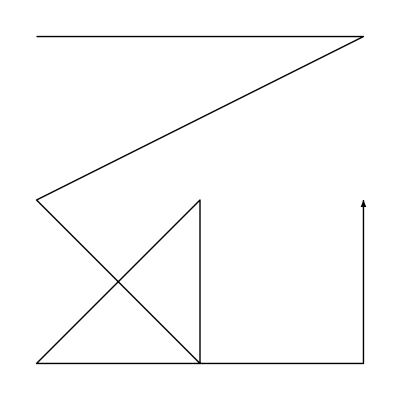
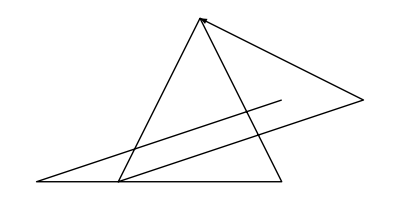
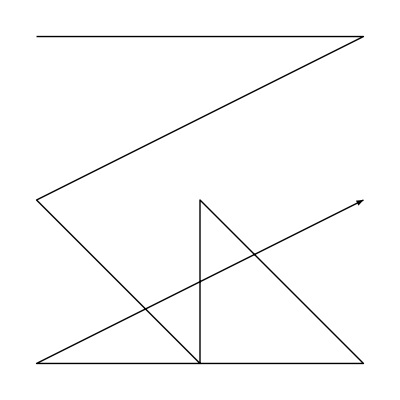
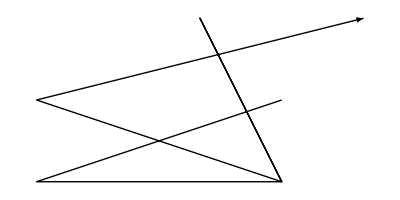
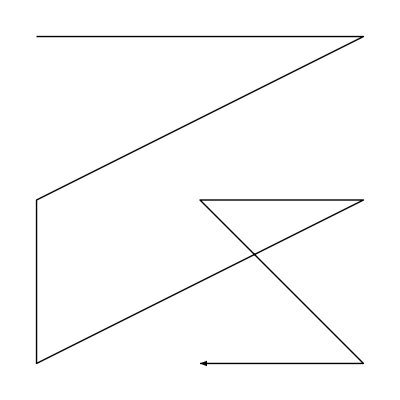
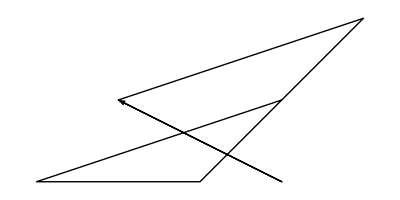
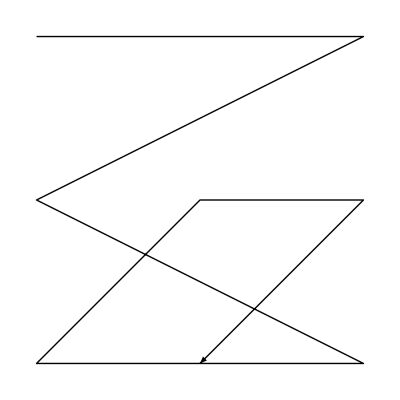
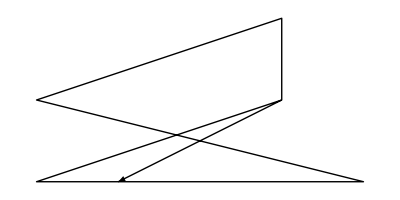
{{(1 | 2 | 3
4 | 6 | 9
7 | 5 | 8),{-Graphics-,{{1,0},{1,0},{-2,-1},{1,-1},{0,1},{-1,-1},{2,0},{0,1}},-Graphics-}},{(1 | 2 | 3
4 | 6 | 9
8 | 5 | 7),{-Graphics-,{{1,0},{1,0},{-2,-1},{1,-1},{0,1},{1,-1},{-2,0},{2,1}},-Graphics-}},{(1 | 2 | 3
4 | 7 | 6
5 | 9 | 8),{-Graphics-,{{1,0},{1,0},{-2,-1},{0,-1},{2,1},{-1,0},{1,-1},{-1,0}},-Graphics-}},{(1 | 2 | 3
4 | 7 | 8
6 | 9 | 5),{-Graphics-,{{1,0},{1,0},{-2,-1},{2,-1},{-2,0},{1,1},{1,0},{-1,-1}},-Graphics-}},{(1 | 2 | 3
4 | 7 | 9
6 | 8 | 5),{-Graphics-,{{1,0},{1,0},{-2,-1},{2,-1},{-2,0},{1,1},{0,-1},{1,1}},-Graphics-}},{(1 | 2 | 3
5 | 9 | 8
4 | 7 | 6),{-Graphics-,{{1,0},{1,0},{-2,-2},{0,1},{2,-1},{-1,0},{1,1},{-1,0}},-Graphics-}},{(1 | 2 | 3
6 | 4 | 7
8 | 5 | 9),{-Graphics-,{{1,0},{1,0},{-1,-1},{0,-1},{-1,1},{2,0},{-2,-1},{2,0}},-Graphics-}},{(1 | 2 | 3
6 | 5 | 9
7 | 4 | 8),{-Graphics-,{{1,0},{1,0},{-1,-2},{0,1},{-1,0},{0,-1},{2,0},{0,1}},-Graphics-}},{(1 | 2 | 3
6 | 7 | 9
8 | 5 | 4),{-Graphics-,{{1,0},{1,0},{0,-2},{-1,0},{-1,1},{1,0},{-1,-1},{2,1}},-Graphics-}},{(1 | 2 | 3
6 | 8 | 5
4 | 7 | 9),{-Graphics-,{{1,0},{1,0},{-2,-2},{2,1},{-2,0},{1,-1},{0,1},{1,-1}},-Graphics-}},{(1 | 2 | 3
6 | 9 | 5
4 | 7 | 8),{-Graphics-,{{1,0},{1,0},{-2,-2},{2,1},{-2,0},{1,-1},{1,0},{-1,1}},-Graphics-}},{(1 | 2 | 3
7 | 4 | 8
6 | 5 | 9),{-Graphics-,{{1,0},{1,0},{-1,-1},{0,-1},{-1,0},{0,1},{2,0},{0,-1}},-Graphics-}},{(1 | 2 | 3
7 | 5 | 8
4 | 6 | 9),{-Graphics-,{{1,0},{1,0},{-2,-2},{1,1},{0,-1},{-1,1},{2,0},{0,-1}},-Graphics-}},{(1 | 2 | 3
8 | 5 | 4
6 | 7 | 9),{-Graphics-,{{1,0},{1,0},{0,-1},{-1,0},{-1,-1},{1,0},{-1,1},{2,-1}},-Graphics-}},{(1 | 2 | 3
8 | 5 | 7
4 | 6 | 9),{-Graphics-,{{1,0},{1,0},{-2,-2},{1,1},{0,-1},{1,1},{-2,0},{2,-1}},-Graphics-}},{(1 | 2 | 3
8 | 5 | 9
6 | 4 | 7),{-Graphics-,{{1,0},{1,0},{-1,-2},{0,1},{-1,-1},{2,0},{-2,1},{2,0}},-Graphics-}},{(1 | 2 | 4
3 | 5 | 7
6 | 9 | 8),{-Graphics-,{{1,0},{-1,-1},{2,1},{-1,-1},{-1,-1},{2,1},{0,-1},{-1,0}},-Graphics-}},{(1 | 2 | 4
3 | 5 | 9
6 | 7 | 8),{-Graphics-,{{1,0},{-1,-1},{2,1},{-1,-1},{-1,-1},{1,0},{1,0},{0,1}},-Graphics-}},{(1 | 2 | 4
3 | 5 | 9
8 | 7 | 6),{-Graphics-,{{1,0},{-1,-1},{2,1},{-1,-1},{1,-1},{-1,0},{-1,0},{2,1}},-Graphics-}},{(1 | 2 | 4
6 | 7 | 8
3 | 5 | 9),{-Graphics-,{{1,0},{-1,-2},{2,2},{-1,-2},{-1,1},{1,0},{1,0},{0,-1}},-Graphics-}},{(1 | 2 | 4
6 | 9 | 8
3 | 5 | 7),{-Graphics-,{{1,0},{-1,-2},{2,2},{-1,-2},{-1,1},{2,-1},{0,1},{-1,0}},-Graphics-}},{(1 | 2 | 4
8 | 7 | 6
3 | 5 | 9),{-Graphics-,{{1,0},{-1,-2},{2,2},{-1,-2},{1,1},{-1,0},{-1,0},{2,-1}},-Graphics-}},{(1 | 2 | 5
3 | 4 | 8
9 | 7 | 6),{-Graphics-,{{1,0},{-1,-1},{1,0},{1,1},{0,-2},{-1,0},{1,1},{-2,-1}},-Graphics-}},{(1 | 2 | 5
6 | 4 | 3
9 | 7 | 8),{-Graphics-,{{1,0},{1,-1},{-1,0},{1,1},{-2,-1},{1,-1},{1,0},{-2,0}},-Graphics-}},{(1 | 2 | 5
7 | 3 | 6
9 | 4 | 8),{-Graphics-,{{1,0},{0,-1},{0,-1},{1,2},{0,-1},{-2,0},{2,-1},{-2,0}},-Graphics-}},{(1 | 2 | 5
9 | 4 | 8
7 | 3 | 6),{-Graphics-,{{1,0},{0,-2},{0,1},{1,1},{0,-2},{-2,0},{2,1},{-2,0}},-Graphics-}},{(1 | 2 | 5
9 | 7 | 6
3 | 4 | 8),{-Graphics-,{{1,0},{-1,-2},{1,0},{1,2},{0,-1},{-1,0},{1,-1},{-2,1}},-Graphics-}},{(1 | 2 | 5
9 | 7 | 8
6 | 4 | 3),{-Graphics-,{{1,0},{1,-2},{-1,0},{1,2},{-2,-2},{1,1},{1,0},{-2,0}},-Graphics-}},{(1 | 2 | 6
4 | 7 | 3
5 | 9 | 8),{-Graphics-,{{1,0},{1,-1},{-2,0},{0,-1},{2,2},{-1,-1},{1,-1},{-1,0}},-Graphics-}},{(1 | 2 | 6
5 | 9 | 8
4 | 7 | 3),{-Graphics-,{{1,0},{1,-2},{-2,0},{0,1},{2,1},{-1,-2},{1,1},{-1,0}},-Graphics-}},{(1 | 2 | 6
7 | 4 | 9
8 | 3 | 5),{-Graphics-,{{1,0},{0,-2},{0,1},{1,-1},{0,2},{-2,-1},{0,-1},{2,1}},-Graphics-}},{(1 | 2 | 6
8 | 3 | 5
7 | 4 | 9),{-Graphics-,{{1,0},{0,-1},{0,-1},{1,1},{0,1},{-2,-2},{0,1},{2,-1}},-Graphics-}},{(1 | 2 | 7
3 | 5 | 8
6 | 9 | 4),{-Graphics-,{{1,0},{-1,-1},{2,-1},{-1,1},{-1,-1},{2,2},{0,-1},{-1,-1}},-Graphics-}},{(1 | 2 | 7
4 | 3 | 5
9 | 6 | 8),{-Graphics-,{{1,0},{0,-1},{-1,0},{2,0},{-1,-1},{1,2},{0,-2},{-2,0}},-Graphics-}},{(1 | 2 | 7
4 | 5 | 3
6 | 8 | 9),{-Graphics-,{{1,0},{1,-1},{-2,0},{1,0},{-1,-1},{2,2},{-1,-2},{1,0}},-Graphics-}},{(1 | 2 | 7
6 | 3 | 4
9 | 5 | 8),{-Graphics-,{{1,0},{0,-1},{1,0},{-1,-1},{-1,1},{2,1},{0,-2},{-2,0}},-Graphics-}},{(1 | 2 | 7
6 | 8 | 9
4 | 5 | 3),{-Graphics-,{{1,0},{1,-2},{-2,0},{1,0},{-1,1},{2,1},{-1,-1},{1,0}},-Graphics-}},{(1 | 2 | 7
6 | 9 | 4
3 | 5 | 8),{-Graphics-,{{1,0},{-1,-2},{2,1},{-1,-1},{-1,1},{2,1},{0,-2},{-1,1}},-Graphics-}},{(1 | 2 | 7
9 | 5 | 8
6 | 3 | 4),{-Graphics-,{{1,0},{0,-2},{1,0},{-1,1},{-1,-1},{2,2},{0,-1},{-2,0}},-Graphics-}},{(1 | 2 | 7
9 | 6 | 8
4 | 3 | 5),{-Graphics-,{{1,0},{0,-2},{-1,0},{2,0},{-1,1},{1,1},{0,-1},{-2,0}},-Graphics-}},{(1 | 2 | 8
4 | 3 | 5
9 | 6 | 7),{-Graphics-,{{1,0},{0,-1},{-1,0},{2,0},{-1,-1},{1,0},{0,2},{-2,-2}},-Graphics-}},{(1 | 2 | 8
4 | 3 | 6
7 | 5 | 9),{-Graphics-,{{1,0},{0,-1},{-1,0},{1,-1},{1,1},{-2,-1},{2,2},{0,-2}},-Graphics-}},{(1 | 2 | 8
6 | 5 | 4
9 | 7 | 3),{-Graphics-,{{1,0},{1,-2},{0,1},{-1,0},{-1,0},{1,-1},{1,2},{-2,-2}},-Graphics-}},{(1 | 2 | 8
7 | 5 | 9
4 | 3 | 6),{-Graphics-,{{1,0},{0,-2},{-1,0},{1,1},{1,-1},{-2,1},{2,1},{0,-1}},-Graphics-}},{(1 | 2 | 8
9 | 6 | 7
4 | 3 | 5),{-Graphics-,{{1,0},{0,-2},{-1,0},{2,0},{-1,1},{1,0},{0,1},{-2,-1}},-Graphics-}},{(1 | 2 | 8
9 | 7 | 3
6 | 5 | 4),{-Graphics-,{{1,0},{1,-1},{0,-1},{-1,0},{-1,0},{1,1},{1,1},{-2,-1}},-Graphics-}},{(1 | 3 | 2
4 | 6 | 7
5 | 8 | 9),{-Graphics-,{{2,0},{-1,0},{-1,-1},{0,-1},{1,1},{1,0},{-1,-1},{1,0}},-Graphics-}},{(1 | 3 | 2
4 | 8 | 7
6 | 5 | 9),{-Graphics-,{{2,0},{-1,0},{-1,-1},{1,-1},{-1,0},{2,1},{-1,0},{1,-1}},-Graphics-}},{(1 | 3 | 2
4 | 9 | 6
7 | 8 | 5),{-Graphics-,{{2,0},{-1,0},{-1,-1},{2,-1},{0,1},{-2,-1},{1,0},{0,1}},-Graphics-}},{(1 | 3 | 2
4 | 9 | 6
8 | 7 | 5),{-Graphics-,{{2,0},{-1,0},{-1,-1},{2,-1},{0,1},{-1,-1},{-1,0},{1,1}},-Graphics-}},{(1 | 3 | 2
4 | 9 | 7
6 | 5 | 8),{-Graphics-,{{2,0},{-1,0},{-1,-1},{1,-1},{-1,0},{2,1},{0,-1},{-1,1}},-Graphics-}},{(1 | 3 | 2
5 | 8 | 9
4 | 6 | 7),{-Graphics-,{{2,0},{-1,0},{-1,-2},{0,1},{1,-1},{1,0},{-1,1},{1,0}},-Graphics-}},{(1 | 3 | 2
6 | 5 | 8
4 | 9 | 7),{-Graphics-,{{2,0},{-1,0},{-1,-2},{1,1},{-1,0},{2,-1},{0,1},{-1,-1}},-Graphics-}},{(1 | 3 | 2
6 | 5 | 9
4 | 8 | 7),{-Graphics-,{{2,0},{-1,0},{-1,-2},{1,1},{-1,0},{2,-1},{-1,0},{1,1}},-Graphics-}},{(1 | 3 | 2
6 | 7 | 4
8 | 9 | 5),{-Graphics-,{{2,0},{-1,0},{1,-1},{0,-1},{-2,1},{1,0},{-1,-1},{1,0}},-Graphics-}},{(1 | 3 | 2
6 | 9 | 5
7 | 8 | 4),{-Graphics-,{{2,0},{-1,0},{1,-2},{0,1},{-2,0},{0,-1},{1,0},{0,1}},-Graphics-}},{(1 | 3 | 2
6 | 9 | 7
8 | 4 | 5),{-Graphics-,{{2,0},{-1,0},{0,-2},{1,0},{-2,1},{2,0},{-2,-1},{1,1}},-Graphics-}},{(1 | 3 | 2
7 | 8 | 4
6 | 9 | 5),{-Graphics-,{{2,0},{-1,0},{1,-1},{0,-1},{-2,0},{0,1},{1,0},{0,-1}},-Graphics-}},{(1 | 3 | 2
7 | 8 | 5
4 | 9 | 6),{-Graphics-,{{2,0},{-1,0},{-1,-2},{2,1},{0,-1},{-2,1},{1,0},{0,-1}},-Graphics-}},{(1 | 3 | 2
8 | 4 | 5
6 | 9 | 7),{-Graphics-,{{2,0},{-1,0},{0,-1},{1,0},{-2,-1},{2,0},{-2,1},{1,-1}},-Graphics-}},{(1 | 3 | 2
8 | 7 | 5
4 | 9 | 6),{-Graphics-,{{2,0},{-1,0},{-1,-2},{2,1},{0,-1},{-1,1},{-1,0},{1,-1}},-Graphics-}},{(1 | 3 | 2
8 | 9 | 5
6 | 7 | 4),{-Graphics-,{{2,0},{-1,0},{1,-2},{0,1},{-2,-1},{1,0},{-1,1},{1,0}},-Graphics-}},{(1 | 3 | 6
2 | 5 | 7
4 | 9 | 8),{-Graphics-,{{0,-1},{1,1},{-1,-2},{1,1},{1,1},{0,-1},{0,-1},{-1,0}},-Graphics-}},{(1 | 3 | 6
2 | 5 | 9
4 | 7 | 8),{-Graphics-,{{0,-1},{1,1},{-1,-2},{1,1},{1,1},{-1,-2},{1,0},{0,1}},-Graphics-}},{(1 | 3 | 6
2 | 5 | 9
7 | 8 | 4),{-Graphics-,{{0,-1},{1,1},{1,-2},{-1,1},{1,1},{-2,-2},{1,0},{1,1}},-Graphics-}},{(1 | 3 | 6
4 | 7 | 8
2 | 5 | 9),{-Graphics-,{{0,-2},{1,2},{-1,-1},{1,-1},{1,2},{-1,-1},{1,0},{0,-1}},-Graphics-}},{(1 | 3 | 6
4 | 9 | 8
2 | 5 | 7),{-Graphics-,{{0,-2},{1,2},{-1,-1},{1,-1},{1,2},{0,-2},{0,1},{-1,0}},-Graphics-}},{(1 | 3 | 6
5 | 4 | 2
7 | 8 | 9),{-Graphics-,{{2,-1},{-1,1},{0,-1},{-1,0},{2,1},{-2,-2},{1,0},{1,0}},-Graphics-}},{(1 | 3 | 6
7 | 2 | 5
8 | 4 | 9),{-Graphics-,{{1,-1},{0,1},{0,-2},{1,1},{0,1},{-2,-1},{0,-1},{2,0}},-Graphics-}},{(1 | 3 | 6
7 | 8 | 4
2 | 5 | 9),{-Graphics-,{{0,-2},{1,2},{1,-1},{-1,-1},{1,2},{-2,-1},{1,0},{1,-1}},-Graphics-}},{(1 | 3 | 6
7 | 8 | 9
5 | 4 | 2),{-Graphics-,{{2,-2},{-1,2},{0,-2},{-1,0},{2,2},{-2,-1},{1,0},{1,0}},-Graphics-}},{(1 | 3 | 6
8 | 4 | 9
7 | 2 | 5),{-Graphics-,{{1,-2},{0,2},{0,-1},{1,-1},{0,2},{-2,-2},{0,1},{2,0}},-Graphics-}},{(1 | 3 | 7
5 | 8 | 4
6 | 9 | 2),{-Graphics-,{{2,-2},{-1,2},{1,-1},{-2,0},{0,-1},{2,2},{-1,-1},{0,-1}},-Graphics-}},{(1 | 3 | 7
6 | 9 | 2
5 | 8 | 4),{-Graphics-,{{2,-1},{-1,1},{1,-2},{-2,0},{0,1},{2,1},{-1,-2},{0,1}},-Graphics-}},{(1 | 3 | 8
2 | 5 | 7
4 | 9 | 6),{-Graphics-,{{0,-1},{1,1},{-1,-2},{1,1},{1,-1},{0,1},{0,1},{-1,-2}},-Graphics-}},{(1 | 3 | 8
4 | 9 | 6
2 | 5 | 7),{-Graphics-,{{0,-2},{1,2},{-1,-1},{1,-1},{1,1},{0,-1},{0,2},{-1,-1}},-Graphics-}},{(1 | 3 | 9
2 | 4 | 7
5 | 8 | 6),{-Graphics-,{{0,-1},{1,1},{0,-1},{-1,-1},{2,0},{0,1},{-1,-1},{1,2}},-Graphics-}},{(1 | 3 | 9
5 | 8 | 6
2 | 4 | 7),{-Graphics-,{{0,-2},{1,2},{0,-2},{-1,1},{2,0},{0,-1},{-1,1},{1,1}},-Graphics-}},{(1 | 4 | 2
3 | 7 | 5
6 | 8 | 9),{-Graphics-,{{2,0},{-2,-1},{1,1},{1,-1},{-2,-1},{1,1},{0,-1},{1,0}},-Graphics-}},{(1 | 4 | 2
3 | 9 | 5
6 | 8 | 7),{-Graphics-,{{2,0},{-2,-1},{1,1},{1,-1},{-2,-1},{2,0},{-1,0},{0,1}},-Graphics-}},{(1 | 4 | 2
3 | 9 | 5
8 | 6 | 7),{-Graphics-,{{2,0},{-2,-1},{1,1},{1,-1},{-1,-1},{1,0},{-2,0},{1,1}},-Graphics-}},{(1 | 4 | 2
6 | 8 | 7
3 | 9 | 5),{-Graphics-,{{2,0},{-2,-2},{1,2},{1,-2},{-2,1},{2,0},{-1,0},{0,-1}},-Graphics-}},{(1 | 4 | 2
6 | 8 | 9
3 | 7 | 5),{-Graphics-,{{2,0},{-2,-2},{1,2},{1,-2},{-2,1},{1,-1},{0,1},{1,0}},-Graphics-}},{(1 | 4 | 2
8 | 6 | 7
3 | 9 | 5),{-Graphics-,{{2,0},{-2,-2},{1,2},{1,-2},{-1,1},{1,0},{-2,0},{1,-1}},-Graphics-}},{(1 | 4 | 5
2 | 7 | 9
3 | 6 | 8),{-Graphics-,{{0,-1},{0,-1},{1,2},{1,0},{-1,-2},{0,1},{1,-1},{0,1}},-Graphics-}},{(1 | 4 | 5
2 | 7 | 9
6 | 3 | 8),{-Graphics-,{{0,-1},{1,-1},{0,2},{1,0},{-2,-2},{1,1},{1,-1},{0,1}},-Graphics-}},{(1 | 4 | 5
3 | 6 | 8
2 | 7 | 9),{-Graphics-,{{0,-2},{0,1},{1,1},{1,0},{-1,-1},{0,-1},{1,1},{0,-1}},-Graphics-}},{(1 | 4 | 5
6 | 3 | 8
2 | 7 | 9),{-Graphics-,{{0,-2},{1,1},{0,1},{1,0},{-2,-1},{1,-1},{1,1},{0,-1}},-Graphics-}},{(1 | 4 | 5
6 | 7 | 9
8 | 2 | 3),{-Graphics-,{{1,-2},{1,0},{-1,2},{1,0},{-2,-1},{1,0},{-1,-1},{2,1}},-Graphics-}},{(1 | 4 | 5
8 | 2 | 3
6 | 7 | 9),{-Graphics-,{{1,-1},{1,0},{-1,1},{1,0},{-2,-2},{1,0},{-1,1},{2,-1}},-Graphics-}},{(1 | 4 | 6
2 | 5 | 8
7 | 3 | 9),{-Graphics-,{{0,-1},{1,-1},{0,2},{0,-1},{1,1},{-2,-2},{2,1},{0,-1}},-Graphics-}},{(1 | 4 | 6
2 | 7 | 8
3 | 9 | 5),{-Graphics-,{{0,-1},{0,-1},{1,2},{1,-2},{0,2},{-1,-1},{1,0},{-1,-1}},-Graphics-}},{(1 | 4 | 6
2 | 7 | 9
3 | 8 | 5),{-Graphics-,{{0,-1},{0,-1},{1,2},{1,-2},{0,2},{-1,-1},{0,-1},{1,1}},-Graphics-}},{(1 | 4 | 6
3 | 8 | 5
2 | 7 | 9),{-Graphics-,{{0,-2},{0,1},{1,1},{1,-1},{0,1},{-1,-2},{0,1},{1,-1}},-Graphics-}},{(1 | 4 | 6
3 | 9 | 5
2 | 7 | 8),{-Graphics-,{{0,-2},{0,1},{1,1},{1,-1},{0,1},{-1,-2},{1,0},{-1,1}},-Graphics-}},{(1 | 4 | 6
5 | 3 | 2
7 | 8 | 9),{-Graphics-,{{2,-1},{-1,0},{0,1},{-1,-1},{2,1},{-2,-2},{1,0},{1,0}},-Graphics-}},{(1 | 4 | 6
7 | 3 | 9
2 | 5 | 8),{-Graphics-,{{0,-2},{1,1},{0,1},{0,-2},{1,2},{-2,-1},{2,-1},{0,1}},-Graphics-}},{(1 | 4 | 6
7 | 8 | 9
5 | 3 | 2),{-Graphics-,{{2,-2},{-1,0},{0,2},{-1,-2},{2,2},{-2,-1},{1,0},{1,0}},-Graphics-}},{(1 | 4 | 7
2 | 3 | 5
8 | 6 | 9),{-Graphics-,{{0,-1},{1,0},{0,1},{1,-1},{-1,-1},{1,2},{-2,-2},{2,0}},-Graphics-}},{(1 | 4 | 7
2 | 6 | 5
3 | 9 | 8),{-Graphics-,{{0,-1},{0,-1},{1,2},{1,-1},{-1,0},{1,1},{0,-2},{-1,0}},-Graphics-}},{(1 | 4 | 7
3 | 9 | 8
2 | 6 | 5),{-Graphics-,{{0,-2},{0,1},{1,1},{1,-2},{-1,0},{1,2},{0,-1},{-1,0}},-Graphics-}},{(1 | 4 | 7
6 | 2 | 3
9 | 5 | 8),{-Graphics-,{{1,-1},{1,0},{-1,1},{0,-2},{-1,1},{2,1},{0,-2},{-2,0}},-Graphics-}},{(1 | 4 | 7
8 | 6 | 9
2 | 3 | 5),{-Graphics-,{{0,-2},{1,0},{0,2},{1,-2},{-1,1},{1,1},{-2,-1},{2,0}},-Graphics-}},{(1 | 4 | 7
9 | 5 | 8
6 | 2 | 3),{-Graphics-,{{1,-2},{1,0},{-1,2},{0,-1},{-1,-1},{2,2},{0,-1},{-2,0}},-Graphics-}},{(1 | 4 | 8
2 | 6 | 5
3 | 9 | 7),{-Graphics-,{{0,-1},{0,-1},{1,2},{1,-1},{-1,0},{1,-1},{0,2},{-1,-2}},-Graphics-}},{(1 | 4 | 8
3 | 9 | 7
2 | 6 | 5),{-Graphics-,{{0,-2},{0,1},{1,1},{1,-2},{-1,0},{1,1},{0,1},{-1,-1}},-Graphics-}},{(1 | 4 | 8
6 | 2 | 3
7 | 5 | 9),{-Graphics-,{{1,-1},{1,0},{-1,1},{0,-2},{-1,1},{0,-1},{2,2},{0,-2}},-Graphics-}},{(1 | 4 | 8
7 | 5 | 9
6 | 2 | 3),{-Graphics-,{{1,-2},{1,0},{-1,2},{0,-1},{-1,-1},{0,1},{2,1},{0,-1}},-Graphics-}},{(1 | 4 | 9
2 | 3 | 6
7 | 5 | 8),{-Graphics-,{{0,-1},{1,0},{0,1},{0,-2},{1,1},{-2,-1},{2,0},{0,2}},-Graphics-}},{(1 | 4 | 9
2 | 3 | 6
8 | 5 | 7),{-Graphics-,{{0,-1},{1,0},{0,1},{0,-2},{1,1},{0,-1},{-2,0},{2,2}},-Graphics-}},{(1 | 4 | 9
7 | 5 | 2
8 | 6 | 3),{-Graphics-,{{2,-1},{0,-1},{-1,2},{0,-1},{0,-1},{-1,1},{0,-1},{2,2}},-Graphics-}},{(1 | 4 | 9
7 | 5 | 8
2 | 3 | 6),{-Graphics-,{{0,-2},{1,0},{0,2},{0,-1},{1,-1},{-2,1},{2,0},{0,1}},-Graphics-}},{(1 | 4 | 9
8 | 5 | 7
2 | 3 | 6),{-Graphics-,{{0,-2},{1,0},{0,2},{0,-1},{1,-1},{0,1},{-2,0},{2,1}},-Graphics-}},{(1 | 4 | 9
8 | 6 | 3
7 | 5 | 2),{-Graphics-,{{2,-2},{0,1},{-1,1},{0,-2},{0,1},{-1,-1},{0,1},{2,1}},-Graphics-}},{(1 | 5 | 2
3 | 8 | 4
9 | 6 | 7),{-Graphics-,{{2,0},{-2,-1},{2,0},{-1,1},{0,-2},{1,0},{-1,1},{-1,-1}},-Graphics-}},{(1 | 5 | 2
6 | 3 | 4
9 | 8 | 7),{-Graphics-,{{2,0},{-1,-1},{1,0},{-1,1},{-1,-1},{2,-1},{-1,0},{-1,0}},-Graphics-}},{(1 | 5 | 2
7 | 6 | 3
9 | 8 | 4),{-Graphics-,{{2,0},{0,-1},{0,-1},{-1,2},{0,-1},{-1,0},{1,-1},{-1,0}},-Graphics-}},{(1 | 5 | 2
9 | 6 | 7
3 | 8 | 4),{-Graphics-,{{2,0},{-2,-2},{2,0},{-1,2},{0,-1},{1,0},{-1,-1},{-1,1}},-Graphics-}},{(1 | 5 | 2
9 | 8 | 4
7 | 6 | 3),{-Graphics-,{{2,0},{0,-2},{0,1},{-1,1},{0,-2},{-1,0},{1,1},{-1,0}},-Graphics-}},{(1 | 5 | 2
9 | 8 | 7
6 | 3 | 4),{-Graphics-,{{2,0},{-1,-2},{1,0},{-1,2},{-1,-2},{2,1},{-1,0},{-1,0}},-Graphics-}},{(1 | 5 | 4
2 | 9 | 7
3 | 8 | 6),{-Graphics-,{{0,-1},{0,-1},{2,2},{-1,0},{1,-2},{0,1},{-1,-1},{0,1}},-Graphics-}},{(1 | 5 | 4
2 | 9 | 7
6 | 8 | 3),{-Graphics-,{{0,-1},{2,-1},{0,2},{-1,0},{-1,-2},{2,1},{-1,-1},{0,1}},-Graphics-}},{(1 | 5 | 4
3 | 8 | 6
2 | 9 | 7),{-Graphics-,{{0,-2},{0,1},{2,1},{-1,0},{1,-1},{0,-1},{-1,1},{0,-1}},-Graphics-}},{(1 | 5 | 4
6 | 8 | 3
2 | 9 | 7),{-Graphics-,{{0,-2},{2,1},{0,1},{-1,0},{-1,-1},{2,-1},{-1,1},{0,-1}},-Graphics-}},{(1 | 5 | 4
6 | 9 | 7
8 | 3 | 2),{-Graphics-,{{2,-2},{-1,0},{1,2},{-1,0},{-1,-1},{2,0},{-2,-1},{1,1}},-Graphics-}},{(1 | 5 | 4
8 | 3 | 2
6 | 9 | 7),{-Graphics-,{{2,-1},{-1,0},{1,1},{-1,0},{-1,-2},{2,0},{-2,1},{1,-1}},-Graphics-}},{(1 | 5 | 6
3 | 8 | 9
7 | 4 | 2),{-Graphics-,{{2,-2},{-2,1},{1,-1},{0,2},{1,0},{-2,-2},{1,1},{1,0}},-Graphics-}},{(1 | 5 | 6
7 | 4 | 2
3 | 8 | 9),{-Graphics-,{{2,-1},{-2,-1},{1,1},{0,1},{1,0},{-2,-1},{1,-1},{1,0}},-Graphics-}},{(1 | 5 | 7
3 | 4 | 8
6 | 2 | 9),{-Graphics-,{{1,-2},{-1,1},{1,0},{0,1},{-1,-2},{2,2},{0,-1},{0,-1}},-Graphics-}},{(1 | 5 | 7
4 | 3 | 8
6 | 2 | 9),{-Graphics-,{{1,-2},{0,1},{-1,0},{1,1},{-1,-2},{2,2},{0,-1},{0,-1}},-Graphics-}},{(1 | 5 | 7
6 | 2 | 9
3 | 4 | 8),{-Graphics-,{{1,-1},{-1,-1},{1,0},{0,2},{-1,-1},{2,1},{0,-2},{0,1}},-Graphics-}},{(1 | 5 | 7
6 | 2 | 9
4 | 3 | 8),{-Graphics-,{{1,-1},{0,-1},{-1,0},{1,2},{-1,-1},{2,1},{0,-2},{0,1}},-Graphics-}},{(1 | 6 | 2
4 | 3 | 7
5 | 8 | 9),{-Graphics-,{{2,0},{-1,-1},{-1,0},{0,-1},{1,2},{1,-1},{-1,-1},{1,0}},-Graphics-}},{(1 | 6 | 2
5 | 8 | 9
4 | 3 | 7),{-Graphics-,{{2,0},{-1,-2},{-1,0},{0,1},{1,1},{1,-2},{-1,1},{1,0}},-Graphics-}},{(1 | 6 | 2
7 | 9 | 4
8 | 5 | 3),{-Graphics-,{{2,0},{0,-2},{0,1},{-1,-1},{0,2},{-1,-1},{0,-1},{1,1}},-Graphics-}},{(1 | 6 | 2
8 | 5 | 3
7 | 9 | 4),{-Graphics-,{{2,0},{0,-1},{0,-1},{-1,1},{0,1},{-1,-2},{0,1},{1,-1}},-Graphics-}},{(1 | 6 | 3
2 | 7 | 5
4 | 8 | 9),{-Graphics-,{{0,-1},{2,1},{-2,-2},{2,1},{-1,1},{0,-1},{0,-1},{1,0}},-Graphics-}},{(1 | 6 | 3
2 | 9 | 5
4 | 8 | 7),{-Graphics-,{{0,-1},{2,1},{-2,-2},{2,1},{-1,1},{1,-2},{-1,0},{0,1}},-Graphics-}},{(1 | 6 | 3
2 | 9 | 5
7 | 4 | 8),{-Graphics-,{{0,-1},{2,1},{-1,-2},{1,1},{-1,1},{-1,-2},{2,0},{-1,1}},-Graphics-}},{(1 | 6 | 3
4 | 8 | 7
2 | 9 | 5),{-Graphics-,{{0,-2},{2,2},{-2,-1},{2,-1},{-1,2},{1,-1},{-1,0},{0,-1}},-Graphics-}},{(1 | 6 | 3
4 | 8 | 9
2 | 7 | 5),{-Graphics-,{{0,-2},{2,2},{-2,-1},{2,-1},{-1,2},{0,-2},{0,1},{1,0}},-Graphics-}},{(1 | 6 | 3
5 | 2 | 4
7 | 9 | 8),{-Graphics-,{{1,-1},{1,1},{0,-1},{-2,0},{1,1},{-1,-2},{2,0},{-1,0}},-Graphics-}},{(1 | 6 | 3
7 | 4 | 8
2 | 9 | 5),{-Graphics-,{{0,-2},{2,2},{-1,-1},{1,-1},{-1,2},{-1,-1},{2,0},{-1,-1}},-Graphics-}},{(1 | 6 | 3
7 | 5 | 2
8 | 9 | 4),{-Graphics-,{{2,-1},{0,1},{0,-2},{-1,1},{0,1},{-1,-1},{0,-1},{1,0}},-Graphics-}},{(1 | 6 | 3
7 | 9 | 8
5 | 2 | 4),{-Graphics-,{{1,-2},{1,2},{0,-2},{-2,0},{1,2},{-1,-1},{2,0},{-1,0}},-Graphics-}},{(1 | 6 | 3
8 | 9 | 4
7 | 5 | 2),{-Graphics-,{{2,-2},{0,2},{0,-1},{-1,-1},{0,2},{-1,-2},{0,1},{1,0}},-Graphics-}},{(1 | 6 | 4
2 | 8 | 5
7 | 9 | 3),{-Graphics-,{{0,-1},{2,-1},{0,2},{0,-1},{-1,1},{-1,-2},{1,1},{0,-1}},-Graphics-}},{(1 | 6 | 4
2 | 8 | 7
3 | 5 | 9),{-Graphics-,{{0,-1},{0,-1},{2,2},{-1,-2},{0,2},{1,-1},{-1,0},{1,-1}},-Graphics-}},{(1 | 6 | 4
2 | 9 | 7
3 | 5 | 8),{-Graphics-,{{0,-1},{0,-1},{2,2},{-1,-2},{0,2},{1,-1},{0,-1},{-1,1}},-Graphics-}},{(1 | 6 | 4
3 | 5 | 8
2 | 9 | 7),{-Graphics-,{{0,-2},{0,1},{2,1},{-1,-1},{0,1},{1,-2},{0,1},{-1,-1}},-Graphics-}},{(1 | 6 | 4
3 | 5 | 9
2 | 8 | 7),{-Graphics-,{{0,-2},{0,1},{2,1},{-1,-1},{0,1},{1,-2},{-1,0},{1,1}},-Graphics-}},{(1 | 6 | 4
5 | 2 | 3
7 | 9 | 8),{-Graphics-,{{1,-1},{1,0},{0,1},{-2,-1},{1,1},{-1,-2},{2,0},{-1,0}},-Graphics-}},{(1 | 6 | 4
7 | 9 | 3
2 | 8 | 5),{-Graphics-,{{0,-2},{2,1},{0,1},{0,-2},{-1,2},{-1,-1},{1,-1},{0,1}},-Graphics-}},{(1 | 6 | 4
7 | 9 | 8
5 | 2 | 3),{-Graphics-,{{1,-2},{1,0},{0,2},{-2,-2},{1,2},{-1,-1},{2,0},{-1,0}},-Graphics-}},{(1 | 6 | 5
3 | 9 | 8
7 | 2 | 4),{-Graphics-,{{1,-2},{-1,1},{2,-1},{0,2},{-1,0},{-1,-2},{2,1},{-1,0}},-Graphics-}},{(1 | 6 | 5
7 | 2 | 4
3 | 9 | 8),{-Graphics-,{{1,-1},{-1,-1},{2,1},{0,1},{-1,0},{-1,-1},{2,-1},{-1,0}},-Graphics-}},{(1 | 6 | 7
2 | 5 | 4
3 | 9 | 8),{-Graphics-,{{0,-1},{0,-1},{2,1},{-1,0},{0,1},{1,0},{0,-2},{-1,0}},-Graphics-}},{(1 | 6 | 7
3 | 9 | 8
2 | 5 | 4),{-Graphics-,{{0,-2},{0,1},{2,-1},{-1,0},{0,2},{1,0},{0,-1},{-1,0}},-Graphics-}},{(1 | 6 | 7
4 | 2 | 5
8 | 3 | 9),{-Graphics-,{{1,-1},{0,-1},{-1,1},{2,0},{-1,1},{1,0},{-2,-2},{2,0}},-Graphics-}},{(1 | 6 | 7
8 | 3 | 9
4 | 2 | 5),{-Graphics-,{{1,-2},{0,1},{-1,-1},{2,0},{-1,2},{1,0},{-2,-1},{2,0}},-Graphics-}},{(1 | 6 | 8
2 | 4 | 5
3 | 7 | 9),{-Graphics-,{{0,-1},{0,-1},{1,1},{1,0},{-1,1},{0,-2},{1,2},{0,-2}},-Graphics-}},{(1 | 6 | 8
2 | 7 | 5
3 | 9 | 4),{-Graphics-,{{0,-1},{0,-1},{2,0},{0,1},{-1,1},{0,-1},{1,1},{-1,-2}},-Graphics-}},{(1 | 6 | 8
3 | 7 | 9
2 | 4 | 5),{-Graphics-,{{0,-2},{0,1},{1,-1},{1,0},{-1,2},{0,-1},{1,1},{0,-1}},-Graphics-}},{(1 | 6 | 8
3 | 9 | 4
2 | 7 | 5),{-Graphics-,{{0,-2},{0,1},{2,0},{0,-1},{-1,2},{0,-2},{1,2},{-1,-1}},-Graphics-}},{(1 | 6 | 8
4 | 7 | 2
5 | 9 | 3),{-Graphics-,{{2,-1},{0,-1},{-2,1},{0,-1},{1,2},{0,-1},{1,1},{-1,-2}},-Graphics-}},{(1 | 6 | 8
5 | 9 | 3
4 | 7 | 2),{-Graphics-,{{2,-2},{0,1},{-2,-1},{0,1},{1,1},{0,-2},{1,2},{-1,-1}},-Graphics-}},{(1 | 6 | 9
2 | 3 | 5
7 | 4 | 8),{-Graphics-,{{0,-1},{1,0},{0,-1},{1,1},{-1,1},{-1,-2},{2,0},{0,2}},-Graphics-}},{(1 | 6 | 9
2 | 4 | 7
5 | 3 | 8),{-Graphics-,{{0,-1},{1,-1},{0,1},{-1,-1},{1,2},{1,-1},{0,-1},{0,2}},-Graphics-}},{(1 | 6 | 9
2 | 5 | 7
8 | 4 | 3),{-Graphics-,{{0,-1},{2,-1},{-1,0},{0,1},{0,1},{1,-1},{-2,-1},{2,2}},-Graphics-}},{(1 | 6 | 9
4 | 2 | 5
7 | 3 | 8),{-Graphics-,{{1,-1},{0,-1},{-1,1},{2,0},{-1,1},{-1,-2},{2,0},{0,2}},-Graphics-}},{(1 | 6 | 9
5 | 3 | 8
2 | 4 | 7),{-Graphics-,{{0,-2},{1,1},{0,-1},{-1,1},{1,1},{1,-2},{0,1},{0,1}},-Graphics-}},{(1 | 6 | 9
7 | 3 | 8
4 | 2 | 5),{-Graphics-,{{1,-2},{0,1},{-1,-1},{2,0},{-1,2},{-1,-1},{2,0},{0,1}},-Graphics-}},{(1 | 6 | 9
7 | 4 | 2
8 | 5 | 3),{-Graphics-,{{2,-1},{0,-1},{-1,1},{0,-1},{0,2},{-1,-1},{0,-1},{2,2}},-Graphics-}},{(1 | 6 | 9
7 | 4 | 8
2 | 3 | 5),{-Graphics-,{{0,-2},{1,0},{0,1},{1,-1},{-1,2},{-1,-1},{2,0},{0,1}},-Graphics-}},{(1 | 6 | 9
8 | 4 | 3
2 | 5 | 7),{-Graphics-,{{0,-2},{2,1},{-1,0},{0,-1},{0,2},{1,-2},{-2,1},{2,1}},-Graphics-}},{(1 | 6 | 9
8 | 5 | 3
7 | 4 | 2),{-Graphics-,{{2,-2},{0,1},{-1,-1},{0,1},{0,1},{-1,-2},{0,1},{2,1}},-Graphics-}},{(1 | 7 | 2
3 | 8 | 5
6 | 4 | 9),{-Graphics-,{{2,0},{-2,-1},{1,-1},{1,1},{-2,-1},{1,2},{0,-1},{1,-1}},-Graphics-}},{(1 | 7 | 2
4 | 3 | 5
6 | 9 | 8),{-Graphics-,{{2,0},{-1,-1},{-1,0},{2,0},{-2,-1},{1,2},{1,-2},{-1,0}},-Graphics-}},{(1 | 7 | 2
4 | 5 | 3
9 | 8 | 6),{-Graphics-,{{2,0},{0,-1},{-2,0},{1,0},{1,-1},{-1,2},{0,-2},{-1,0}},-Graphics-}},{(1 | 7 | 2
6 | 4 | 3
9 | 8 | 5),{-Graphics-,{{2,0},{0,-1},{-1,0},{1,-1},{-2,1},{1,1},{0,-2},{-1,0}},-Graphics-}},{(1 | 7 | 2
6 | 4 | 9
3 | 8 | 5),{-Graphics-,{{2,0},{-2,-2},{1,1},{1,-1},{-2,1},{1,1},{0,-2},{1,1}},-Graphics-}},{(1 | 7 | 2
6 | 9 | 8
4 | 3 | 5),{-Graphics-,{{2,0},{-1,-2},{-1,0},{2,0},{-2,1},{1,1},{1,-1},{-1,0}},-Graphics-}},{(1 | 7 | 2
9 | 8 | 5
6 | 4 | 3),{-Graphics-,{{2,0},{0,-2},{-1,0},{1,1},{-2,-1},{1,2},{0,-1},{-1,0}},-Graphics-}},{(1 | 7 | 2
9 | 8 | 6
4 | 5 | 3),{-Graphics-,{{2,0},{0,-2},{-2,0},{1,0},{1,1},{-1,1},{0,-1},{-1,0}},-Graphics-}},{(1 | 7 | 3
5 | 4 | 8
6 | 2 | 9),{-Graphics-,{{1,-2},{1,2},{-1,-1},{-1,0},{0,-1},{1,2},{1,-1},{0,-1}},-Graphics-}},{(1 | 7 | 3
6 | 2 | 9
5 | 4 | 8),{-Graphics-,{{1,-1},{1,1},{-1,-2},{-1,0},{0,1},{1,1},{1,-2},{0,1}},-Graphics-}},{(1 | 7 | 4
2 | 5 | 3
8 | 9 | 6),{-Graphics-,{{0,-1},{2,0},{0,1},{-1,-1},{1,-1},{-1,2},{-1,-2},{1,0}},-Graphics-}},{(1 | 7 | 4
2 | 5 | 6
3 | 8 | 9),{-Graphics-,{{0,-1},{0,-1},{2,2},{-1,-1},{1,0},{-1,1},{0,-2},{1,0}},-Graphics-}},{(1 | 7 | 4
3 | 8 | 9
2 | 5 | 6),{-Graphics-,{{0,-2},{0,1},{2,1},{-1,-2},{1,0},{-1,2},{0,-1},{1,0}},-Graphics-}},{(1 | 7 | 4
6 | 3 | 2
9 | 8 | 5),{-Graphics-,{{2,-1},{-1,0},{1,1},{0,-2},{-2,1},{1,1},{0,-2},{-1,0}},-Graphics-}},{(1 | 7 | 4
8 | 9 | 6
2 | 5 | 3),{-Graphics-,{{0,-2},{2,0},{0,2},{-1,-2},{1,1},{-1,1},{-1,-1},{1,0}},-Graphics-}},{(1 | 7 | 4
9 | 8 | 5
6 | 3 | 2),{-Graphics-,{{2,-2},{-1,0},{1,2},{0,-1},{-2,-1},{1,2},{0,-1},{-1,0}},-Graphics-}},{(1 | 7 | 5
3 | 8 | 4
6 | 9 | 2),{-Graphics-,{{2,-2},{-2,1},{2,0},{0,1},{-2,-2},{1,2},{0,-1},{0,-1}},-Graphics-}},{(1 | 7 | 5
4 | 8 | 3
6 | 9 | 2),{-Graphics-,{{2,-2},{0,1},{-2,0},{2,1},{-2,-2},{1,2},{0,-1},{0,-1}},-Graphics-}},{(1 | 7 | 5
6 | 9 | 2
3 | 8 | 4),{-Graphics-,{{2,-1},{-2,-1},{2,0},{0,2},{-2,-1},{1,1},{0,-2},{0,1}},-Graphics-}},{(1 | 7 | 5
6 | 9 | 2
4 | 8 | 3),{-Graphics-,{{2,-1},{0,-1},{-2,0},{2,2},{-2,-1},{1,1},{0,-2},{0,1}},-Graphics-}},{(1 | 7 | 6
2 | 4 | 5
3 | 8 | 9),{-Graphics-,{{0,-1},{0,-1},{1,1},{1,0},{0,1},{-1,0},{0,-2},{1,0}},-Graphics-}},{(1 | 7 | 6
3 | 8 | 9
2 | 4 | 5),{-Graphics-,{{0,-2},{0,1},{1,-1},{1,0},{0,2},{-1,0},{0,-1},{1,0}},-Graphics-}},{(1 | 7 | 6
4 | 5 | 2
8 | 9 | 3),{-Graphics-,{{2,-1},{0,-1},{-2,1},{1,0},{1,1},{-1,0},{-1,-2},{1,0}},-Graphics-}},{(1 | 7 | 6
8 | 9 | 3
4 | 5 | 2),{-Graphics-,{{2,-2},{0,1},{-2,-1},{1,0},{1,2},{-1,0},{-1,-1},{1,0}},-Graphics-}},{(1 | 7 | 8
2 | 4 | 3
6 | 9 | 5),{-Graphics-,{{0,-1},{2,0},{-1,0},{1,-1},{-2,0},{1,2},{1,0},{-1,-2}},-Graphics-}},{(1 | 7 | 8
3 | 2 | 4
6 | 5 | 9),{-Graphics-,{{1,-1},{-1,0},{2,0},{-1,-1},{-1,0},{1,2},{1,0},{0,-2}},-Graphics-}},{(1 | 7 | 8
4 | 5 | 6
9 | 2 | 3),{-Graphics-,{{1,-2},{1,0},{-2,1},{1,0},{1,0},{-1,1},{1,0},{-2,-2}},-Graphics-}},{(1 | 7 | 8
6 | 4 | 5
9 | 2 | 3),{-Graphics-,{{1,-2},{1,0},{-1,1},{1,0},{-2,0},{1,1},{1,0},{-2,-2}},-Graphics-}},{(1 | 7 | 8
6 | 5 | 9
3 | 2 | 4),{-Graphics-,{{1,-2},{-1,0},{2,0},{-1,1},{-1,0},{1,1},{1,0},{0,-1}},-Graphics-}},{(1 | 7 | 8
6 | 9 | 5
2 | 4 | 3),{-Graphics-,{{0,-2},{2,0},{-1,0},{1,1},{-2,0},{1,1},{1,0},{-1,-1}},-Graphics-}},{(1 | 7 | 8
9 | 2 | 3
4 | 5 | 6),{-Graphics-,{{1,-1},{1,0},{-2,-1},{1,0},{1,0},{-1,2},{1,0},{-2,-1}},-Graphics-}},{(1 | 7 | 8
9 | 2 | 3
6 | 4 | 5),{-Graphics-,{{1,-1},{1,0},{-1,-1},{1,0},{-2,0},{1,2},{1,0},{-2,-1}},-Graphics-}},{(1 | 7 | 9
2 | 3 | 4
5 | 6 | 8),{-Graphics-,{{0,-1},{1,0},{1,0},{-2,-1},{1,0},{0,2},{1,-2},{0,2}},-Graphics-}},{(1 | 7 | 9
5 | 6 | 8
2 | 3 | 4),{-Graphics-,{{0,-2},{1,0},{1,0},{-2,1},{1,0},{0,1},{1,-1},{0,1}},-Graphics-}},{(1 | 8 | 2
4 | 5 | 3
9 | 7 | 6),{-Graphics-,{{2,0},{0,-1},{-2,0},{1,0},{1,-1},{-1,0},{0,2},{-1,-2}},-Graphics-}},{(1 | 8 | 2
4 | 6 | 3
7 | 9 | 5),{-Graphics-,{{2,0},{0,-1},{-2,0},{2,-1},{-1,1},{-1,-1},{1,2},{0,-2}},-Graphics-}},{(1 | 8 | 2
6 | 4 | 5
9 | 3 | 7),{-Graphics-,{{2,0},{-1,-2},{0,1},{1,0},{-2,0},{2,-1},{-1,2},{-1,-2}},-Graphics-}},{(1 | 8 | 2
7 | 9 | 5
4 | 6 | 3),{-Graphics-,{{2,0},{0,-2},{-2,0},{2,1},{-1,-1},{-1,1},{1,1},{0,-1}},-Graphics-}},{(1 | 8 | 2
9 | 3 | 7
6 | 4 | 5),{-Graphics-,{{2,0},{-1,-1},{0,-1},{1,0},{-2,0},{2,1},{-1,1},{-1,-1}},-Graphics-}},{(1 | 8 | 2
9 | 7 | 6
4 | 5 | 3),{-Graphics-,{{2,0},{0,-2},{-2,0},{1,0},{1,1},{-1,0},{0,1},{-1,-1}},-Graphics-}},{(1 | 8 | 3
2 | 7 | 5
4 | 6 | 9),{-Graphics-,{{0,-1},{2,1},{-2,-2},{2,1},{-1,-1},{0,1},{0,1},{1,-2}},-Graphics-}},{(1 | 8 | 3
4 | 6 | 9
2 | 7 | 5),{-Graphics-,{{0,-2},{2,2},{-2,-1},{2,-1},{-1,1},{0,-1},{0,2},{1,-1}},-Graphics-}},{(1 | 8 | 4
2 | 5 | 6
3 | 7 | 9),{-Graphics-,{{0,-1},{0,-1},{2,2},{-1,-1},{1,0},{-1,-1},{0,2},{1,-2}},-Graphics-}},{(1 | 8 | 4
3 | 7 | 9
2 | 5 | 6),{-Graphics-,{{0,-2},{0,1},{2,1},{-1,-2},{1,0},{-1,1},{0,1},{1,-1}},-Graphics-}},{(1 | 8 | 4
6 | 3 | 2
7 | 9 | 5),{-Graphics-,{{2,-1},{-1,0},{1,1},{0,-2},{-2,1},{0,-1},{1,2},{0,-2}},-Graphics-}},{(1 | 8 | 4
7 | 9 | 5
6 | 3 | 2),{-Graphics-,{{2,-2},{-1,0},{1,2},{0,-1},{-2,-1},{0,1},{1,1},{0,-1}},-Graphics-}},{(1 | 8 | 6
2 | 5 | 4
3 | 9 | 7),{-Graphics-,{{0,-1},{0,-1},{2,1},{-1,0},{1,1},{0,-2},{-1,2},{0,-2}},-Graphics-}},{(1 | 8 | 6
2 | 5 | 7
3 | 4 | 9),{-Graphics-,{{0,-1},{0,-1},{1,0},{0,1},{1,1},{0,-1},{-1,1},{1,-2}},-Graphics-}},{(1 | 8 | 6
3 | 4 | 9
2 | 5 | 7),{-Graphics-,{{0,-2},{0,1},{1,0},{0,-1},{1,2},{0,-2},{-1,2},{1,-1}},-Graphics-}},{(1 | 8 | 6
3 | 9 | 7
2 | 5 | 4),{-Graphics-,{{0,-2},{0,1},{2,-1},{-1,0},{1,2},{0,-1},{-1,1},{0,-1}},-Graphics-}},{(1 | 8 | 6
4 | 2 | 7
5 | 3 | 9),{-Graphics-,{{1,-1},{0,-1},{-1,1},{0,-1},{2,2},{0,-1},{-1,1},{1,-2}},-Graphics-}},{(1 | 8 | 6
5 | 3 | 9
4 | 2 | 7),{-Graphics-,{{1,-2},{0,1},{-1,-1},{0,1},{2,1},{0,-2},{-1,2},{1,-1}},-Graphics-}},{(1 | 8 | 7
2 | 3 | 4
6 | 5 | 9),{-Graphics-,{{0,-1},{1,0},{1,0},{-1,-1},{-1,0},{2,2},{-1,0},{1,-2}},-Graphics-}},{(1 | 8 | 7
3 | 4 | 2
6 | 9 | 5),{-Graphics-,{{2,-1},{-2,0},{1,0},{1,-1},{-2,0},{2,2},{-1,0},{0,-2}},-Graphics-}},{(1 | 8 | 7
4 | 6 | 5
9 | 3 | 2),{-Graphics-,{{2,-2},{-1,0},{-1,1},{2,0},{-1,0},{1,1},{-1,0},{-1,-2}},-Graphics-}},{(1 | 8 | 7
6 | 5 | 4
9 | 3 | 2),{-Graphics-,{{2,-2},{-1,0},{1,1},{-1,0},{-1,0},{2,1},{-1,0},{-1,-2}},-Graphics-}},{(1 | 8 | 7
6 | 5 | 9
2 | 3 | 4),{-Graphics-,{{0,-2},{1,0},{1,0},{-1,1},{-1,0},{2,1},{-1,0},{1,-1}},-Graphics-}},{(1 | 8 | 7
6 | 9 | 5
3 | 4 | 2),{-Graphics-,{{2,-2},{-2,0},{1,0},{1,1},{-2,0},{2,1},{-1,0},{0,-1}},-Graphics-}},{(1 | 8 | 7
9 | 3 | 2
4 | 6 | 5),{-Graphics-,{{2,-1},{-1,0},{-1,-1},{2,0},{-1,0},{1,2},{-1,0},{-1,-1}},-Graphics-}},{(1 | 8 | 7
9 | 3 | 2
6 | 5 | 4),{-Graphics-,{{2,-1},{-1,0},{1,-1},{-1,0},{-1,0},{2,2},{-1,0},{-1,-1}},-Graphics-}},{(1 | 9 | 3
2 | 7 | 4
5 | 6 | 8),{-Graphics-,{{0,-1},{2,1},{0,-1},{-2,-1},{1,0},{0,1},{1,-1},{-1,2}},-Graphics-}},{(1 | 9 | 3
5 | 6 | 8
2 | 7 | 4),{-Graphics-,{{0,-2},{2,2},{0,-2},{-2,1},{1,0},{0,-1},{1,1},{-1,1}},-Graphics-}},{(1 | 9 | 4
2 | 6 | 3
7 | 8 | 5),{-Graphics-,{{0,-1},{2,0},{0,1},{0,-2},{-1,1},{-1,-1},{1,0},{0,2}},-Graphics-}},{(1 | 9 | 4
2 | 6 | 3
8 | 7 | 5),{-Graphics-,{{0,-1},{2,0},{0,1},{0,-2},{-1,1},{0,-1},{-1,0},{1,2}},-Graphics-}},{(1 | 9 | 4
7 | 2 | 5
8 | 3 | 6),{-Graphics-,{{1,-1},{0,-1},{1,2},{0,-1},{0,-1},{-2,1},{0,-1},{1,2}},-Graphics-}},{(1 | 9 | 4
7 | 8 | 5
2 | 6 | 3),{-Graphics-,{{0,-2},{2,0},{0,2},{0,-1},{-1,-1},{-1,1},{1,0},{0,1}},-Graphics-}},{(1 | 9 | 4
8 | 3 | 6
7 | 2 | 5),{-Graphics-,{{1,-2},{0,1},{1,1},{0,-2},{0,1},{-2,-1},{0,1},{1,1}},-Graphics-}},{(1 | 9 | 4
8 | 7 | 5
2 | 6 | 3),{-Graphics-,{{0,-2},{2,0},{0,2},{0,-1},{-1,-1},{0,1},{-1,0},{1,1}},-Graphics-}},{(1 | 9 | 6
2 | 5 | 3
7 | 8 | 4),{-Graphics-,{{0,-1},{2,0},{0,-1},{-1,1},{1,1},{-2,-2},{1,0},{0,2}},-Graphics-}},{(1 | 9 | 6
2 | 7 | 4
5 | 8 | 3),{-Graphics-,{{0,-1},{2,-1},{0,1},{-2,-1},{2,2},{-1,-1},{0,-1},{0,2}},-Graphics-}},{(1 | 9 | 6
2 | 7 | 5
8 | 3 | 4),{-Graphics-,{{0,-1},{1,-1},{1,0},{0,1},{0,1},{-1,-1},{-1,-1},{1,2}},-Graphics-}},{(1 | 9 | 6
4 | 5 | 2
7 | 8 | 3),{-Graphics-,{{2,-1},{0,-1},{-2,1},{1,0},{1,1},{-2,-2},{1,0},{0,2}},-Graphics-}},{(1 | 9 | 6
5 | 8 | 3
2 | 7 | 4),{-Graphics-,{{0,-2},{2,1},{0,-1},{-2,1},{2,1},{-1,-2},{0,1},{0,1}},-Graphics-}},{(1 | 9 | 6
7 | 2 | 4
8 | 3 | 5),{-Graphics-,{{1,-1},{0,-1},{1,1},{0,-1},{0,2},{-2,-1},{0,-1},{1,2}},-Graphics-}},{(1 | 9 | 6
7 | 8 | 3
4 | 5 | 2),{-Graphics-,{{2,-2},{0,1},{-2,-1},{1,0},{1,2},{-2,-1},{1,0},{0,1}},-Graphics-}},{(1 | 9 | 6
7 | 8 | 4
2 | 5 | 3),{-Graphics-,{{0,-2},{2,0},{0,1},{-1,-1},{1,2},{-2,-1},{1,0},{0,1}},-Graphics-}},{(1 | 9 | 6
8 | 3 | 4
2 | 7 | 5),{-Graphics-,{{0,-2},{1,1},{1,0},{0,-1},{0,2},{-1,-2},{-1,1},{1,1}},-Graphics-}},{(1 | 9 | 6
8 | 3 | 5
7 | 2 | 4),{-Graphics-,{{1,-2},{0,1},{1,-1},{0,1},{0,1},{-2,-2},{0,1},{1,1}},-Graphics-}},{(1 | 9 | 7
2 | 4 | 3
5 | 8 | 6),{-Graphics-,{{0,-1},{2,0},{-1,0},{-1,-1},{2,0},{0,2},{-1,-2},{0,2}},-Graphics-}},{(1 | 9 | 7
5 | 8 | 6
2 | 4 | 3),{-Graphics-,{{0,-2},{2,0},{-1,0},{-1,1},{2,0},{0,1},{-1,-1},{0,1}},-Graphics-}},{(2 | 1 | 3
4 | 6 | 7
5 | 8 | 9),{-Graphics-,{{-1,0},{2,0},{-2,-1},{0,-1},{1,1},{1,0},{-1,-1},{1,0}},-Graphics-}},{(2 | 1 | 3
4 | 7 | 8
5 | 6 | 9),{-Graphics-,{{-1,0},{2,0},{-2,-1},{0,-1},{1,0},{0,1},{1,0},{0,-1}},-Graphics-}},{(2 | 1 | 3
5 | 6 | 9
4 | 7 | 8),{-Graphics-,{{-1,0},{2,0},{-2,-2},{0,1},{1,0},{0,-1},{1,0},{0,1}},-Graphics-}},{(2 | 1 | 3
5 | 7 | 8
6 | 4 | 9),{-Graphics-,{{-1,0},{2,0},{-1,-2},{-1,1},{0,-1},{1,1},{1,0},{0,-1}},-Graphics-}},{(2 | 1 | 3
5 | 8 | 4
7 | 6 | 9),{-Graphics-,{{-1,0},{2,0},{0,-1},{-2,0},{1,-1},{-1,0},{1,1},{1,-1}},-Graphics-}},{(2 | 1 | 3
5 | 8 | 7
6 | 4 | 9),{-Graphics-,{{-1,0},{2,0},{-1,-2},{-1,1},{0,-1},{2,1},{-1,0},{1,-1}},-Graphics-}},{(2 | 1 | 3
5 | 8 | 9
4 | 6 | 7),{-Graphics-,{{-1,0},{2,0},{-2,-2},{0,1},{1,-1},{1,0},{-1,1},{1,0}},-Graphics-}},{(2 | 1 | 3
6 | 4 | 9
5 | 7 | 8),{-Graphics-,{{-1,0},{2,0},{-1,-1},{-1,-1},{0,1},{1,-1},{1,0},{0,1}},-Graphics-}},{(2 | 1 | 3
6 | 4 | 9
5 | 8 | 7),{-Graphics-,{{-1,0},{2,0},{-1,-1},{-1,-1},{0,1},{2,-1},{-1,0},{1,1}},-Graphics-}},{(2 | 1 | 3
7 | 4 | 6
9 | 5 | 8),{-Graphics-,{{-1,0},{2,0},{-1,-1},{0,-1},{1,1},{-2,0},{2,-1},{-2,0}},-Graphics-}},{(2 | 1 | 3
7 | 4 | 8
9 | 6 | 5),{-Graphics-,{{-1,0},{2,0},{-1,-1},{1,-1},{-1,0},{-1,1},{2,0},{-2,-1}},-Graphics-}},{(2 | 1 | 3
7 | 4 | 9
8 | 6 | 5),{-Graphics-,{{-1,0},{2,0},{-1,-1},{1,-1},{-1,0},{-1,1},{0,-1},{2,1}},-Graphics-}},{(2 | 1 | 3
7 | 6 | 9
5 | 8 | 4),{-Graphics-,{{-1,0},{2,0},{0,-2},{-2,0},{1,1},{-1,0},{1,-1},{1,1}},-Graphics-}},{(2 | 1 | 3
8 | 6 | 5
7 | 4 | 9),{-Graphics-,{{-1,0},{2,0},{-1,-2},{1,1},{-1,0},{-1,-1},{0,1},{2,-1}},-Graphics-}},{(2 | 1 | 3
9 | 5 | 8
7 | 4 | 6),{-Graphics-,{{-1,0},{2,0},{-1,-2},{0,1},{1,-1},{-2,0},{2,1},{-2,0}},-Graphics-}},{(2 | 1 | 3
9 | 6 | 5
7 | 4 | 8),{-Graphics-,{{-1,0},{2,0},{-1,-2},{1,1},{-1,0},{-1,-1},{2,0},{-2,1}},-Graphics-}},{(2 | 1 | 4
5 | 3 | 7
9 | 6 | 8),{-Graphics-,{{-1,0},{1,-1},{1,1},{-2,-1},{1,-1},{1,1},{0,-1},{-2,0}},-Graphics-}},{(2 | 1 | 4
5 | 3 | 9
7 | 6 | 8),{-Graphics-,{{-1,0},{1,-1},{1,1},{-2,-1},{1,-1},{-1,0},{2,0},{0,1}},-Graphics-}},{(2 | 1 | 4
5 | 3 | 9
7 | 8 | 6),{-Graphics-,{{-1,0},{1,-1},{1,1},{-2,-1},{2,-1},{-2,0},{1,0},{1,1}},-Graphics-}},{(2 | 1 | 4
7 | 6 | 8
5 | 3 | 9),{-Graphics-,{{-1,0},{1,-2},{1,2},{-2,-2},{1,1},{-1,0},{2,0},{0,-1}},-Graphics-}},{(2 | 1 | 4
7 | 8 | 6
5 | 3 | 9),{-Graphics-,{{-1,0},{1,-2},{1,2},{-2,-2},{2,1},{-2,0},{1,0},{1,-1}},-Graphics-}},{(2 | 1 | 4
9 | 6 | 8
5 | 3 | 7),{-Graphics-,{{-1,0},{1,-2},{1,2},{-2,-2},{1,1},{1,-1},{0,1},{-2,0}},-Graphics-}},{(2 | 1 | 5
3 | 7 | 6
4 | 9 | 8),{-Graphics-,{{-1,0},{0,-1},{0,-1},{2,2},{0,-1},{-1,0},{1,-1},{-1,0}},-Graphics-}},{(2 | 1 | 5
4 | 3 | 8
7 | 9 | 6),{-Graphics-,{{-1,0},{1,-1},{-1,0},{2,1},{0,-2},{-2,0},{2,1},{-1,-1}},-Graphics-}},{(2 | 1 | 5
4 | 6 | 3
7 | 9 | 8),{-Graphics-,{{-1,0},{2,-1},{-2,0},{2,1},{-1,-1},{-1,-1},{2,0},{-1,0}},-Graphics-}},{(2 | 1 | 5
4 | 9 | 8
3 | 7 | 6),{-Graphics-,{{-1,0},{0,-2},{0,1},{2,1},{0,-2},{-1,0},{1,1},{-1,0}},-Graphics-}},{(2 | 1 | 5
7 | 9 | 6
4 | 3 | 8),{-Graphics-,{{-1,0},{1,-2},{-1,0},{2,2},{0,-1},{-2,0},{2,-1},{-1,1}},-Graphics-}},{(2 | 1 | 5
7 | 9 | 8
4 | 6 | 3),{-Graphics-,{{-1,0},{2,-2},{-2,0},{2,2},{-1,-2},{-1,1},{2,0},{-1,0}},-Graphics-}},{(2 | 1 | 6
3 | 8 | 5
4 | 7 | 9),{-Graphics-,{{-1,0},{0,-1},{0,-1},{2,1},{0,1},{-1,-2},{0,1},{1,-1}},-Graphics-}},{(2 | 1 | 6
4 | 7 | 9
3 | 8 | 5),{-Graphics-,{{-1,0},{0,-2},{0,1},{2,-1},{0,2},{-1,-1},{0,-1},{1,1}},-Graphics-}},{(2 | 1 | 6
7 | 4 | 3
9 | 5 | 8),{-Graphics-,{{-1,0},{2,-1},{-1,0},{0,-1},{1,2},{-2,-1},{2,-1},{-2,0}},-Graphics-}},{(2 | 1 | 6
9 | 5 | 8
7 | 4 | 3),{-Graphics-,{{-1,0},{2,-2},{-1,0},{0,1},{1,1},{-2,-2},{2,1},{-2,0}},-Graphics-}},{(2 | 1 | 7
3 | 4 | 5
6 | 9 | 8),{-Graphics-,{{-1,0},{0,-1},{1,0},{1,0},{-2,-1},{2,2},{0,-2},{-1,0}},-Graphics-}},{(2 | 1 | 7
3 | 6 | 4
5 | 9 | 8),{-Graphics-,{{-1,0},{0,-1},{2,0},{-2,-1},{1,1},{1,1},{0,-2},{-1,0}},-Graphics-}},{(2 | 1 | 7
5 | 3 | 8
9 | 6 | 4),{-Graphics-,{{-1,0},{1,-1},{1,-1},{-2,1},{1,-1},{1,2},{0,-1},{-2,-1}},-Graphics-}},{(2 | 1 | 7
5 | 4 | 3
8 | 6 | 9),{-Graphics-,{{-1,0},{2,-1},{-1,0},{-1,0},{1,-1},{1,2},{-2,-2},{2,0}},-Graphics-}},{(2 | 1 | 7
5 | 9 | 8
3 | 6 | 4),{-Graphics-,{{-1,0},{0,-2},{2,0},{-2,1},{1,-1},{1,2},{0,-1},{-1,0}},-Graphics-}},{(2 | 1 | 7
6 | 9 | 8
3 | 4 | 5),{-Graphics-,{{-1,0},{0,-2},{1,0},{1,0},{-2,1},{2,1},{0,-1},{-1,0}},-Graphics-}},{(2 | 1 | 7
8 | 6 | 9
5 | 4 | 3),{-Graphics-,{{-1,0},{2,-2},{-1,0},{-1,0},{1,1},{1,1},{-2,-1},{2,0}},-Graphics-}},{(2 | 1 | 7
9 | 6 | 4
5 | 3 | 8),{-Graphics-,{{-1,0},{1,-2},{1,1},{-2,-1},{1,1},{1,1},{0,-2},{-2,1}},-Graphics-}},{(2 | 1 | 8
3 | 4 | 5
6 | 9 | 7),{-Graphics-,{{-1,0},{0,-1},{1,0},{1,0},{-2,-1},{2,0},{0,2},{-1,-2}},-Graphics-}},{(2 | 1 | 8
3 | 4 | 6
5 | 7 | 9),{-Graphics-,{{-1,0},{0,-1},{1,0},{-1,-1},{2,1},{-1,-1},{1,2},{0,-2}},-Graphics-}},{(2 | 1 | 8
5 | 6 | 4
7 | 9 | 3),{-Graphics-,{{-1,0},{2,-2},{0,1},{-2,0},{1,0},{-1,-1},{2,2},{-1,-2}},-Graphics-}},{(2 | 1 | 8
5 | 7 | 9
3 | 4 | 6),{-Graphics-,{{-1,0},{0,-2},{1,0},{-1,1},{2,-1},{-1,1},{1,1},{0,-1}},-Graphics-}},{(2 | 1 | 8
6 | 9 | 7
3 | 4 | 5),{-Graphics-,{{-1,0},{0,-2},{1,0},{1,0},{-2,1},{2,0},{0,1},{-1,-1}},-Graphics-}},{(2 | 1 | 8
7 | 9 | 3
5 | 6 | 4),{-Graphics-,{{-1,0},{2,-1},{0,-1},{-2,0},{1,0},{-1,1},{2,1},{-1,-1}},-Graphics-}},{(2 | 3 | 4
1 | 7 | 9
5 | 6 | 8),{-Graphics-,{{0,1},{1,0},{1,0},{-2,-2},{1,0},{0,1},{1,-1},{0,1}},-Graphics-}},{(2 | 3 | 4
1 | 8 | 7
6 | 5 | 9),{-Graphics-,{{0,1},{1,0},{1,0},{-1,-2},{-1,0},{2,1},{-1,0},{1,-1}},-Graphics-}},{(2 | 3 | 4
5 | 6 | 9
7 | 1 | 8),{-Graphics-,{{-1,2},{1,0},{1,0},{-2,-1},{1,0},{-1,-1},{2,0},{0,1}},-Graphics-}},{(2 | 3 | 4
7 | 1 | 8
5 | 6 | 9),{-Graphics-,{{-1,1},{1,0},{1,0},{-2,-2},{1,0},{-1,1},{2,0},{0,-1}},-Graphics-}},{(2 | 3 | 5
1 | 4 | 7
8 | 6 | 9),{-Graphics-,{{0,1},{1,0},{0,-1},{1,1},{-1,-2},{1,1},{-2,-1},{2,0}},-Graphics-}},{(2 | 3 | 5
1 | 6 | 9
7 | 4 | 8),{-Graphics-,{{0,1},{1,0},{0,-2},{1,2},{-1,-1},{-1,-1},{2,0},{0,1}},-Graphics-}},{(2 | 3 | 5
6 | 4 | 1
9 | 8 | 7),{-Graphics-,{{-2,1},{1,0},{0,-1},{1,1},{-2,-1},{2,-1},{-1,0},{-1,0}},-Graphics-}},{(2 | 3 | 6
1 | 4 | 9
7 | 5 | 8),{-Graphics-,{{0,1},{1,0},{0,-1},{0,-1},{1,2},{-2,-2},{2,0},{0,1}},-Graphics-}},{(2 | 3 | 6
1 | 4 | 9
8 | 5 | 7),{-Graphics-,{{0,1},{1,0},{0,-1},{0,-1},{1,2},{0,-2},{-2,0},{2,1}},-Graphics-}},{(2 | 3 | 6
4 | 7 | 1
5 | 8 | 9),{-Graphics-,{{-2,1},{1,0},{-1,-1},{0,-1},{2,2},{-1,-1},{0,-1},{1,0}},-Graphics-}},{(2 | 3 | 6
4 | 8 | 1
5 | 9 | 7),{-Graphics-,{{-2,1},{1,0},{-1,-1},{0,-1},{2,2},{0,-2},{-1,1},{0,-1}},-Graphics-}},{(2 | 3 | 8
4 | 5 | 1
7 | 9 | 6),{-Graphics-,{{-2,1},{1,0},{-1,-1},{1,0},{1,-1},{-2,0},{2,2},{-1,-2}},-Graphics-}},{(2 | 3 | 9
7 | 8 | 1
4 | 5 | 6),{-Graphics-,{{-2,1},{1,0},{-1,-2},{1,0},{1,0},{-2,1},{1,0},{1,1}},-Graphics-}},{(2 | 3 | 9
7 | 8 | 1
5 | 6 | 4),{-Graphics-,{{-2,1},{1,0},{1,-2},{-2,0},{1,0},{-1,1},{1,0},{1,1}},-Graphics-}},{(2 | 4 | 3
1 | 7 | 8
6 | 9 | 5),{-Graphics-,{{0,1},{2,0},{-1,0},{1,-2},{-2,0},{1,1},{1,0},{-1,-1}},-Graphics-}},{(2 | 4 | 3
1 | 9 | 7
5 | 8 | 6),{-Graphics-,{{0,1},{2,0},{-1,0},{-1,-2},{2,0},{0,1},{-1,-1},{0,1}},-Graphics-}},{(2 | 4 | 3
7 | 8 | 1
5 | 9 | 6),{-Graphics-,{{-2,1},{2,0},{-1,0},{-1,-2},{2,0},{-2,1},{1,0},{0,-1}},-Graphics-}},{(2 | 4 | 5
1 | 6 | 8
3 | 7 | 9),{-Graphics-,{{0,1},{0,-2},{1,2},{1,0},{-1,-1},{0,-1},{1,1},{0,-1}},-Graphics-}},{(2 | 4 | 5
1 | 7 | 6
3 | 8 | 9),{-Graphics-,{{0,1},{0,-2},{1,2},{1,0},{0,-1},{-1,0},{0,-1},{1,0}},-Graphics-}},{(2 | 4 | 5
3 | 7 | 8
6 | 1 | 9),{-Graphics-,{{-1,2},{0,-1},{1,1},{1,0},{-2,-2},{1,1},{1,0},{0,-1}},-Graphics-}},{(2 | 4 | 5
3 | 8 | 9
6 | 1 | 7),{-Graphics-,{{-1,2},{0,-1},{1,1},{1,0},{-2,-2},{2,0},{-1,1},{1,0}},-Graphics-}},{(2 | 4 | 5
6 | 1 | 7
3 | 8 | 9),{-Graphics-,{{-1,1},{0,-2},{1,2},{1,0},{-2,-1},{2,0},{-1,-1},{1,0}},-Graphics-}},{(2 | 4 | 5
6 | 1 | 9
3 | 7 | 8),{-Graphics-,{{-1,1},{0,-2},{1,2},{1,0},{-2,-1},{1,-1},{1,0},{0,1}},-Graphics-}},{(2 | 4 | 5
6 | 3 | 1
9 | 8 | 7),{-Graphics-,{{-2,1},{1,-1},{0,1},{1,0},{-2,-1},{2,-1},{-1,0},{-1,0}},-Graphics-}},{(2 | 4 | 7
1 | 3 | 9
5 | 8 | 6),{-Graphics-,{{0,1},{1,-1},{0,1},{-1,-2},{2,0},{0,2},{-1,-2},{1,1}},-Graphics-}},{(2 | 4 | 7
1 | 6 | 9
5 | 3 | 8),{-Graphics-,{{0,1},{1,-2},{0,2},{-1,-2},{1,1},{1,1},{0,-2},{0,1}},-Graphics-}},{(2 | 4 | 7
3 | 5 | 9
8 | 1 | 6),{-Graphics-,{{-1,2},{0,-1},{1,1},{0,-1},{1,-1},{0,2},{-2,-2},{2,1}},-Graphics-}},{(2 | 4 | 7
6 | 5 | 1
9 | 8 | 3),{-Graphics-,{{-2,1},{2,-2},{-1,2},{0,-1},{-1,0},{2,1},{-1,-2},{-1,0}},-Graphics-}},{(2 | 4 | 7
8 | 1 | 6
3 | 5 | 9),{-Graphics-,{{-1,1},{0,-2},{1,2},{0,-2},{1,1},{0,1},{-2,-1},{2,-1}},-Graphics-}},{(2 | 4 | 7
9 | 6 | 1
3 | 5 | 8),{-Graphics-,{{-2,1},{0,-2},{1,2},{0,-2},{0,1},{1,1},{0,-2},{-2,1}},-Graphics-}},{(2 | 5 | 3
1 | 7 | 4
8 | 9 | 6),{-Graphics-,{{0,1},{2,0},{0,-1},{-1,1},{1,-2},{-1,1},{-1,-1},{1,0}},-Graphics-}},{(2 | 5 | 3
1 | 9 | 6
7 | 8 | 4),{-Graphics-,{{0,1},{2,0},{0,-2},{-1,2},{1,-1},{-2,-1},{1,0},{0,1}},-Graphics-}},{(2 | 5 | 3
6 | 1 | 4
9 | 7 | 8),{-Graphics-,{{-1,1},{2,0},{0,-1},{-1,1},{-1,-1},{1,-1},{1,0},{-2,0}},-Graphics-}},{(2 | 5 | 3
9 | 7 | 8
6 | 1 | 4),{-Graphics-,{{-1,2},{2,0},{0,-2},{-1,2},{-1,-2},{1,1},{1,0},{-2,0}},-Graphics-}},{(2 | 5 | 4
1 | 6 | 7
3 | 9 | 8),{-Graphics-,{{0,1},{0,-2},{2,2},{-1,0},{0,-1},{1,0},{0,-1},{-1,0}},-Graphics-}},{(2 | 5 | 4
1 | 8 | 6
3 | 9 | 7),{-Graphics-,{{0,1},{0,-2},{2,2},{-1,0},{1,-1},{0,-1},{-1,1},{0,-1}},-Graphics-}},{(2 | 5 | 4
6 | 1 | 3
9 | 7 | 8),{-Graphics-,{{-1,1},{2,-1},{0,1},{-1,0},{-1,-1},{1,-1},{1,0},{-2,0}},-Graphics-}},{(2 | 5 | 4
6 | 7 | 1
3 | 9 | 8),{-Graphics-,{{-2,1},{0,-2},{2,2},{-1,0},{-1,-1},{1,0},{1,-1},{-1,0}},-Graphics-}},{(2 | 5 | 4
6 | 9 | 1
3 | 8 | 7),{-Graphics-,{{-2,1},{0,-2},{2,2},{-1,0},{-1,-1},{2,-1},{-1,0},{0,1}},-Graphics-}},{(2 | 5 | 4
9 | 7 | 8
6 | 1 | 3),{-Graphics-,{{-1,2},{2,-2},{0,2},{-1,0},{-1,-2},{1,1},{1,0},{-2,0}},-Graphics-}},{(2 | 5 | 6
1 | 7 | 4
3 | 8 | 9),{-Graphics-,{{0,1},{0,-2},{2,1},{-1,1},{1,0},{-1,-1},{0,-1},{1,0}},-Graphics-}},{(2 | 5 | 6
1 | 8 | 4
3 | 7 | 9),{-Graphics-,{{0,1},{0,-2},{2,1},{-1,1},{1,0},{-1,-2},{0,1},{1,-1}},-Graphics-}},{(2 | 5 | 7
1 | 3 | 6
4 | 9 | 8),{-Graphics-,{{0,1},{1,-1},{-1,-1},{1,2},{1,-1},{0,1},{0,-2},{-1,0}},-Graphics-}},{(2 | 5 | 7
1 | 3 | 8
4 | 9 | 6),{-Graphics-,{{0,1},{1,-1},{-1,-1},{1,2},{1,-2},{0,2},{0,-1},{-1,-1}},-Graphics-}},{(2 | 5 | 7
1 | 6 | 9
8 | 4 | 3),{-Graphics-,{{0,1},{2,-2},{-1,0},{0,2},{0,-1},{1,1},{-2,-2},{2,1}},-Graphics-}},{(2 | 5 | 7
1 | 8 | 6
3 | 4 | 9),{-Graphics-,{{0,1},{0,-2},{1,0},{0,2},{1,-1},{0,1},{-1,-1},{1,-1}},-Graphics-}},{(2 | 5 | 7
3 | 6 | 1
4 | 9 | 8),{-Graphics-,{{-2,1},{0,-1},{0,-1},{1,2},{0,-1},{1,1},{0,-2},{-1,0}},-Graphics-}},{(2 | 5 | 7
9 | 4 | 1
3 | 6 | 8),{-Graphics-,{{-2,1},{0,-2},{1,1},{0,1},{0,-2},{1,2},{0,-2},{-2,1}},-Graphics-}},{(2 | 5 | 8
1 | 4 | 6
7 | 3 | 9),{-Graphics-,{{0,1},{1,-2},{0,1},{0,1},{1,-1},{-2,-1},{2,2},{0,-2}},-Graphics-}},{(2 | 5 | 9
1 | 3 | 6
4 | 7 | 8),{-Graphics-,{{0,1},{1,-1},{-1,-1},{1,2},{1,-1},{-1,-1},{1,0},{0,2}},-Graphics-}},{(2 | 5 | 9
1 | 3 | 6
7 | 8 | 4),{-Graphics-,{{0,1},{1,-1},{1,-1},{-1,2},{1,-1},{-2,-1},{1,0},{1,2}},-Graphics-}},{(2 | 6 | 3
1 | 9 | 4
7 | 8 | 5),{-Graphics-,{{0,1},{2,0},{0,-1},{0,-1},{-1,2},{-1,-2},{1,0},{0,1}},-Graphics-}},{(2 | 6 | 3
1 | 9 | 4
8 | 7 | 5),{-Graphics-,{{0,1},{2,0},{0,-1},{0,-1},{-1,2},{0,-2},{-1,0},{1,1}},-Graphics-}},{(2 | 6 | 3
4 | 1 | 7
5 | 9 | 8),{-Graphics-,{{-1,1},{2,0},{-2,-1},{0,-1},{1,2},{1,-1},{0,-1},{-1,0}},-Graphics-}},{(2 | 6 | 3
4 | 1 | 8
5 | 7 | 9),{-Graphics-,{{-1,1},{2,0},{-2,-1},{0,-1},{1,2},{0,-2},{1,1},{0,-1}},-Graphics-}},{(2 | 6 | 3
5 | 7 | 9
4 | 1 | 8),{-Graphics-,{{-1,2},{2,0},{-2,-2},{0,1},{1,1},{0,-1},{1,-1},{0,1}},-Graphics-}},{(2 | 6 | 3
5 | 9 | 8
4 | 1 | 7),{-Graphics-,{{-1,2},{2,0},{-2,-2},{0,1},{1,1},{1,-2},{0,1},{-1,0}},-Graphics-}},{(2 | 6 | 5
1 | 4 | 7
3 | 9 | 8),{-Graphics-,{{0,1},{0,-2},{1,1},{1,1},{-1,0},{1,-1},{0,-1},{-1,0}},-Graphics-}},{(2 | 6 | 5
1 | 4 | 8
3 | 9 | 7),{-Graphics-,{{0,1},{0,-2},{1,1},{1,1},{-1,0},{1,-2},{0,1},{-1,-1}},-Graphics-}},{(2 | 6 | 9
3 | 4 | 8
5 | 1 | 7),{-Graphics-,{{-1,2},{0,-1},{1,0},{-1,-1},{1,2},{1,-2},{0,1},{0,1}},-Graphics-}},{(2 | 6 | 9
4 | 3 | 8
5 | 1 | 7),{-Graphics-,{{-1,2},{1,-1},{-1,0},{0,-1},{1,2},{1,-2},{0,1},{0,1}},-Graphics-}},{(2 | 6 | 9
4 | 5 | 8
7 | 1 | 3),{-Graphics-,{{-1,2},{2,-2},{-2,1},{1,0},{0,1},{-1,-2},{2,1},{0,1}},-Graphics-}},{(2 | 6 | 9
5 | 1 | 7
3 | 4 | 8),{-Graphics-,{{-1,1},{0,-2},{1,0},{-1,1},{1,1},{1,-1},{0,-1},{0,2}},-Graphics-}},{(2 | 6 | 9
5 | 1 | 7
4 | 3 | 8),{-Graphics-,{{-1,1},{1,-2},{-1,0},{0,1},{1,1},{1,-1},{0,-1},{0,2}},-Graphics-}},{(2 | 6 | 9
7 | 1 | 3
4 | 5 | 8),{-Graphics-,{{-1,1},{2,-1},{-2,-1},{1,0},{0,2},{-1,-1},{2,-1},{0,2}},-Graphics-}},{(2 | 7 | 4
1 | 9 | 3
5 | 6 | 8),{-Graphics-,{{0,1},{2,-1},{0,1},{-2,-2},{1,0},{0,2},{1,-2},{-1,1}},-Graphics-}},{(2 | 7 | 4
1 | 9 | 6
5 | 8 | 3),{-Graphics-,{{0,1},{2,-2},{0,2},{-2,-2},{2,1},{-1,1},{0,-2},{0,1}},-Graphics-}},{(2 | 7 | 4
3 | 8 | 5
9 | 1 | 6),{-Graphics-,{{-1,2},{0,-1},{2,1},{0,-1},{0,-1},{-1,2},{0,-1},{-1,-1}},-Graphics-}},{(2 | 7 | 4
6 | 1 | 5
9 | 3 | 8),{-Graphics-,{{-1,1},{1,-2},{1,2},{0,-1},{-2,0},{1,1},{1,-2},{-2,0}},-Graphics-}},{(2 | 7 | 4
8 | 6 | 1
3 | 9 | 5),{-Graphics-,{{-2,1},{0,-2},{2,2},{0,-2},{-1,1},{0,1},{-1,-1},{1,-1}},-Graphics-}},{(2 | 7 | 4
9 | 1 | 6
3 | 8 | 5),{-Graphics-,{{-1,1},{0,-2},{2,2},{0,-2},{0,1},{-1,1},{0,-2},{-1,1}},-Graphics-}},{(2 | 7 | 4
9 | 3 | 8
6 | 1 | 5),{-Graphics-,{{-1,2},{1,-1},{1,1},{0,-2},{-2,0},{1,2},{1,-1},{-2,0}},-Graphics-}},{(2 | 7 | 5
1 | 6 | 3
4 | 8 | 9),{-Graphics-,{{0,1},{2,-1},{-2,-1},{2,2},{-1,-1},{0,1},{0,-2},{1,0}},-Graphics-}},{(2 | 7 | 5
1 | 6 | 8
3 | 9 | 4),{-Graphics-,{{0,1},{0,-2},{2,0},{0,2},{-1,-1},{0,1},{1,-1},{-1,-1}},-Graphics-}},{(2 | 7 | 5
1 | 8 | 3
4 | 6 | 9),{-Graphics-,{{0,1},{2,-1},{-2,-1},{2,2},{-1,-2},{0,2},{0,-1},{1,-1}},-Graphics-}},{(2 | 7 | 5
1 | 9 | 6
8 | 3 | 4),{-Graphics-,{{0,1},{1,-2},{1,0},{0,2},{0,-1},{-1,1},{-1,-2},{1,1}},-Graphics-}},{(2 | 7 | 5
3 | 1 | 6
4 | 8 | 9),{-Graphics-,{{-1,1},{0,-1},{0,-1},{2,2},{0,-1},{-1,1},{0,-2},{1,0}},-Graphics-}},{(2 | 7 | 5
3 | 8 | 6
9 | 1 | 4),{-Graphics-,{{-1,2},{0,-1},{2,-1},{0,2},{0,-1},{-1,1},{0,-1},{-1,-1}},-Graphics-}},{(2 | 7 | 5
4 | 8 | 9
3 | 1 | 6),{-Graphics-,{{-1,2},{0,-2},{0,1},{2,1},{0,-2},{-1,2},{0,-1},{1,0}},-Graphics-}},{(2 | 7 | 5
9 | 1 | 4
3 | 8 | 6),{-Graphics-,{{-1,1},{0,-2},{2,1},{0,1},{0,-2},{-1,2},{0,-2},{-1,1}},-Graphics-}},{(2 | 7 | 8
1 | 4 | 6
3 | 9 | 5),{-Graphics-,{{0,1},{0,-2},{1,1},{1,-1},{0,1},{-1,1},{1,0},{-1,-2}},-Graphics-}},{(2 | 7 | 9
1 | 4 | 5
3 | 6 | 8),{-Graphics-,{{0,1},{0,-2},{1,1},{1,0},{-1,-1},{0,2},{1,-2},{0,2}},-Graphics-}},{(2 | 7 | 9
1 | 4 | 5
6 | 3 | 8),{-Graphics-,{{0,1},{1,-2},{0,1},{1,0},{-2,-1},{1,2},{1,-2},{0,2}},-Graphics-}},{(2 | 7 | 9
1 | 4 | 6
3 | 8 | 5),{-Graphics-,{{0,1},{0,-2},{1,1},{1,-1},{0,1},{-1,1},{0,-2},{1,2}},-Graphics-}},{(2 | 8 | 3
4 | 1 | 5
7 | 6 | 9),{-Graphics-,{{-1,1},{2,0},{-2,-1},{2,0},{-1,-1},{-1,0},{1,2},{1,-2}},-Graphics-}},{(2 | 8 | 3
7 | 6 | 9
4 | 1 | 5),{-Graphics-,{{-1,2},{2,0},{-2,-2},{2,0},{-1,1},{-1,0},{1,1},{1,-1}},-Graphics-}},{(2 | 8 | 5
1 | 6 | 4
7 | 9 | 3),{-Graphics-,{{0,1},{2,-2},{0,1},{0,1},{-1,-1},{-1,-1},{1,2},{0,-2}},-Graphics-}},{(2 | 8 | 7
1 | 6 | 4
3 | 5 | 9),{-Graphics-,{{0,1},{0,-2},{2,1},{-1,-1},{0,1},{1,1},{-1,0},{1,-2}},-Graphics-}},{(2 | 9 | 3
4 | 6 | 5
7 | 1 | 8),{-Graphics-,{{-1,2},{2,0},{-2,-1},{2,0},{-1,0},{-1,-1},{2,0},{-1,2}},-Graphics-}},{(2 | 9 | 3
5 | 4 | 6
7 | 1 | 8),{-Graphics-,{{-1,2},{2,0},{-1,-1},{-1,0},{2,0},{-2,-1},{2,0},{-1,2}},-Graphics-}},{(2 | 9 | 3
7 | 1 | 8
4 | 6 | 5),{-Graphics-,{{-1,1},{2,0},{-2,-2},{2,0},{-1,0},{-1,1},{2,0},{-1,1}},-Graphics-}},{(2 | 9 | 3
7 | 1 | 8
5 | 4 | 6),{-Graphics-,{{-1,1},{2,0},{-1,-2},{-1,0},{2,0},{-2,1},{2,0},{-1,1}},-Graphics-}},{(2 | 9 | 5
1 | 6 | 3
4 | 8 | 7),{-Graphics-,{{0,1},{2,-1},{-2,-1},{2,2},{-1,-1},{1,-1},{-1,0},{0,2}},-Graphics-}},{(2 | 9 | 5
1 | 6 | 3
7 | 4 | 8),{-Graphics-,{{0,1},{2,-1},{-1,-1},{1,2},{-1,-1},{-1,-1},{2,0},{-1,2}},-Graphics-}},{(2 | 9 | 6
5 | 7 | 1
3 | 8 | 4),{-Graphics-,{{-2,1},{0,-2},{2,0},{-2,1},{2,1},{-1,-1},{0,-1},{0,2}},-Graphics-}},{(2 | 9 | 6
5 | 7 | 1
4 | 8 | 3),{-Graphics-,{{-2,1},{2,-2},{-2,0},{0,1},{2,1},{-1,-1},{0,-1},{0,2}},-Graphics-}},{(2 | 9 | 6
7 | 3 | 1
4 | 8 | 5),{-Graphics-,{{-2,1},{1,-1},{-1,-1},{2,0},{0,2},{-2,-1},{1,-1},{0,2}},-Graphics-}},{(2 | 9 | 7
1 | 5 | 4
3 | 8 | 6),{-Graphics-,{{0,1},{0,-2},{2,1},{-1,0},{1,-1},{0,2},{-1,-2},{0,2}},-Graphics-}},{(2 | 9 | 7
1 | 5 | 4
6 | 8 | 3),{-Graphics-,{{0,1},{2,-2},{0,1},{-1,0},{-1,-1},{2,2},{-1,-2},{0,2}},-Graphics-}},{(2 | 9 | 7
1 | 6 | 4
3 | 5 | 8),{-Graphics-,{{0,1},{0,-2},{2,1},{-1,-1},{0,1},{1,1},{0,-2},{-1,2}},-Graphics-}},{(3 | 1 | 6
2 | 7 | 5
4 | 8 | 9),{-Graphics-,{{-1,-1},{0,1},{0,-2},{2,1},{0,1},{-1,-1},{0,-1},{1,0}},-Graphics-}},{(3 | 1 | 6
4 | 5 | 2
8 | 7 | 9),{-Graphics-,{{1,-1},{-2,1},{0,-1},{1,0},{1,1},{-1,-2},{-1,0},{2,0}},-Graphics-}},{(3 | 1 | 6
5 | 2 | 7
9 | 4 | 8),{-Graphics-,{{0,-1},{-1,1},{1,-2},{-1,1},{2,1},{0,-1},{0,-1},{-2,0}},-Graphics-}},{(3 | 1 | 6
5 | 2 | 9
7 | 4 | 8),{-Graphics-,{{0,-1},{-1,1},{1,-2},{-1,1},{2,1},{-2,-2},{2,0},{0,1}},-Graphics-}},{(3 | 1 | 6
5 | 2 | 9
8 | 7 | 4),{-Graphics-,{{0,-1},{-1,1},{2,-2},{-2,1},{2,1},{-1,-2},{-1,0},{2,1}},-Graphics-}},{(3 | 1 | 6
7 | 4 | 8
5 | 2 | 9),{-Graphics-,{{0,-2},{-1,2},{1,-1},{-1,-1},{2,2},{-2,-1},{2,0},{0,-1}},-Graphics-}},{(3 | 1 | 6
8 | 7 | 4
5 | 2 | 9),{-Graphics-,{{0,-2},{-1,2},{2,-1},{-2,-1},{2,2},{-1,-1},{-1,0},{2,-1}},-Graphics-}},{(3 | 1 | 6
9 | 4 | 8
5 | 2 | 7),{-Graphics-,{{0,-2},{-1,2},{1,-1},{-1,-1},{2,2},{0,-2},{0,1},{-2,0}},-Graphics-}},{(3 | 1 | 7
9 | 6 | 2
8 | 5 | 4),{-Graphics-,{{1,-1},{-2,1},{2,-2},{-1,0},{0,1},{1,1},{-2,-2},{0,1}},-Graphics-}},{(3 | 1 | 8
5 | 2 | 7
9 | 4 | 6),{-Graphics-,{{0,-1},{-1,1},{1,-2},{-1,1},{2,-1},{0,1},{0,1},{-2,-2}},-Graphics-}},{(3 | 1 | 8
9 | 4 | 6
5 | 2 | 7),{-Graphics-,{{0,-2},{-1,2},{1,-1},{-1,-1},{2,1},{0,-1},{0,2},{-2,-1}},-Graphics-}},{(3 | 1 | 9
4 | 2 | 7
8 | 5 | 6),{-Graphics-,{{0,-1},{-1,1},{0,-1},{1,-1},{1,0},{0,1},{-2,-1},{2,2}},-Graphics-}},{(3 | 1 | 9
8 | 5 | 6
4 | 2 | 7),{-Graphics-,{{0,-2},{-1,2},{0,-2},{1,1},{1,0},{0,-1},{-2,1},{2,1}},-Graphics-}},{(3 | 2 | 4
1 | 7 | 8
6 | 5 | 9),{-Graphics-,{{1,1},{-1,0},{2,0},{-1,-2},{-1,0},{1,1},{1,0},{0,-1}},-Graphics-}},{(3 | 2 | 4
5 | 6 | 9
8 | 1 | 7),{-Graphics-,{{0,2},{-1,0},{2,0},{-2,-1},{1,0},{1,-1},{-2,0},{2,1}},-Graphics-}},{(3 | 2 | 4
6 | 5 | 8
7 | 1 | 9),{-Graphics-,{{0,2},{-1,0},{2,0},{-1,-1},{-1,0},{0,-1},{2,1},{0,-1}},-Graphics-}},{(3 | 2 | 4
7 | 1 | 9
6 | 5 | 8),{-Graphics-,{{0,1},{-1,0},{2,0},{-1,-2},{-1,0},{0,1},{2,-1},{0,1}},-Graphics-}},{(3 | 2 | 4
8 | 1 | 7
5 | 6 | 9),{-Graphics-,{{0,1},{-1,0},{2,0},{-2,-2},{1,0},{1,1},{-2,0},{2,-1}},-Graphics-}},{(3 | 2 | 5
4 | 1 | 7
6 | 8 | 9),{-Graphics-,{{0,1},{-1,0},{0,-1},{2,1},{-2,-2},{2,1},{-1,-1},{1,0}},-Graphics-}},{(3 | 2 | 5
4 | 6 | 1
8 | 9 | 7),{-Graphics-,{{-1,1},{-1,0},{0,-1},{2,1},{-1,-1},{1,-1},{-2,0},{1,0}},-Graphics-}},{(3 | 2 | 5
4 | 7 | 8
6 | 1 | 9),{-Graphics-,{{0,2},{-1,0},{0,-1},{2,1},{-2,-2},{1,1},{1,0},{0,-1}},-Graphics-}},{(3 | 2 | 5
6 | 1 | 9
4 | 7 | 8),{-Graphics-,{{0,1},{-1,0},{0,-2},{2,2},{-2,-1},{1,-1},{1,0},{0,1}},-Graphics-}},{(3 | 2 | 5
6 | 8 | 9
4 | 1 | 7),{-Graphics-,{{0,2},{-1,0},{0,-2},{2,2},{-2,-1},{2,-1},{-1,1},{1,0}},-Graphics-}},{(3 | 2 | 6
4 | 1 | 9
5 | 7 | 8),{-Graphics-,{{0,1},{-1,0},{0,-1},{0,-1},{2,2},{-1,-2},{1,0},{0,1}},-Graphics-}},{(3 | 2 | 6
4 | 1 | 9
5 | 8 | 7),{-Graphics-,{{0,1},{-1,0},{0,-1},{0,-1},{2,2},{0,-2},{-1,0},{1,1}},-Graphics-}},{(3 | 2 | 6
5 | 7 | 8
4 | 1 | 9),{-Graphics-,{{0,2},{-1,0},{0,-2},{0,1},{2,1},{-1,-1},{1,0},{0,-1}},-Graphics-}},{(3 | 2 | 6
5 | 8 | 7
4 | 1 | 9),{-Graphics-,{{0,2},{-1,0},{0,-2},{0,1},{2,1},{0,-1},{-1,0},{1,-1}},-Graphics-}},{(3 | 2 | 6
7 | 4 | 1
8 | 5 | 9),{-Graphics-,{{-1,1},{-1,0},{1,-1},{0,-1},{1,2},{-2,-1},{0,-1},{2,0}},-Graphics-}},{(3 | 2 | 6
8 | 4 | 1
9 | 5 | 7),{-Graphics-,{{-1,1},{-1,0},{1,-1},{0,-1},{1,2},{0,-2},{-2,1},{0,-1}},-Graphics-}},{(3 | 2 | 8
5 | 4 | 1
9 | 7 | 6),{-Graphics-,{{-1,1},{-1,0},{1,-1},{-1,0},{2,-1},{-1,0},{1,2},{-2,-2}},-Graphics-}},{(3 | 2 | 9
8 | 7 | 1
5 | 4 | 6),{-Graphics-,{{-1,1},{-1,0},{1,-2},{-1,0},{2,0},{-1,1},{-1,0},{2,1}},-Graphics-}},{(3 | 2 | 9
8 | 7 | 1
6 | 5 | 4),{-Graphics-,{{-1,1},{-1,0},{2,-2},{-1,0},{-1,0},{1,1},{-1,0},{2,1}},-Graphics-}},{(3 | 4 | 5
2 | 1 | 7
6 | 9 | 8),{-Graphics-,{{-1,0},{0,1},{1,0},{1,0},{-2,-2},{2,1},{0,-1},{-1,0}},-Graphics-}},{(3 | 4 | 5
2 | 1 | 8
6 | 9 | 7),{-Graphics-,{{-1,0},{0,1},{1,0},{1,0},{-2,-2},{2,0},{0,1},{-1,-1}},-Graphics-}},{(3 | 4 | 5
7 | 1 | 2
9 | 6 | 8),{-Graphics-,{{1,0},{-2,1},{1,0},{1,0},{-1,-2},{-1,1},{2,-1},{-2,0}},-Graphics-}},{(3 | 4 | 6
2 | 1 | 8
5 | 7 | 9),{-Graphics-,{{-1,0},{0,1},{1,0},{-1,-2},{2,2},{-1,-2},{1,1},{0,-1}},-Graphics-}},{(3 | 4 | 6
2 | 7 | 1
5 | 8 | 9),{-Graphics-,{{-2,0},{0,1},{1,0},{-1,-2},{2,2},{-1,-1},{0,-1},{1,0}},-Graphics-}},{(3 | 4 | 6
5 | 2 | 1
8 | 7 | 9),{-Graphics-,{{-1,0},{-1,1},{1,0},{-1,-1},{2,1},{-1,-2},{-1,0},{2,0}},-Graphics-}},{(3 | 4 | 7
6 | 1 | 2
8 | 5 | 9),{-Graphics-,{{1,0},{-2,1},{1,0},{0,-2},{-1,1},{2,1},{-2,-2},{2,0}},-Graphics-}},{(3 | 4 | 8
1 | 2 | 5
9 | 7 | 6),{-Graphics-,{{1,0},{-1,1},{1,0},{1,-1},{0,-1},{-1,0},{1,2},{-2,-2}},-Graphics-}},{(3 | 4 | 8
1 | 5 | 7
6 | 2 | 9),{-Graphics-,{{1,-1},{-1,2},{1,0},{0,-1},{-1,-1},{2,1},{0,1},{0,-2}},-Graphics-}},{(3 | 4 | 8
2 | 6 | 9
5 | 1 | 7),{-Graphics-,{{-1,1},{0,1},{1,0},{-1,-2},{1,1},{1,-1},{0,2},{0,-1}},-Graphics-}},{(3 | 5 | 4
2 | 7 | 1
6 | 8 | 9),{-Graphics-,{{-2,0},{0,1},{2,0},{-1,0},{-1,-2},{1,1},{0,-1},{1,0}},-Graphics-}},{(3 | 5 | 4
2 | 8 | 1
6 | 7 | 9),{-Graphics-,{{-2,0},{0,1},{2,0},{-1,0},{-1,-2},{1,0},{0,1},{1,-1}},-Graphics-}},{(3 | 5 | 4
7 | 2 | 1
9 | 8 | 6),{-Graphics-,{{-1,0},{-1,1},{2,0},{-1,0},{1,-2},{-2,1},{1,-1},{-1,0}},-Graphics-}},{(3 | 5 | 7
1 | 2 | 4
6 | 9 | 8),{-Graphics-,{{1,0},{-1,1},{2,-1},{-1,1},{-1,-2},{2,2},{0,-2},{-1,0}},-Graphics-}},{(3 | 5 | 8
1 | 2 | 7
6 | 9 | 4),{-Graphics-,{{1,0},{-1,1},{2,-2},{-1,2},{-1,-2},{2,1},{0,1},{-1,-2}},-Graphics-}},{(3 | 5 | 8
2 | 6 | 1
4 | 9 | 7),{-Graphics-,{{-2,0},{0,1},{0,-2},{1,2},{0,-1},{1,-1},{0,2},{-1,-2}},-Graphics-}},{(3 | 5 | 8
4 | 2 | 7
6 | 1 | 9),{-Graphics-,{{0,1},{-1,1},{0,-1},{1,1},{-1,-2},{2,1},{0,1},{0,-2}},-Graphics-}},{(3 | 5 | 8
6 | 1 | 9
4 | 2 | 7),{-Graphics-,{{0,-1},{-1,2},{0,-2},{1,2},{-1,-1},{2,-1},{0,2},{0,-1}},-Graphics-}},{(3 | 5 | 9
1 | 2 | 4
6 | 7 | 8),{-Graphics-,{{1,0},{-1,1},{2,-1},{-1,1},{-1,-2},{1,0},{1,0},{0,2}},-Graphics-}},{(3 | 5 | 9
1 | 2 | 4
8 | 7 | 6),{-Graphics-,{{1,0},{-1,1},{2,-1},{-1,1},{1,-2},{-1,0},{-1,0},{2,2}},-Graphics-}},{(3 | 5 | 9
2 | 4 | 7
8 | 1 | 6),{-Graphics-,{{-1,1},{0,1},{1,-1},{0,1},{1,-2},{0,1},{-2,-1},{2,2}},-Graphics-}},{(3 | 6 | 4
2 | 1 | 7
5 | 9 | 8),{-Graphics-,{{-1,0},{0,1},{2,0},{-2,-2},{1,2},{1,-1},{0,-1},{-1,0}},-Graphics-}},{(3 | 6 | 4
2 | 8 | 1
5 | 9 | 7),{-Graphics-,{{-2,0},{0,1},{2,0},{-2,-2},{1,2},{1,-2},{-1,1},{0,-1}},-Graphics-}},{(3 | 6 | 4
5 | 1 | 2
8 | 9 | 7),{-Graphics-,{{1,0},{-2,1},{2,0},{-2,-1},{1,1},{1,-2},{-2,0},{1,0}},-Graphics-}},{(3 | 6 | 7
2 | 5 | 1
4 | 8 | 9),{-Graphics-,{{-2,0},{0,1},{0,-2},{1,1},{0,1},{1,0},{-1,-2},{1,0}},-Graphics-}},{(3 | 6 | 8
4 | 1 | 5
7 | 2 | 9),{-Graphics-,{{0,-1},{-1,2},{0,-1},{2,0},{-1,1},{-1,-2},{2,2},{0,-2}},-Graphics-}},{(3 | 6 | 8
7 | 2 | 9
4 | 1 | 5),{-Graphics-,{{0,1},{-1,1},{0,-2},{2,0},{-1,2},{-1,-1},{2,1},{0,-1}},-Graphics-}},{(3 | 7 | 4
6 | 2 | 1
8 | 9 | 5),{-Graphics-,{{-1,0},{-1,1},{2,0},{0,-2},{-2,1},{1,1},{-1,-2},{1,0}},-Graphics-}},{(3 | 7 | 5
1 | 4 | 2
6 | 8 | 9),{-Graphics-,{{2,0},{-2,1},{1,-1},{1,1},{-2,-2},{1,2},{0,-2},{1,0}},-Graphics-}},{(3 | 7 | 6
2 | 1 | 5
4 | 9 | 8),{-Graphics-,{{-1,0},{0,1},{0,-2},{2,1},{0,1},{-1,0},{1,-2},{-1,0}},-Graphics-}},{(3 | 7 | 8
2 | 4 | 5
6 | 1 | 9),{-Graphics-,{{-1,1},{0,1},{1,-1},{1,0},{-2,-1},{1,2},{1,0},{0,-2}},-Graphics-}},{(3 | 7 | 9
4 | 1 | 6
5 | 2 | 8),{-Graphics-,{{0,-1},{-1,2},{0,-1},{0,-1},{2,1},{-1,1},{1,-2},{0,2}},-Graphics-}},{(3 | 7 | 9
5 | 2 | 8
4 | 1 | 6),{-Graphics-,{{0,1},{-1,1},{0,-2},{0,1},{2,-1},{-1,2},{1,-1},{0,1}},-Graphics-}},{(3 | 7 | 9
8 | 2 | 1
4 | 5 | 6),{-Graphics-,{{-1,0},{-1,1},{0,-2},{1,0},{1,0},{-1,2},{-1,-1},{2,1}},-Graphics-}},{(3 | 8 | 4
1 | 5 | 2
9 | 6 | 7),{-Graphics-,{{2,0},{-2,1},{2,0},{-1,-1},{0,-1},{1,0},{-1,2},{-1,-2}},-Graphics-}},{(3 | 8 | 4
7 | 2 | 5
9 | 1 | 6),{-Graphics-,{{0,1},{-1,1},{2,0},{0,-1},{0,-1},{-2,1},{1,1},{-1,-2}},-Graphics-}},{(3 | 8 | 4
9 | 1 | 6
7 | 2 | 5),{-Graphics-,{{0,-1},{-1,2},{2,0},{0,-2},{0,1},{-2,-1},{1,2},{-1,-1}},-Graphics-}},{(3 | 8 | 5
1 | 7 | 2
6 | 4 | 9),{-Graphics-,{{2,0},{-2,1},{1,-2},{1,2},{-2,-2},{1,1},{0,1},{1,-2}},-Graphics-}},{(3 | 8 | 5
2 | 1 | 6
4 | 7 | 9),{-Graphics-,{{-1,0},{0,1},{0,-2},{2,2},{0,-1},{-1,-1},{0,2},{1,-2}},-Graphics-}},{(3 | 8 | 5
2 | 7 | 4
9 | 1 | 6),{-Graphics-,{{-1,1},{0,1},{2,-1},{0,1},{0,-2},{-1,1},{0,1},{-1,-2}},-Graphics-}},{(3 | 8 | 6
2 | 7 | 5
9 | 1 | 4),{-Graphics-,{{-1,1},{0,1},{2,-2},{0,1},{0,1},{-1,-1},{0,1},{-1,-2}},-Graphics-}},{(3 | 8 | 9
2 | 4 | 5
6 | 1 | 7),{-Graphics-,{{-1,1},{0,1},{1,-1},{1,0},{-2,-1},{2,0},{-1,2},{1,0}},-Graphics-}},{(3 | 9 | 5
1 | 4 | 2
6 | 8 | 7),{-Graphics-,{{2,0},{-2,1},{1,-1},{1,1},{-2,-2},{2,0},{-1,0},{0,2}},-Graphics-}},{(3 | 9 | 5
1 | 4 | 2
8 | 6 | 7),{-Graphics-,{{2,0},{-2,1},{1,-1},{1,1},{-1,-2},{1,0},{-2,0},{1,2}},-Graphics-}},{(3 | 9 | 7
8 | 1 | 2
4 | 6 | 5),{-Graphics-,{{1,0},{-2,1},{0,-2},{2,0},{-1,0},{1,2},{-2,-1},{1,1}},-Graphics-}},{(3 | 9 | 8
1 | 6 | 5
7 | 2 | 4),{-Graphics-,{{1,-1},{-1,2},{2,-2},{0,1},{-1,0},{-1,-1},{2,2},{-1,0}},-Graphics-}},{(4 | 1 | 5
2 | 8 | 3
7 | 6 | 9),{-Graphics-,{{-1,-1},{2,0},{-2,1},{2,0},{-1,-2},{-1,0},{1,1},{1,-1}},-Graphics-}},{(4 | 1 | 5
3 | 6 | 8
7 | 2 | 9),{-Graphics-,{{0,-2},{-1,1},{0,1},{2,0},{-1,-1},{-1,-1},{2,1},{0,-1}},-Graphics-}},{(4 | 1 | 5
6 | 3 | 8
7 | 2 | 9),{-Graphics-,{{0,-2},{0,1},{-1,1},{2,0},{-2,-1},{0,-1},{2,1},{0,-1}},-Graphics-}},{(4 | 1 | 5
7 | 2 | 9
6 | 3 | 8),{-Graphics-,{{0,-1},{0,-1},{-1,2},{2,0},{-2,-2},{0,1},{2,-1},{0,1}},-Graphics-}},{(4 | 1 | 6
3 | 5 | 2
8 | 7 | 9),{-Graphics-,{{1,-1},{-2,0},{0,1},{1,-1},{1,1},{-1,-2},{-1,0},{2,0}},-Graphics-}},{(4 | 1 | 6
3 | 7 | 9
5 | 2 | 8),{-Graphics-,{{0,-2},{-1,1},{0,1},{0,-2},{2,2},{-1,-1},{1,-1},{0,1}},-Graphics-}},{(4 | 1 | 6
7 | 2 | 8
9 | 3 | 5),{-Graphics-,{{0,-1},{0,-1},{-1,2},{2,-2},{0,2},{-2,-1},{2,0},{-2,-1}},-Graphics-}},{(4 | 1 | 6
7 | 2 | 9
8 | 3 | 5),{-Graphics-,{{0,-1},{0,-1},{-1,2},{2,-2},{0,2},{-2,-1},{0,-1},{2,1}},-Graphics-}},{(4 | 1 | 6
8 | 3 | 5
7 | 2 | 9),{-Graphics-,{{0,-2},{0,1},{-1,1},{2,-1},{0,1},{-2,-2},{0,1},{2,-1}},-Graphics-}},{(4 | 1 | 6
9 | 3 | 5
7 | 2 | 8),{-Graphics-,{{0,-2},{0,1},{-1,1},{2,-1},{0,1},{-2,-2},{2,0},{-2,1}},-Graphics-}},{(4 | 1 | 7
2 | 6 | 3
5 | 9 | 8),{-Graphics-,{{-1,-1},{2,0},{-2,1},{0,-2},{1,1},{1,1},{0,-2},{-1,0}},-Graphics-}},{(4 | 1 | 7
3 | 2 | 5
6 | 8 | 9),{-Graphics-,{{0,-1},{-1,0},{0,1},{2,-1},{-2,-1},{2,2},{-1,-2},{1,0}},-Graphics-}},{(4 | 1 | 7
6 | 2 | 5
9 | 3 | 8),{-Graphics-,{{0,-1},{0,-1},{-1,2},{2,-1},{-2,0},{2,1},{0,-2},{-2,0}},-Graphics-}},{(4 | 1 | 7
9 | 3 | 8
6 | 2 | 5),{-Graphics-,{{0,-2},{0,1},{-1,1},{2,-2},{-2,0},{2,2},{0,-1},{-2,0}},-Graphics-}},{(4 | 1 | 8
2 | 6 | 3
5 | 7 | 9),{-Graphics-,{{-1,-1},{2,0},{-2,1},{0,-2},{1,1},{0,-1},{1,2},{0,-2}},-Graphics-}},{(4 | 1 | 8
6 | 2 | 5
9 | 3 | 7),{-Graphics-,{{0,-1},{0,-1},{-1,2},{2,-1},{-2,0},{2,-1},{0,2},{-2,-2}},-Graphics-}},{(4 | 1 | 8
9 | 3 | 7
6 | 2 | 5),{-Graphics-,{{0,-2},{0,1},{-1,1},{2,-2},{-2,0},{2,1},{0,1},{-2,-1}},-Graphics-}},{(4 | 1 | 9
3 | 2 | 6
5 | 7 | 8),{-Graphics-,{{0,-1},{-1,0},{0,1},{0,-2},{2,1},{-1,-1},{1,0},{0,2}},-Graphics-}},{(4 | 1 | 9
3 | 2 | 6
5 | 8 | 7),{-Graphics-,{{0,-1},{-1,0},{0,1},{0,-2},{2,1},{0,-1},{-1,0},{1,2}},-Graphics-}},{(4 | 2 | 5
1 | 6 | 7
8 | 3 | 9),{-Graphics-,{{1,1},{0,-2},{-1,2},{2,0},{-1,-1},{1,0},{-2,-1},{2,0}},-Graphics-}},{(4 | 2 | 5
1 | 6 | 9
7 | 3 | 8),{-Graphics-,{{1,1},{0,-2},{-1,2},{2,0},{-1,-1},{-1,-1},{2,0},{0,1}},-Graphics-}},{(4 | 2 | 5
3 | 6 | 1
8 | 9 | 7),{-Graphics-,{{-1,1},{-1,-1},{0,1},{2,0},{-1,-1},{1,-1},{-2,0},{1,0}},-Graphics-}},{(4 | 2 | 5
6 | 1 | 8
7 | 3 | 9),{-Graphics-,{{0,1},{0,-2},{-1,2},{2,0},{-2,-1},{0,-1},{2,1},{0,-1}},-Graphics-}},{(4 | 2 | 5
7 | 1 | 6
8 | 3 | 9),{-Graphics-,{{0,1},{0,-2},{-1,2},{2,0},{0,-1},{-2,0},{0,-1},{2,0}},-Graphics-}},{(4 | 2 | 5
7 | 3 | 9
6 | 1 | 8),{-Graphics-,{{0,2},{0,-1},{-1,1},{2,0},{-2,-2},{0,1},{2,-1},{0,1}},-Graphics-}},{(4 | 2 | 5
8 | 3 | 9
7 | 1 | 6),{-Graphics-,{{0,2},{0,-1},{-1,1},{2,0},{0,-2},{-2,0},{0,1},{2,0}},-Graphics-}},{(4 | 2 | 7
1 | 8 | 6
5 | 3 | 9),{-Graphics-,{{1,1},{0,-2},{-1,2},{0,-2},{2,1},{0,1},{-1,-1},{1,-1}},-Graphics-}},{(4 | 2 | 7
3 | 1 | 9
8 | 5 | 6),{-Graphics-,{{0,1},{-1,-1},{0,1},{1,-2},{1,0},{0,2},{-2,-2},{2,1}},-Graphics-}},{(4 | 2 | 7
3 | 5 | 8
6 | 1 | 9),{-Graphics-,{{0,2},{-1,-1},{0,1},{1,-1},{-1,-1},{2,2},{0,-1},{0,-1}},-Graphics-}},{(4 | 2 | 7
6 | 9 | 1
5 | 3 | 8),{-Graphics-,{{-1,1},{0,-2},{-1,2},{0,-2},{0,1},{2,1},{0,-2},{-1,1}},-Graphics-}},{(4 | 3 | 5
1 | 2 | 7
9 | 6 | 8),{-Graphics-,{{1,0},{0,1},{-1,0},{2,0},{-1,-2},{1,1},{0,-1},{-2,0}},-Graphics-}},{(4 | 3 | 5
1 | 2 | 8
9 | 6 | 7),{-Graphics-,{{1,0},{0,1},{-1,0},{2,0},{-1,-2},{1,0},{0,1},{-2,-1}},-Graphics-}},{(4 | 3 | 5
1 | 7 | 2
6 | 9 | 8),{-Graphics-,{{2,0},{-1,1},{-1,0},{2,0},{-2,-2},{1,1},{1,-1},{-1,0}},-Graphics-}},{(4 | 3 | 6
1 | 2 | 8
7 | 5 | 9),{-Graphics-,{{1,0},{0,1},{-1,0},{1,-2},{1,2},{-2,-2},{2,1},{0,-1}},-Graphics-}},{(4 | 3 | 6
2 | 5 | 1
7 | 8 | 9),{-Graphics-,{{-2,0},{1,1},{-1,0},{1,-1},{1,1},{-2,-2},{1,0},{1,0}},-Graphics-}},{(4 | 3 | 6
7 | 2 | 1
8 | 5 | 9),{-Graphics-,{{-1,0},{0,1},{-1,0},{1,-2},{1,2},{-2,-1},{0,-1},{2,0}},-Graphics-}},{(4 | 3 | 7
1 | 6 | 2
5 | 8 | 9),{-Graphics-,{{2,0},{-1,1},{-1,0},{0,-2},{1,1},{1,1},{-1,-2},{1,0}},-Graphics-}},{(4 | 3 | 8
1 | 5 | 7
6 | 2 | 9),{-Graphics-,{{1,-1},{0,2},{-1,0},{1,-1},{-1,-1},{2,1},{0,1},{0,-2}},-Graphics-}},{(4 | 3 | 8
2 | 1 | 5
7 | 9 | 6),{-Graphics-,{{-1,0},{1,1},{-1,0},{2,-1},{0,-1},{-2,0},{2,2},{-1,-2}},-Graphics-}},{(4 | 3 | 8
2 | 6 | 9
5 | 1 | 7),{-Graphics-,{{-1,1},{1,1},{-1,0},{0,-2},{1,1},{1,-1},{0,2},{0,-1}},-Graphics-}},{(4 | 3 | 9
5 | 2 | 7
8 | 1 | 6),{-Graphics-,{{0,1},{0,1},{-1,0},{0,-1},{2,-1},{0,1},{-2,-1},{2,2}},-Graphics-}},{(4 | 3 | 9
8 | 1 | 6
5 | 2 | 7),{-Graphics-,{{0,-1},{0,2},{-1,0},{0,-2},{2,1},{0,-1},{-2,1},{2,1}},-Graphics-}},{(4 | 5 | 8
3 | 2 | 1
9 | 7 | 6),{-Graphics-,{{-1,0},{-1,0},{0,1},{1,0},{1,-2},{-1,0},{1,2},{-2,-2}},-Graphics-}},{(4 | 6 | 5
2 | 9 | 3
7 | 1 | 8),{-Graphics-,{{-1,1},{2,0},{-2,1},{2,0},{-1,0},{-1,-2},{2,0},{-1,1}},-Graphics-}},{(4 | 6 | 7
1 | 3 | 2
5 | 8 | 9),{-Graphics-,{{2,0},{-1,0},{-1,1},{0,-2},{1,2},{1,0},{-1,-2},{1,0}},-Graphics-}},{(4 | 6 | 7
2 | 1 | 3
5 | 8 | 9),{-Graphics-,{{-1,0},{2,0},{-2,1},{0,-2},{1,2},{1,0},{-1,-2},{1,0}},-Graphics-}},{(4 | 6 | 9
1 | 2 | 3
7 | 5 | 8),{-Graphics-,{{1,0},{1,0},{-2,1},{1,-2},{0,2},{-1,-2},{2,0},{0,2}},-Graphics-}},{(4 | 6 | 9
1 | 2 | 3
8 | 5 | 7),{-Graphics-,{{1,0},{1,0},{-2,1},{1,-2},{0,2},{1,-2},{-2,0},{2,2}},-Graphics-}},{(4 | 6 | 9
7 | 1 | 2
8 | 3 | 5),{-Graphics-,{{1,0},{-1,-1},{-1,2},{2,-2},{-1,2},{-1,-1},{0,-1},{2,2}},-Graphics-}},{(4 | 7 | 6
1 | 2 | 3
5 | 9 | 8),{-Graphics-,{{1,0},{1,0},{-2,1},{0,-2},{2,2},{-1,0},{1,-2},{-1,0}},-Graphics-}},{(4 | 7 | 6
2 | 3 | 1
5 | 9 | 8),{-Graphics-,{{-2,0},{1,0},{-1,1},{0,-2},{2,2},{-1,0},{1,-2},{-1,0}},-Graphics-}},{(4 | 7 | 8
1 | 2 | 3
6 | 9 | 5),{-Graphics-,{{1,0},{1,0},{-2,1},{2,-2},{-2,0},{1,2},{1,0},{-1,-2}},-Graphics-}},{(4 | 7 | 8
2 | 1 | 3
5 | 6 | 9),{-Graphics-,{{-1,0},{2,0},{-2,1},{0,-2},{1,0},{0,2},{1,0},{0,-2}},-Graphics-}},{(4 | 7 | 8
3 | 2 | 5
6 | 1 | 9),{-Graphics-,{{0,1},{-1,0},{0,1},{2,-1},{-2,-1},{1,2},{1,0},{0,-2}},-Graphics-}},{(4 | 7 | 8
6 | 1 | 3
9 | 2 | 5),{-Graphics-,{{0,-1},{1,1},{-2,1},{2,-2},{-2,1},{1,1},{1,0},{-2,-2}},-Graphics-}},{(4 | 7 | 9
1 | 2 | 3
6 | 8 | 5),{-Graphics-,{{1,0},{1,0},{-2,1},{2,-2},{-2,0},{1,2},{0,-2},{1,2}},-Graphics-}},{(4 | 8 | 5
3 | 1 | 2
9 | 6 | 7),{-Graphics-,{{1,0},{-2,0},{0,1},{2,0},{-1,-2},{1,0},{-1,2},{-1,-2}},-Graphics-}},{(4 | 8 | 7
1 | 3 | 2
6 | 5 | 9),{-Graphics-,{{2,0},{-1,0},{-1,1},{1,-2},{-1,0},{2,2},{-1,0},{1,-2}},-Graphics-}},{(4 | 8 | 7
2 | 3 | 1
5 | 9 | 6),{-Graphics-,{{-2,0},{1,0},{-1,1},{0,-2},{2,0},{0,2},{-1,0},{0,-2}},-Graphics-}},{(4 | 9 | 6
1 | 3 | 2
7 | 8 | 5),{-Graphics-,{{2,0},{-1,0},{-1,1},{2,-2},{0,2},{-2,-2},{1,0},{0,2}},-Graphics-}},{(4 | 9 | 6
1 | 3 | 2
8 | 7 | 5),{-Graphics-,{{2,0},{-1,0},{-1,1},{2,-2},{0,2},{-1,-2},{-1,0},{1,2}},-Graphics-}},{(4 | 9 | 7
1 | 3 | 2
6 | 5 | 8),{-Graphics-,{{2,0},{-1,0},{-1,1},{1,-2},{-1,0},{2,2},{0,-2},{-1,2}},-Graphics-}},{(5 | 1 | 6
4 | 7 | 2
8 | 3 | 9),{-Graphics-,{{1,-1},{-1,-1},{-1,1},{0,1},{2,0},{-1,-1},{-1,-1},{2,0}},-Graphics-}},{(5 | 2 | 6
7 | 1 | 4
8 | 3 | 9),{-Graphics-,{{0,1},{0,-2},{1,1},{-2,1},{2,0},{-2,-1},{0,-1},{2,0}},-Graphics-}},{(5 | 2 | 6
8 | 1 | 4
7 | 3 | 9),{-Graphics-,{{0,1},{0,-2},{1,1},{-2,1},{2,0},{-2,-2},{0,1},{2,-1}},-Graphics-}},{(5 | 2 | 7
3 | 1 | 6
9 | 4 | 8),{-Graphics-,{{0,1},{-1,-1},{1,-1},{-1,2},{2,-1},{0,1},{0,-2},{-2,0}},-Graphics-}},{(5 | 2 | 7
3 | 1 | 8
9 | 4 | 6),{-Graphics-,{{0,1},{-1,-1},{1,-1},{-1,2},{2,-2},{0,2},{0,-1},{-2,-1}},-Graphics-}},{(5 | 2 | 7
4 | 3 | 9
8 | 1 | 6),{-Graphics-,{{0,2},{0,-1},{-1,0},{0,1},{2,-2},{0,2},{-2,-2},{2,1}},-Graphics-}},{(5 | 2 | 7
4 | 8 | 3
6 | 1 | 9),{-Graphics-,{{0,2},{1,-1},{-2,0},{0,1},{0,-2},{2,2},{-1,-1},{1,-1}},-Graphics-}},{(5 | 2 | 7
4 | 9 | 1
6 | 3 | 8),{-Graphics-,{{-1,1},{0,-2},{-1,1},{0,1},{0,-2},{2,2},{0,-2},{-1,1}},-Graphics-}},{(5 | 2 | 7
6 | 3 | 1
9 | 4 | 8),{-Graphics-,{{-1,1},{0,-1},{0,-1},{-1,2},{0,-1},{2,1},{0,-2},{-2,0}},-Graphics-}},{(5 | 2 | 9
3 | 1 | 6
7 | 4 | 8),{-Graphics-,{{0,1},{-1,-1},{1,-1},{-1,2},{2,-1},{-2,-1},{2,0},{0,2}},-Graphics-}},{(5 | 3 | 7
2 | 1 | 4
9 | 6 | 8),{-Graphics-,{{-1,0},{1,1},{1,-1},{-2,1},{1,-2},{1,2},{0,-2},{-2,0}},-Graphics-}},{(5 | 3 | 8
6 | 1 | 4
9 | 2 | 7),{-Graphics-,{{0,-1},{0,2},{1,-1},{-2,1},{0,-1},{2,-1},{0,2},{-2,-2}},-Graphics-}},{(5 | 3 | 8
6 | 2 | 1
9 | 4 | 7),{-Graphics-,{{-1,0},{0,1},{0,-2},{-1,2},{0,-1},{2,-1},{0,2},{-2,-2}},-Graphics-}},{(5 | 3 | 9
2 | 1 | 4
7 | 6 | 8),{-Graphics-,{{-1,0},{1,1},{1,-1},{-2,1},{1,-2},{-1,0},{2,0},{0,2}},-Graphics-}},{(5 | 3 | 9
2 | 1 | 4
7 | 8 | 6),{-Graphics-,{{-1,0},{1,1},{1,-1},{-2,1},{2,-2},{-2,0},{1,0},{1,2}},-Graphics-}},{(5 | 3 | 9
6 | 1 | 4
8 | 2 | 7),{-Graphics-,{{0,-1},{0,2},{1,-1},{-2,1},{0,-1},{2,-1},{-2,0},{2,2}},-Graphics-}},{(5 | 4 | 6
2 | 8 | 1
7 | 3 | 9),{-Graphics-,{{-2,0},{1,-1},{0,2},{-1,0},{2,0},{-2,-2},{1,1},{1,-1}},-Graphics-}},{(5 | 4 | 6
2 | 9 | 3
7 | 1 | 8),{-Graphics-,{{-1,1},{2,0},{-1,1},{-1,0},{2,0},{-2,-2},{2,0},{-1,1}},-Graphics-}},{(5 | 4 | 8
1 | 7 | 3
6 | 2 | 9),{-Graphics-,{{1,-1},{1,1},{-1,1},{-1,0},{0,-2},{1,1},{1,1},{0,-2}},-Graphics-}},{(5 | 4 | 8
2 | 3 | 1
7 | 9 | 6),{-Graphics-,{{-2,0},{1,0},{0,1},{-1,0},{2,-2},{-2,0},{2,2},{-1,-2}},-Graphics-}},{(5 | 6 | 8
3 | 1 | 2
9 | 4 | 7),{-Graphics-,{{1,0},{-2,0},{1,-1},{-1,2},{1,0},{1,-2},{0,2},{-2,-2}},-Graphics-}},{(5 | 6 | 9
2 | 3 | 4
7 | 1 | 8),{-Graphics-,{{-1,1},{1,0},{1,0},{-2,1},{1,0},{-1,-2},{2,0},{0,2}},-Graphics-}},{(5 | 6 | 9
3 | 1 | 2
8 | 4 | 7),{-Graphics-,{{1,0},{-2,0},{1,-1},{-1,2},{1,0},{1,-2},{-2,0},{2,2}},-Graphics-}},{(5 | 6 | 9
3 | 2 | 4
8 | 1 | 7),{-Graphics-,{{0,1},{-1,0},{2,0},{-2,1},{1,0},{1,-2},{-2,0},{2,2}},-Graphics-}},{(5 | 7 | 8
2 | 1 | 3
6 | 4 | 9),{-Graphics-,{{-1,0},{2,0},{-1,-1},{-1,2},{0,-2},{1,2},{1,0},{0,-2}},-Graphics-}},{(5 | 8 | 7
2 | 1 | 3
6 | 4 | 9),{-Graphics-,{{-1,0},{2,0},{-1,-1},{-1,2},{0,-2},{2,2},{-1,0},{1,-2}},-Graphics-}},{(6 | 1 | 7
5 | 2 | 4
9 | 3 | 8),{-Graphics-,{{0,-1},{0,-1},{1,1},{-2,0},{0,1},{2,0},{0,-2},{-2,0}},-Graphics-}},{(6 | 1 | 8
4 | 2 | 5
7 | 3 | 9),{-Graphics-,{{0,-1},{0,-1},{-1,1},{2,0},{-2,1},{0,-2},{2,2},{0,-2}},-Graphics-}},{(6 | 3 | 7
5 | 2 | 1
8 | 4 | 9),{-Graphics-,{{-1,0},{0,1},{0,-2},{-1,1},{0,1},{2,0},{-2,-2},{2,0}},-Graphics-}},{(6 | 3 | 8
4 | 1 | 5
7 | 2 | 9),{-Graphics-,{{0,-1},{0,2},{-1,-1},{2,0},{-2,1},{0,-2},{2,2},{0,-2}},-Graphics-}},{(6 | 4 | 7
1 | 2 | 3
8 | 5 | 9),{-Graphics-,{{1,0},{1,0},{-1,1},{0,-2},{-1,2},{2,0},{-2,-2},{2,0}},-Graphics-}},{(6 | 4 | 7
3 | 1 | 2
8 | 5 | 9),{-Graphics-,{{1,0},{-2,0},{1,1},{0,-2},{-1,2},{2,0},{-2,-2},{2,0}},-Graphics-}},{(6 | 5 | 8
3 | 2 | 4
7 | 1 | 9),{-Graphics-,{{0,1},{-1,0},{2,0},{-1,1},{-1,0},{0,-2},{2,2},{0,-2}},-Graphics-}},{(6 | 5 | 9
1 | 2 | 3
7 | 4 | 8),{-Graphics-,{{1,0},{1,0},{-1,-1},{0,2},{-1,0},{0,-2},{2,0},{0,2}},-Graphics-}}}

```mathematica
Map[GM[Partition[#,3]]&,Out[246]]
```

```mathematica
Map[Det[Partition[topermat[#],3]]&,Out[246]]
```

{-35,-77,1,-27,-19,70,-37,65,21,-67,33,-10,1,-27,-23,-7,1,-9,-1,-120,-320,-142,65,105,203,116,353,273,1,70,-11,-110,52,52,61,110,67,178,260,100,-104,-154,-195,-1,-239,-69,-15,-1,1,-1,19,72,-50,2,-46,7,-27,-35,-35,21,-25,11,-73,-23,-52,-125,-25,-108,-203,-241,-273,-116,-210,-93,-13,140,101,200,-7,-19,0,-232,-340,-228,79,71,103,41,45,93,-145,-181,-161,-71,-19,-30,-49,-117,2,-1,35,-26,-97,55,-187,95,-190,11,-76,-116,61,107,139,-23,112,114,229,370,208,255,178,170,184,62,135,192,-142,20,-120,-54,258,282,-75,-66,50,-136,-96,-48,-2,-180,-168,-78,-182,-229,-195,-208,-245,-229,-137,-122,-70,-42,-92,-123,-113,100,127,-125,-30,-237,-299,-227,-302,-275,-289,-223,110,15,187,-38,18,-59,-5,-82,-275,-101,-43,51,65,82,110,132,187,125,-188,-20,19,35,-1,-17,-41,31,-221,-89,223,271,70,-167,25,-161,-71,-141,-93,-159,-231,-98,-15,-39,141,231,-43,-259,-315,-85,-138,-208,-102,-36,-121,83,-197,-11,-281,-275,-227,-275,-305,-212,-134,-124,-165,-267,-248,-244,-69,-102,111,198,-140,-187,75,73,27,56,220,119,243,37,113,45,1,-17,-150,-6,124,244,10,1,49,35,0,20,-5,-19,-43,32,9,-5,102,1,2,51,-46,-63,-71,-21,-41,-331,106,-14,51,-26,319,201,-13,-40,113,110,59,121,131,77,217,161,110,221,-79,-71,-69,19,-160,3,-114,97,-153,60,-79,-19,-39,53,31,207,155,63,-105,-75,40,-182,32,-74,-65,-115,-153,-33,-112,-99,-130,-33,-253,25,128,-113,-95,19,-6,-141,-5,-47,-33,-5,-69,-177,203,80,95,-1,325,136,13,-107,5,70,137,55,20,152,139,145,65,185,47,-57,-117,-73,294,273,203,-69,35,-15,137,256,-18,-46,195,250,75,315,44,33,-124,-12,167,16,83,67,108,264,-38,125,-255,-285,-114,-120,69,169,265,229,62,-2,122,97,-106,-36,-140,-97,-113,-172,-221,43,-93,-8,244,112,229,114,-49,153,-60,167,-119,-39,-113,-71,-20,55,65,70,89,243,196,63,-51,-12,-91,83,-141,205,203,102,174,308,264,291,-182,13,-257,-275,-155,-35,6,-45,0,68,-277,127,204,39,-13,34,199,187,-268,-44,143,-143,-317,-75,343,249,303,-169,5,33,84,180,131,180,-9,109,66,142,83,-4,6,-2,-125,-136,-10,-35,-22,16,-35,19,-98,-203,79,-29,-19,-78,-146,-72,-67,-85,-331,-115,22,-101,12,-88,-17,175,-6,176,120,271,102,306,247,252,-187,275,195,-60,105,145,-203,-275,-137,76,141,144,157,253,173,-121,315,194,209,-185,-205,-149,34,160,55,-35,-113,-325,-136,-82,83,41,-295,-55,-100,-99,-83,85,0,-66,94,69,-163,99,97,44,-160,-151,179,-283,-83,-37,125,195,-99,251}

```mathematica
Position[%,1]
```

```mathematica
Map[Out[246][[#]]&,Flatten[{{3},{13},{17},{29},{49},{251},{258},{270}}]]
```

{{1,2,3,4,7,6,5,9,8},{1,2,3,7,5,8,4,6,9},{1,2,4,3,5,7,6,9,8},{1,2,6,4,7,3,5,9,8},{1,3,2,4,9,6,7,8,5},{1,9,6,7,8,3,4,5,2},{2,1,3,4,7,8,5,6,9},{2,1,3,8,6,5,7,4,9}}

```mathematica
Map[Partition[#,3]&,{{1,2,3,4,7,6,5,9,8},{1,2,3,7,5,8,4,6,9},{1,2,4,3,5,7,6,9,8},{1,2,6,4,7,3,5,9,8},{1,3,2,4,9,6,7,8,5},{1,9,6,7,8,3,4,5,2},{2,1,3,4,7,8,5,6,9},{2,1,3,8,6,5,7,4,9}}]
```

```mathematica
Map[GM,{{{1,2,3},{4,7,6},{5,9,8}},{{1,2,3},{7,5,8},{4,6,9}},{{1,2,4},{3,5,7},{6,9,8}},{{1,2,6},{4,7,3},{5,9,8}},{{1,3,2},{4,9,6},{7,8,5}},{{1,9,6},{7,8,3},{4,5,2}},{{2,1,3},{4,7,8},{5,6,9}},{{2,1,3},{8,6,5},{7,4,9}}}]
```

{{(1 | 2 | 3
4 | 7 | 6
5 | 9 | 8),{-Graphics-,{{1,0},{1,0},{-2,-1},{0,-1},{2,1},{-1,0},{1,-1},{-1,0}},-Graphics-}},{(1 | 2 | 3
7 | 5 | 8
4 | 6 | 9),{-Graphics-,{{1,0},{1,0},{-2,-2},{1,1},{0,-1},{-1,1},{2,0},{0,-1}},-Graphics-}},{(1 | 2 | 4
3 | 5 | 7
6 | 9 | 8),{-Graphics-,{{1,0},{-1,-1},{2,1},{-1,-1},{-1,-1},{2,1},{0,-1},{-1,0}},-Graphics-}},{(1 | 2 | 6
4 | 7 | 3
5 | 9 | 8),{-Graphics-,{{1,0},{1,-1},{-2,0},{0,-1},{2,2},{-1,-1},{1,-1},{-1,0}},-Graphics-}},{(1 | 3 | 2
4 | 9 | 6
7 | 8 | 5),{-Graphics-,{{2,0},{-1,0},{-1,-1},{2,-1},{0,1},{-2,-1},{1,0},{0,1}},-Graphics-}},{(1 | 9 | 6
7 | 8 | 3
4 | 5 | 2),{-Graphics-,{{2,-2},{0,1},{-2,-1},{1,0},{1,2},{-2,-1},{1,0},{0,1}},-Graphics-}},{(2 | 1 | 3
4 | 7 | 8
5 | 6 | 9),{-Graphics-,{{-1,0},{2,0},{-2,-1},{0,-1},{1,0},{0,1},{1,0},{0,-1}},-Graphics-}},{(2 | 1 | 3
8 | 6 | 5
7 | 4 | 9),{-Graphics-,{{-1,0},{2,0},{-1,-2},{1,1},{-1,0},{-1,-1},{0,1},{2,-1}},-Graphics-}}}

```mathematica
Position[Out[256],-1]
```

```mathematica
Map[Out[246][[#]]&,Flatten[{{19},{44},{48},{50},{100},{189},{346}}]]
```

{{1,2,4,3,5,9,8,7,6},{1,2,8,7,5,9,4,3,6},{1,3,2,4,8,7,6,5,9},{1,3,2,4,9,6,8,7,5},{1,4,7,2,6,5,3,9,8},{1,7,4,3,8,9,2,5,6},{2,5,7,1,3,8,4,9,6}}

```mathematica
Map[Partition[#,3]&,{{1,2,4,3,5,9,8,7,6},{1,2,8,7,5,9,4,3,6},{1,3,2,4,8,7,6,5,9},{1,3,2,4,9,6,8,7,5},{1,4,7,2,6,5,3,9,8},{1,7,4,3,8,9,2,5,6},{2,5,7,1,3,8,4,9,6}}]
```

```mathematica
Map[GM,{{{1,2,4},{3,5,9},{8,7,6}},{{1,2,8},{7,5,9},{4,3,6}},{{1,3,2},{4,8,7},{6,5,9}},{{1,3,2},{4,9,6},{8,7,5}},{{1,4,7},{2,6,5},{3,9,8}},{{1,7,4},{3,8,9},{2,5,6}},{{2,5,7},{1,3,8},{4,9,6}}}]
```

{{(1 | 2 | 4
3 | 5 | 9
8 | 7 | 6),{-Graphics-,{{1,0},{-1,-1},{2,1},{-1,-1},{1,-1},{-1,0},{-1,0},{2,1}},-Graphics-}},{(1 | 2 | 8
7 | 5 | 9
4 | 3 | 6),{-Graphics-,{{1,0},{0,-2},{-1,0},{1,1},{1,-1},{-2,1},{2,1},{0,-1}},-Graphics-}},{(1 | 3 | 2
4 | 8 | 7
6 | 5 | 9),{-Graphics-,{{2,0},{-1,0},{-1,-1},{1,-1},{-1,0},{2,1},{-1,0},{1,-1}},-Graphics-}},{(1 | 3 | 2
4 | 9 | 6
8 | 7 | 5),{-Graphics-,{{2,0},{-1,0},{-1,-1},{2,-1},{0,1},{-1,-1},{-1,0},{1,1}},-Graphics-}},{(1 | 4 | 7
2 | 6 | 5
3 | 9 | 8),{-Graphics-,{{0,-1},{0,-1},{1,2},{1,-1},{-1,0},{1,1},{0,-2},{-1,0}},-Graphics-}},{(1 | 7 | 4
3 | 8 | 9
2 | 5 | 6),{-Graphics-,{{0,-2},{0,1},{2,1},{-1,-2},{1,0},{-1,2},{0,-1},{1,0}},-Graphics-}},{(2 | 5 | 7
1 | 3 | 8
4 | 9 | 6),{-Graphics-,{{0,1},{1,-1},{-1,-1},{1,2},{1,-2},{0,2},{0,-1},{-1,-1}},-Graphics-}}}

```mathematica
Inverse[({{6, 5, 9}, {1, 2, 3}, {7, 4, 8}})]
```

```mathematica
topermat[x_]:=Permute[Range[9],FindPermutation[Flatten[x],Sort[Flatten[x],Less]]]
```

```mathematica
Map[topermat[#]&,Out[265]]
```

```mathematica
Map[ofew,{{1,2,3,4,7,6,5,9,8},{1,2,3,7,5,8,4,6,9},{1,2,4,3,5,7,6,9,8},{1,2,6,4,7,3,5,9,8},{1,3,2,4,9,6,7,8,5},{1,9,6,7,8,3,4,5,2},{2,1,3,4,7,8,5,6,9},{2,1,3,8,6,5,7,4,9}}]
```

{1,1,1,1,1,1,1,1}

```mathematica
Map[topermat[#]&,Out[266]]
```

```mathematica
Map[ofew,{{1,2,4,3,5,9,8,7,6},{1,2,8,7,5,9,4,3,6},{1,3,2,4,8,7,6,5,9},{1,3,2,4,9,6,8,7,5},{1,4,7,2,6,5,3,9,8},{1,7,4,3,8,9,2,5,6},{4,1,5,7,2,9,3,6,8}}]
```

{1,1,1,1,1,1,1}

```mathematica
ofew[x_]:=Det[Partition[x,3]]*Det[Partition[Permute[x,Cycles[{{1,3,9,7},{2,6,8,4}}]],3]]*Det[Partition[Permute[x,Cycles[{{1,7,9,3},{2,4,8,6}}]],3]]*Det[Partition[Permute[x,Cycles[{{1,9},{2,8},{3,7},{4,6}}]],3]]
```